```mathematica
<<RiemannHilbert`
```

## Unit Circle Test

```mathematica
f=Sech[#] Sin[1/#]&;
lf=LFun[f,UnitCircle];
```

```mathematica
Cauchy[lf,0.1]-CircleNIntegrate[f[z]/(z-0.1),z]/(2 π I)
```

-9.02056×10^-17-2.20872×10^-17 ⅈ

```mathematica
Cauchy[-1,lf,10. I+0.1]-CircleNIntegrate[f[z]/(z-(10. I+0.1)),z]/(2 π I)//Chop
```

0

```mathematica
Cauchy[-1,lf,10. I+0.1]-CircleNIntegrate[f[z]/(z-(10. I+0.1)),z,WorkingPrecision->20]/(2 π I)
```

NIntegrate::precw: The precision of the argument function (ⅈ\ ⅇ^ⅈ\ Private`t$2309\ Sech[ⅇ^ⅈ\ Private`t$2309]\ Sin[ⅇ^-ⅈ\ Private`t$2309]/(-0.1 - 10.\ ⅈ) + ⅇ^ⅈ\ Private`t$2309) is less than WorkingPrecision (20.).

-1.0842×10^-18+5.55112×10^-17 ⅈ

```mathematica
?CircleNIntegrate
```

RiemannHilbert`Common`CircleNIntegrate

CircleNIntegrate[Private`h_,{Private`z_,Private`a_,Private`r_},Private`opts___]:=Module[{Private`t},ComplexContourNIntegrate[Private`h,{Private`z,Private`a+Private`r Exp[ⅈ Private`t]},{Private`t,-π,π},Private`opts]]
 
CircleNIntegrate[Private`h_,{Private`z_,Private`r_},Private`opts___]:=CircleNIntegrate[Private`h,{Private`z,0,Private`r},Private`opts]
 
CircleNIntegrate[Private`h_,Private`z_,Private`opts___]:=CircleNIntegrate[Private`h,{Private`z,0,1},Private`opts]

```mathematica
Cauchy[-1,lf,10. I+0.1]-CircleNIntegrate[f[z]/(z-(10. I+0.1)),z,WorkingPrecision->20]/(2 π I)
```

NIntegrate::precw: The precision of the argument function (ⅈ\ ⅇ^ⅈ\ Private`t$2252\ Sech[ⅇ^ⅈ\ Private`t$2252]\ Sin[ⅇ^-ⅈ\ Private`t$2252]/(-0.1 - 10.\ ⅈ) + ⅇ^ⅈ\ Private`t$2252) is less than WorkingPrecision (20.).

-1.0842×10^-18+5.55112×10^-17 ⅈ

```mathematica
Cauchy[+1,lf,Exp[I 0.1]]-Cauchy[-1,lf,Exp[I 0.1]]-lf[Exp[I 0.1]]//Chop
```

0

```mathematica
Cauchy[+1,lf,Exp[I 0.1]]-Cauchy[-1,lf,Exp[I 0.1]]-lf[Exp[I 0.1]]
```

-2.22045×10^-16-1.38778×10^-17 ⅈ

## RealLine Test

```mathematica
f=Sech[#]&;
lf=LFun[f,RealLine];
```

```mathematica
Cauchy[lf,0.1I]-NIntegrate[f[z]/(z-0.1 I),{z,-∞,∞}]/(2 π I)
```

-2.80331×10^-14+0. ⅈ

```mathematica
(Cauchy[+1,lf,0.1]-Cauchy[-1,lf,0.1]-f[0.1])/Length[lf]
```

7.0606×10^-16+2.8456×10^-19 ⅈ

```mathematica
Hilbert[lf,0.1]-NIntegrate[f[z]/(z-0.1),{z,-∞,0.1,∞},PrincipalValue->True]/π
```

3.19564×10^-13+1.66533×10^-16 ⅈ

```mathematica
(lf//Hilbert)[0.1]-Hilbert[lf,0.1]
```

-9.71445×10^-17-2.92141×10^-16 ⅈ

```mathematica
(lf//HilbertInverse)[0.1]-HilbertInverse[lf,0.1]
```

9.71445×10^-17+2.92141×10^-16 ⅈ

```mathematica
{CauchyInverse[+1,lf,10000000000. I],CauchyInverse[-1,lf,-10000000000. I]}//Chop//Norm
```

0

```mathematica
CauchyInverse[+1,lf,0.1]+CauchyInverse[-1,lf,0.1]-lf[0.1]
```

0.+3.32806×10^-17 ⅈ

```mathematica
CauchyInverse[+1,lf]+CauchyInverse[-1,lf]-lf//Values//Norm
```

6.55107×10^-15

```mathematica
(lf//HilbertInverse//Hilbert)-lf//Values//Norm
```

9.83434×10^-15

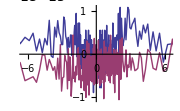

```mathematica
(lf//Hilbert//HilbertInverse)-lf
```

```mathematica
HilbertInverse[lf,0.1]-HilbertInverse[lf][0.1]
```

-9.71445×10^-17-2.92141×10^-16 ⅈ

## IntervalFun Test

```mathematica
f=ChebyshevT[2,#]&;
if=IFun[{0,0,1,0,0,0,0,0}//InverseDCT,UnitInterval];
```

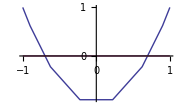

```mathematica
if
```

```mathematica
if[3.]-f[3.]
```

-1.27898×10^-12

```mathematica
CauchyBasis[if,3,1. I]-NIntegrate[f[x]/(x-1. I),{x,-1,1}]/(2 π I)
```

2.35922×10^-16+2.13082×10^-17 ⅈ

```mathematica
CauchyBasis[if,3,{1. I,1.I+1.,1.I+2.}]-(NIntegrate[f[x]/(x-#),{x,-1,1}]&/@{1. I,1.I+1.,1.I+2.})/(2 π I)//Norm
```

2.58298×10^-16

```mathematica
CauchyBasis[+1,if,3,0.1]-CauchyBasis[-1,if,3,0.1]-if[0.1]
```

-1.11022×10^-16+0. ⅈ

```mathematica
f=Exp;
if=IFun[Exp,UnitInterval,20];
```

```mathematica
Cauchy[if,{1. I,1.I+1.,1.I+2.}]-(NIntegrate[f[x]/(x-#),{x,-1,1}]&/@{1. I,1.I+1.,1.I+2.})/(2 π I)//Norm
```

2.92479×10^-16

```mathematica
Hilbert[if,0.1]-NIntegrate[f[z]/(z-0.1),{z,-1.,0.1,1.},PrincipalValue->True]/π
```

4.71845×10^-16+0. ⅈ

```mathematica
Cauchy[if,1.I+Range[100]]//Timing//First
```

0.150408

## Half Line Test

### Right Oriented

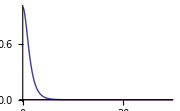

```mathematica
hf=IFun[Sech,Line[{0,∞}]]
```

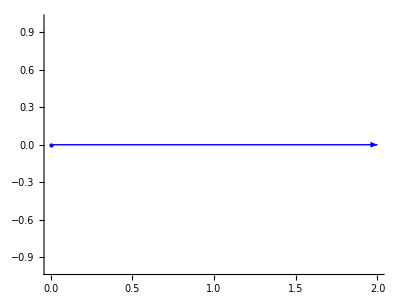

```mathematica
hf//DomainPlot
```

```mathematica
CauchyBasis[hf,2,5. I]-NIntegrate[1/(z-5. I)(ChebyshevT[1,MapToInterval[hf,z]]-ChebyshevT[0,MapToInterval[hf,z]]),{z,0,∞}]/(2 π I)
```

2.77556×10^-16+2.77556×10^-16 ⅈ

```mathematica
Cauchy[hf,5. I]-NIntegrate[Sech[z]/(z-5 I),{z,0,∞},WorkingPrecision->20]/(2 π I)
```

0.+2.17881×10^-15 ⅈ

```mathematica
Cauchy[+1,hf,2.]-Cauchy[-1,hf,2.]-hf[2.]
```

4.44089×10^-16+0. ⅈ

```mathematica
Hilbert[hf,2.]-NIntegrate[Sech[z]/(z-2),{z,0,2,∞},PrincipalValue->True,WorkingPrecision->20]/( π )
```

5.77316×10^-15+0. ⅈ

### Left Oriented

```mathematica
hfL=IFun[Sech,Line[{∞,0}]]
```

-Graphics-

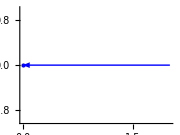

```mathematica
hfL//DomainPlot
```

```mathematica
Cauchy[+1,hfL,0.4]-Cauchy[-1,hfL,0.4]-hfL[0.4]
```

-9.99201×10^-16+0. ⅈ

```mathematica
Cauchy[+1,hfL,10.]+Cauchy[-1,hf,10.]
```

-1.68051×10^-16-6.34909×10^-16 ⅈ

```mathematica
Cauchy[+1,hfL,0.4]+Cauchy[-1,hf,0.4]
```

-3.33067×10^-16-1.15186×10^-15 ⅈ

```mathematica
Cauchy[-1,hfL,0.4]+Cauchy[1,hf,0.4]
```

3.33067×10^-16-1.15186×10^-15 ⅈ

```mathematica
Cauchy[hfL,1.I+Range[20]]//Timing
```

{2.50026,{-0.174022-0.0113294 ⅈ,-0.121045-0.0743734 ⅈ,-0.0697186-0.0834435 ⅈ,-0.0388029-0.073758 ⅈ,-0.022237-0.0614565 ⅈ,-0.0135024-0.0509949 ⅈ,-0.00877177-0.0429137 ⅈ,-0.00608061-0.0367871 ⅈ,-0.00445595-0.0320987 ⅈ,-0.00341382-0.0284401 ⅈ,-0.00270718-0.0255224 ⅈ,-0.0022048-0.0231469 ⅈ,-0.00183357-0.021177 ⅈ,-0.00155057-0.0195173 ⅈ,-0.00132936-0.0180998 ⅈ,-0.00115287-0.016875 ⅈ,-0.00100965-0.0158059 ⅈ,-0.000891737-0.0148645 ⅈ,-0.000793452-0.0140292 ⅈ,-0.00071064-0.0132829 ⅈ}}

## Cauchy Interval ± Toeplitz form

```mathematica
if=IFun[Exp[-5 (#-0.1)^2]&,UnitInterval,100];
fh=if//DCT;
```

### At all points

```mathematica
x=if//Points;
k=5;-1/(I π)(ψp[k-1,IntervalToBottomCircle[x]]+ψp[-k+1,IntervalToBottomCircle[x]])-(-2(ArcTanh[IntervalToBottomCircle[x]])/(I π) ChebyshevT[k-1,x]+IFun[((PadRight[4 Riffle[Reverse[Table[1/j,{j,1.,k-1,2}]],0]//(If[OddQ[k],Join[{0},#],#]&),Length[if]])//HalfFirst//InverseDCT),UnitInterval][x]/(2 I π))
```

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ
 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
-1/(I π)(ψp[k-1,IntervalToBottomCircle[x]]+ψp[-k+1,IntervalToBottomCircle[x]])//Timing//First
```

0.045155

```mathematica
(-2(ArcTanh[IntervalToBottomCircle[x]])/(I π) ChebyshevT[k-1,x]+((PadRight[4 Riffle[Reverse[Table[1/j,{j,1.,k-1,2}]],0]//(If[OddQ[k],Join[{0},#],#]&),Length[if]])//HalfFirst//InverseDCT)/(2 I π))//Timing//First
```

0.001891

### Pointwise

```mathematica
Cauchy[+1,if,0.2]-Cauchy[-1,if,0.2]-if[0.2]
```

1.11022×10^-16+0. ⅈ

```mathematica
Cauchy[if,0.2+0.0000001 I]-Cauchy[+1,if,0.2]//Chop
```

-1.13991×10^-7-4.75615×10^-8 ⅈ

```mathematica
x=0.2;-I Hilbert[if,x]-(-2(ArcTanh[IntervalToBottomCircle[x]]+ArcTanh[IntervalToTopCircle[x]])/(I π) if[x]+IFun[InverseDCT[HalfFirst[4 ∑_(j=1)^((Length[fh]+1)/2) 1/(2j-1)GrowShiftLeft[fh,2j-1]]],UnitInterval][x]/(I π))//Chop
```

0

```mathematica
Cauchy[+1,if,x]-(-2(ArcTanh[IntervalToBottomCircle[x]])/(I π) if[x]+IFun[InverseDCT[HalfFirst[4 ∑_(j=1)^((Length[fh]+1)/2) 1/(2j-1)GrowShiftLeft[fh,2j-1]]],UnitInterval][x]/(2I π))//Chop
```

0

```mathematica
Cauchy[-1,if,x]-(-2(ArcTanh[IntervalToTopCircle[x]])/(I π) if[x]+IFun[InverseDCT[HalfFirst[4 ∑_(j=1)^((Length[fh]+1)/2) 1/(2j-1)GrowShiftLeft[fh,2j-1]]],UnitInterval][x]/(2I π))//Chop
```

0

### Timing

```mathematica
HalfFirst[4 ∑_(j=1)^((Length[fh]+1)/2) 1/(2j-1)GrowShiftLeft[fh,2j-1]]//Timing//First
```

0.003144

```mathematica
A=ColumnMap[4 ∑_(j=1)^((Length[fh]+1)/2) 1/(2j-1)GrowShiftLeft[#,2j-1]&,IdentityMatrix[Length[fh]]];
```

```mathematica
A.fh//Timing//First
```

0.002153

```mathematica
?*plitz*
```

RowBox[{"ToeplitzMatrix", "[", StyleBox["n", "TI"], "]"}] gives the StyleBox["n", "TI"]×StyleBox["n", "TI"] Toeplitz matrix with first row and first column being successive integers.
RowBox[{"ToeplitzMatrix", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["c", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["c", "TI"], StyleBox["n", "TI"]]}], "}"}], "]"}] gives the Toeplitz matrix whose first column consists of elements SubscriptBox[StyleBox["c", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["c", "TI"], StyleBox["2", "TR"]], StyleBox["…", "TR"].
RowBox[{"ToeplitzMatrix", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["c", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["c", "TI"], StyleBox["m", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", "…", ",", " ", SubscriptBox[StyleBox["r", "TI"], StyleBox["n", "TI"]]}], "}"}]}], "]"}] gives the Toeplitz matrix with elements SubscriptBox[StyleBox["c", "TI"], StyleBox["i", "TI"]] down the first column, and SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]] across the first row.

```mathematica
Join[{0},Riffle[4Table[1/j,{j,1,Length[fh]-1,2}],0]]
```

{0,4,0,4/3,0,4/5,0,4/7,0,4/9,0,4/11,0,4/13,0,4/15,0,4/17,0,4/19,0,4/21,0,4/23,0,4/25,0,4/27,0,4/29,0,4/31,0,4/33,0,4/35,0,4/37,0,4/39,0,4/41,0,4/43,0,4/45,0,4/47,0,4/49,0,4/51,0,4/53,0,4/55,0,4/57,0,4/59,0,4/61,0,4/63,0,4/65,0,4/67,0,4/69,0,4/71,0,4/73,0,4/75,0,4/77,0,4/79,0,4/81,0,4/83,0,4/85,0,4/87,0,4/89,0,4/91,0,4/93,0,4/95,0,4/97,0,4/99}

```mathematica
A-ToeplitzMatrix[ZeroVector[Length[fh]],Join[{0},Riffle[4Table[1/j,{j,1,Length[fh]-1,2}],0]]]//Norm
```

0

```mathematica
A//Dimensions
```

{100,100}

```mathematica
k
```

90

```mathematica
k=92;(PadRight[4 Riffle[Reverse[Table[1/j,{j,1,k-1,2}]],0]//(If[OddQ[k],Join[{0},#],#]&),Length[if]])-A.BasisVector[100][k]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,4/89,0,4/87,0,4/85,0,4/83,0,4/81,0,4/79,0,4/77,0,4/75,0,4/73,0,4/71,0,4/69,0,4/67,0,4/65,0,4/63,0,4/61,0,4/59,0,4/57,0,4/55,0,4/53,0,4/51,0,4/49,0,4/47,0,4/45,0,4/43,0,4/41,0,4/39,0,4/37,0,4/35,0,4/33,0,4/31,0,4/29,0,4/27,0,4/25,0,4/23,0,4/21,0,4/19,0,4/17,0,4/15,0,4/13,0,4/11,0,4/9,0,4/7,0,4/5,0,4/3,0,4,0,0,0,0,0,0,0,0,0,0}

```mathematica
A.BasisVector[100][k]//MatrixForm
```

(4/89
0
4/87
0
4/85
0
4/83
0
4/81
0
4/79
0
4/77
0
4/75
0
4/73
0
4/71
0
4/69
0
4/67
0
4/65
0
4/63
0
4/61
0
4/59
0
4/57
0
4/55
0
4/53
0
4/51
0
4/49
0
4/47
0
4/45
0
4/43
0
4/41
0
4/39
0
4/37
0
4/35
0
4/33
0
4/31
0
4/29
0
4/27
0
4/25
0
4/23
0
4/21
0
4/19
0
4/17
0
4/15
0
4/13
0
4/11
0
4/9
0
4/7
0
4/5
0
4/3
0
4
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
A//MatrixForm
```

(0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93 | 0 | 4/95 | 0 | 4/97 | 0 | 4/99
0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93 | 0 | 4/95 | 0 | 4/97 | 0
0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93 | 0 | 4/95 | 0 | 4/97
0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93 | 0 | 4/95 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93 | 0 | 4/95
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0 | 4/93
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0 | 4/91
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0 | 4/89
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0 | 4/87
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0 | 4/85
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0 | 4/83
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0 | 4/81
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0 | 4/79
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0 | 4/77
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0 | 4/75
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0 | 4/73
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0 | 4/71
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0 | 4/69
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0 | 4/67
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0 | 4/65
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0 | 4/63
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0 | 4/61
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0 | 4/59
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0 | 4/57
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0 | 4/55
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0 | 4/53
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0 | 4/51
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0 | 4/49
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0 | 4/47
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0 | 4/45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0 | 4/43
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0 | 4/41
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0 | 4/39
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0 | 4/37
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0 | 4/35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0 | 4/33
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0 | 4/31
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0 | 4/29
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0 | 4/27
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0 | 4/25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0 | 4/23
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0 | 4/21
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0 | 4/19
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0 | 4/17
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0 | 4/15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0 | 4/13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0 | 4/11
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Singularity Data

```mathematica
if=IFun[Exp[-5 (#-0.1)^2]&,UnitInterval,100];
```

### Unit Interval

```mathematica
z=-1.+0.0000001 I;k=6;(LeftSingularityDataBasis[if,k]//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z+1)]&)-CauchyBasis[if,k,z]
```

-5.59346×10^-6-6.24998×10^-7 ⅈ

```mathematica
z=1.+0.0000001 I;(RightSingularityDataBasis[if,k]//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-1)]&)-CauchyBasis[if,k,z]
```

5.59346×10^-6-6.24998×10^-7 ⅈ

```mathematica
if//LeftSingularityData
```

{0.-0.127285 ⅈ,0.000375265 ⅈ,-1}

```mathematica
z=-1.+0.0000001 I;(if//LeftSingularityData//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z+1)]&)-Cauchy[if,z]
```

-2.10951×10^-8-6.48417×10^-10 ⅈ

```mathematica
z=1.+0.0000001 I;(if//RightSingularityData//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-1)]&)-Cauchy[if,z]
```

-6.15055×10^-8+3.92005×10^-9 ⅈ

### Other Interval

```mathematica
if=IFun[Exp,Line[{1.+0.1 I,-2.-3. I}]];
```

```mathematica
z=LeftEndpoint[if]+0.0000001 I;k=6;(LeftSingularityDataBasis[if,k]//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-LeftEndpoint[if])]&)-CauchyBasis[if,k,z]
```

1.79999×10^-6-2.06428×10^-6 ⅈ

```mathematica
z=RightEndpoint[if]+0.0000001 I;k=6;(RightSingularityDataBasis[if,k]//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-RightEndpoint[if])]&)-CauchyBasis[if,k,z]
```

-2.21654×10^-6+1.66104×10^-6 ⅈ

```mathematica
z=LeftEndpoint[if]+0.0000001 I;k=6;(LeftSingularityData[if]//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-LeftEndpoint[if])]&)-Cauchy[if,z]
```

-7.18711×10^-7-3.22271×10^-9 ⅈ

```mathematica
z=RightEndpoint[if]+0.0000001 I;k=6;(RightSingularityData[if]//#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-RightEndpoint[if])]&)-Cauchy[if,z]
```

-3.49112×10^-8-1.7544×10^-8 ⅈ

### Half Line

```mathematica
hf=IFun[Sech,Line[{0,∞}]];
```

```mathematica
Cauchy[+1,hf,0.1]-Cauchy[-1,hf,0.1]-hf[0.1]
```

-9.99201×10^-16+0. ⅈ

```mathematica
Cauchy[hf,1000. I]
```

0.000249999-2.91559×10^-7 ⅈ

```mathematica
z=LeftEndpoint[hf]+0.000001 I;(hf//LeftSingularityData//(#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-LeftEndpoint[hf])]&))-Cauchy[hf,z]
```

1.85608×10^-7+1.1311×10^-12 ⅈ

0

```mathematica
hfR=(hf//ReverseOrientation);(hfR//RightSingularityData//(#⟦1⟧+#⟦2⟧ Log[#⟦3⟧ (z-RightEndpoint[hfR])]&))-Cauchy[hfR,z]
```

-1.85608×10^-7-1.12932×10^-12 ⅈ

```mathematica
z=0.00001 Exp[-0.9 I];(LeftSingularityData[hf,-0.9]//(#⟦1⟧+#⟦2⟧ Log[Abs[z]]&))-Cauchy[hf,z]
```

-1.45405×10^-6-1.15375×10^-6 ⅈ

```mathematica
z=0.00001 Exp[-0.00001 I];(RightSingularityData[hfR,z//Arg]//(#⟦1⟧+#⟦2⟧ Log[Abs[z]]&))-Cauchy[hfR,z]
```

4.35633×10^-11+1.85623×10^-6 ⅈ

```mathematica
z=0.00001;(LeftSingularityData[+1,hf]//(#⟦1⟧+#⟦2⟧ Log[Abs[z]]&))-Cauchy[+1,hf,z]
```

2.49998×10^-11-1.85623×10^-6 ⅈ

```mathematica
z=0.00001;(LeftSingularityData[-1,hf]//(#⟦1⟧+#⟦2⟧ Log[Abs[z]]&))-Cauchy[-1,hf,z]
```

-2.49998×10^-11-1.85623×10^-6 ⅈ

```mathematica
z=0.00001; (RightSingularityData[+1,hfR]//(#⟦1⟧+#⟦2⟧ Log[Abs[z]]&))-Cauchy[+1,hfR,z]
```

2.50001×10^-11+1.85623×10^-6 ⅈ

```mathematica
z=0.00001; (RightSingularityData[-1,hfR]//(#⟦1⟧+#⟦2⟧ Log[Abs[z]]&))-Cauchy[-1,hfR,z]
```

-2.50001×10^-11+1.85623×10^-6 ⅈ

## Finite Part

### Unorganized

```mathematica
if=IFun[Exp,UnitInterval,100];
if2=IFun[Exp,Line[{2.+0.1 I,3.+4. I}]];
if3=IFun[Exp,Line[{1.,3.+4. I}],52];
if4=IFun[(#-1)(#+1)Exp[#]&,UnitInterval,30];
if5=IFun[If[Abs[#]==1.,0.,Sech[IntervalToRealLine[#]]]&,UnitInterval,300];

hf=IFun[Sech,Line[{1.,∞}]];
hf2=IFun[Sech,Line[{-∞,1.}]];
```

```mathematica
IFun[MapDot[Values[FPCauchyBasis[+1,if4,#,if4]]&,if4//DCT],if4//Domain][.2]-Cauchy[if4,.2]
```

-1.11022×10^-16+0.000075401 ⅈ

```mathematica
FPCauchy[+1,if5,if][.5]-Cauchy[+1,if5,.5]
```

-2.22045×10^-16-5.04203×10^-8 ⅈ

```mathematica
IFun[MapDot[Values[FPCauchyBasis[+1,if4,#,if]]&,if4//DCT],if4//Domain][.2]-Cauchy[if4,.2]//Chop
```

-9.76482×10^-7 ⅈ

```mathematica
CauchyBasis[if3,4,MapToInterval[if3,∞]]
```

0

```mathematica
(FPCauchyBasis[+1,if3,3,if3]//Values//Second)-CauchyBasis[+1,if3,3,if3//Points//Second]//Chop
```

0

```mathematica
hf2on1=FPCauchy[+1,hf2,hf];
```

```mathematica
hfp=FPCauchy[+1,hf,hf];
```

```mathematica
First[RightSingularityData[hf2,hf//LeftContourArg]]+First[LeftSingularityData[+1,hf]]-(Cauchy[hf2,1.+0.00001]+Cauchy[+1,hf,1.+0.00001])//Chop
```

2.46777×10^-6-9.30285×10^-7 ⅈ

```mathematica
First[RightSingularityData[hf2,hf//LeftContourArg]]-(hf2on1//Values//First)//Chop
```

0

```mathematica
First[LeftSingularityData[+1,hf]]-(hfp//Values//First)//Chop
```

0

```mathematica
hfp+hf2on1//DCT//Last//Chop
```

0

```mathematica
(hfp+hf2on1)[3.]-Cauchy[+1,LFun[Sech,RealLine,100]][3.]
```

1.18551×10^-7+1.44772×10^-7 ⅈ

```mathematica
CauchyBasis[hf,1,First[Points[hf2]]]
```

0

#### Left Contour

```mathematica
hf1on2=FPCauchy[+1,hf,hf2];
```

```mathematica
hf2p=FPCauchy[+1,hf2,hf2];
```

```mathematica
(hf2p//Values//Last)-(RightSingularityData[+1,hf2]//First)//Chop
```

0

```mathematica
First[LeftSingularityData[hf,-π]]-(hf1on2//Values//Last)//Chop
```

0

```mathematica
hf1on2+hf2p//DCT//Last//Chop
```

0

```mathematica
(hf1on2+hf2p)[-.1]-Cauchy[+1,LFun[Sech,RealLine,100]][-.1]
```

9.57833×10^-8-2.15786×10^-8 ⅈ

#### Minus

```mathematica
hf2m=FPCauchy[-1,hf2,hf2];
```

```mathematica
hfm=FPCauchy[-1,hf,hf];
```

```mathematica
hf2m+hf1on2//DCT//Last//Chop
```

0

```mathematica
(hf2m+hf1on2)[-.1]-Cauchy[-1,LFun[Sech,RealLine,100]][-.1]
```

9.05916×10^-8+3.02116×10^-8 ⅈ

```mathematica
hfm+hf2on1//DCT//Last//Chop
```

0

```mathematica
(hfm+hf2on1)[3.]-Cauchy[-1,LFun[Sech,RealLine,100]][3.]
```

-9.09897×10^-8+7.56795×10^-8 ⅈ

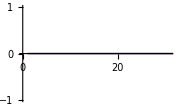

```mathematica
(hfp-hfm)-hf//Chop
```

```mathematica
I (hfp+hfm+2hf2on1)[3.]-Hilbert[LFun[Sech,RealLine,100]][3.]
```

-2.20452×10^-7+2.75616×10^-8 ⅈ

### TwoHalfLines

```mathematica
FPCauchyBasis[+1,GG⟦1⟧⟦1,1⟧,2,GG⟦2⟧⟦1,1⟧]//Values
```

{-0.166667+0.110318 ⅈ,-0.307672+1.13066 ⅈ,-0.268268+0.722023 ⅈ,-0.227351+0.498396 ⅈ,-0.186809+0.348153 ⅈ,-0.146524+0.236474 ⅈ,-0.105983+0.148696 ⅈ,-0.0650656+0.0786021 ⅈ,-0.025661+0.0258611 ⅈ,0}

## CauchyMatrix

### Scalar

```mathematica
if=IFun[Exp,UnitInterval,100];
if2=IFun[Exp,Line[{2.+0.1 I,3.+4. I}]];
hf=IFun[Sech,Line[{1.,∞}]];
```

```mathematica
FiniteTransformMatrix[hf].ToValueList[hf]-DCT[hf]//Norm
```

1.93086×10^-16

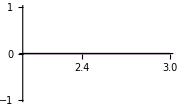

```mathematica
FromValueList[if2,CauchyMatrix[+1,if,if2].ToValueList[if]]-FPCauchy[+1,if,if2]//Chop
```

```mathematica
FromValueList[if2,CauchyMatrix[-1,if,if2].ToValueList[if]]-FPCauchy[-1,if,if2]//Chop
```

-Graphics-

```mathematica
FromValueList[if2,CauchyMatrix[+1,if2,if2].ToValueList[if2]]-FPCauchy[+1,if2,if2]//Chop
```

-Graphics-

```mathematica
FromValueList[if2,CauchyMatrix[+1,hf,if2].ToValueList[hf]]-FPCauchy[+1,hf,if2]//Chop
```

-Graphics-

```mathematica
FromValueList[hf,CauchyMatrix[+1,hf,hf].ToValueList[hf]]-FPCauchy[+1,hf,hf]//Chop
```

-Graphics-

### Vector

```mathematica
f={Exp[-#],Sech[#]}&;
if=IFun[f,UnitInterval];
if2=IFun[f,Line[{2.+0.1 I,3.+4. I}]];
hf=IFun[f,Line[{1.,∞}]];
```

```mathematica
(if//DCT)-Thread[{if⟦1⟧//DCT,if⟦2⟧//DCT}]//Norm
```

0.

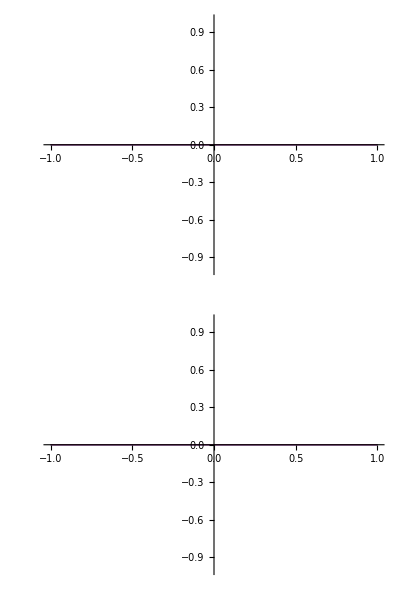
(-Graphics-)

```mathematica
if'-ToArrayFun[{if⟦1⟧',if⟦2⟧'}]
```

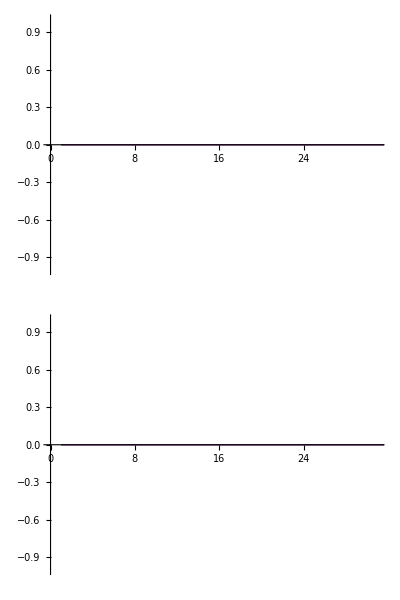
(-Graphics-)

```mathematica
FPCauchy[+1,if,hf]-ToArrayFun[{FPCauchy[+1,if⟦1⟧,hf⟦1⟧],
FPCauchy[+1,if⟦2⟧,hf⟦2⟧]}]//Chop
```

```mathematica
FPCauchy[+1,if,hf]-FromValueList[hf,CauchyMatrix[+1,if,hf].ToValueList[if]]//Chop
```

(-Graphics-)

```mathematica
FPCauchy[-1,if,hf]-ToArrayFun[{FPCauchy[-1,if⟦1⟧,hf⟦1⟧],
FPCauchy[-1,if⟦2⟧,hf⟦2⟧]}]//Chop
```

(-Graphics-)

```mathematica
FPCauchy[+1,if,if]-ToArrayFun[{FPCauchy[+1,if⟦1⟧,if⟦1⟧],
FPCauchy[+1,if⟦2⟧,if⟦2⟧]}]//Chop
```

(-Graphics-)

```mathematica
FPCauchy[-1,if,if]-ToArrayFun[{FPCauchy[-1,if⟦1⟧,if⟦1⟧],
FPCauchy[-1,if⟦2⟧,if⟦2⟧]}]//Chop
```

(-Graphics-)

### Matrix

```mathematica
f=({{Exp[-#], Sech[#]}, {1/(#^2+1), Exp[-#^2]}})&;
if=IFun[f,UnitInterval];
if2=IFun[f,Line[{2.+0.1 I,3.+4. I}]];
hf=IFun[f,Line[{1.,∞}]];
```

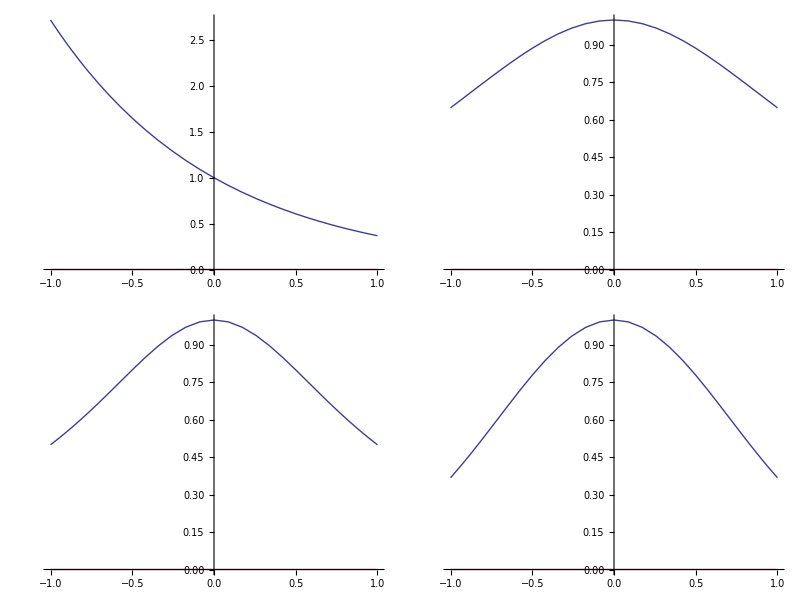
(-Graphics-)

```mathematica
if
```

```mathematica
(if//DCT)-({{if⟦1,1⟧//DCT,if⟦1,2⟧//DCT},
{if⟦2,1⟧//DCT,if⟦2,2⟧//DCT}}//ToListOfMatrices)//Flatten//Norm
```

0.

```mathematica
mat=CauchyMatrix[+1,if⟦1,1⟧,hf]
```

{{0.-3.46945×10^-18 ⅈ,0.+0.000715092 ⅈ,0.+0.00109641 ⅈ,«31»,0.+0.143242 ⅈ,0.+0.375125 ⅈ,0.-1.11645 ⅈ},«82»,{«1»}}

```mathematica
CauchyMatrix[+1,if⟦1,1⟧,hf]//BlockDiagonalMatrix[{#,#,#,#}]&;
```

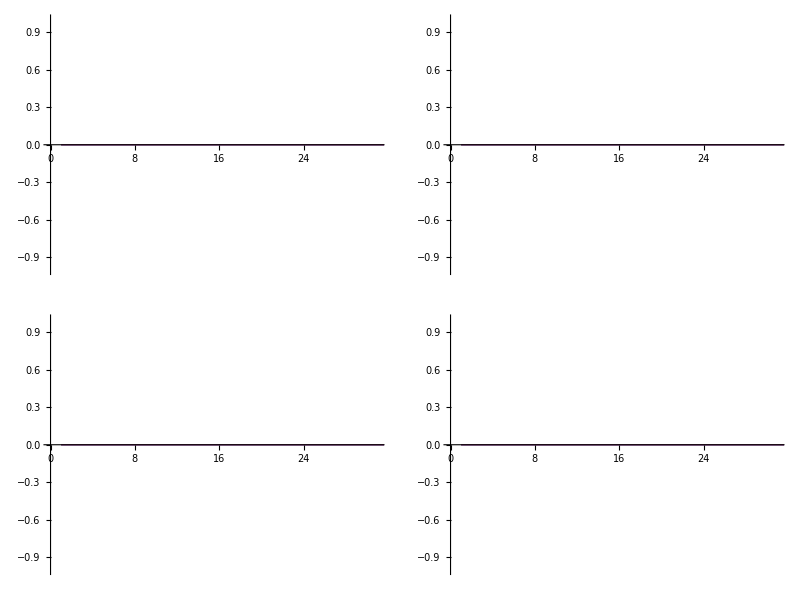
(-Graphics-)

```mathematica
FPCauchy[+1,if,hf]-ToArrayFun[{{FPCauchy[+1,if⟦1,1⟧,hf⟦1,1⟧],
FPCauchy[+1,if⟦1,2⟧,hf⟦1,2⟧]},{FPCauchy[+1,if⟦2,1⟧,hf⟦2,1⟧],
FPCauchy[+1,if⟦2,2⟧,hf⟦2,2⟧]}}]//Chop
```

```mathematica
FPCauchy[+1,if,hf]-FromValueList[hf,CauchyMatrix[+1,if,hf].ToValueList[if]]//Chop
```

(-Graphics-)

```mathematica
FPCauchy[+1,if,if]-ToArrayFun[{FPCauchy[+1,if⟦1⟧,if⟦1⟧],
FPCauchy[+1,if⟦2⟧,if⟦2⟧]}]//Chop
```

(-Graphics-)

```mathematica
FPCauchy[-1,if,if]-ToArrayFun[{FPCauchy[-1,if⟦1⟧,if⟦1⟧],
FPCauchy[-1,if⟦2⟧,if⟦2⟧]}]//Chop
```

(-Graphics-)

## List

### Scalar

```mathematica
if=IFun[Exp,UnitInterval,25];
if2=IFun[Exp,Line[{2.+0.1 I,3.+4. I}]];
hf=IFun[Sech,Line[{1.,∞}]];
l={if,if2,hf};
```

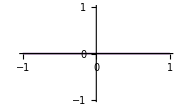

```mathematica
FromValueList[if,CauchyMatrix[+1,l,if].ToValueList[l]]-(FPCauchy[+1,l⟦1⟧,if]+FPCauchy[+1,l⟦2⟧,if]+FPCauchy[+1,l⟦3⟧,if])//Chop
```

```mathematica
FromValueList[l,CauchyMatrix[+1,l].ToValueList[l]]-{FPCauchy[+1,l⟦1⟧,if]+FPCauchy[+1,l⟦2⟧,if]+FPCauchy[+1,l⟦3⟧,if],
FPCauchy[+1,l⟦1⟧,if2]+FPCauchy[+1,l⟦2⟧,if2]+FPCauchy[+1,l⟦3⟧,if2],
FPCauchy[+1,l⟦1⟧,hf]+FPCauchy[+1,l⟦2⟧,hf]+FPCauchy[+1,l⟦3⟧,hf]}//Chop
```

{-Graphics-,-Graphics-,-Graphics-}

### Vector

```mathematica
f={Exp[-#],Sech[#]}&;
if=IFun[f,UnitInterval,25];
if2=IFun[f,Line[{2.+0.1 I,3.+4. I}]];
hf=IFun[f,Line[{1.,∞}]];
l={if,if2,hf};
```

```mathematica
FromValueList[if,CauchyMatrix[+1,l,if].ToValueList[l]]-(FPCauchy[+1,l⟦1⟧,if]+FPCauchy[+1,l⟦2⟧,if]+FPCauchy[+1,l⟦3⟧,if])//Chop
```

(-Graphics-)

```mathematica
mat=CauchyMatrix[+1,l];
```

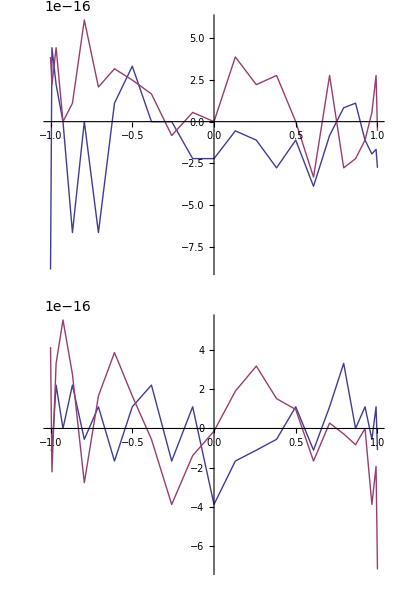
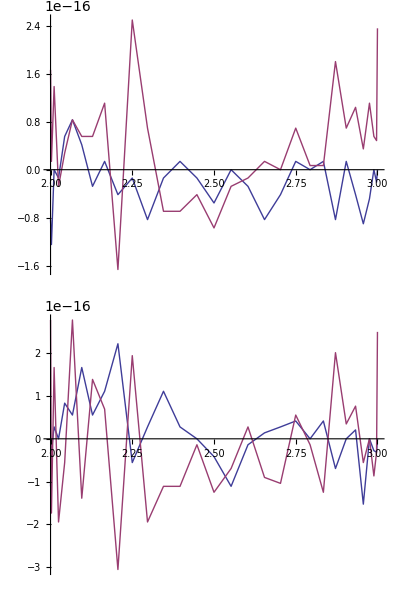
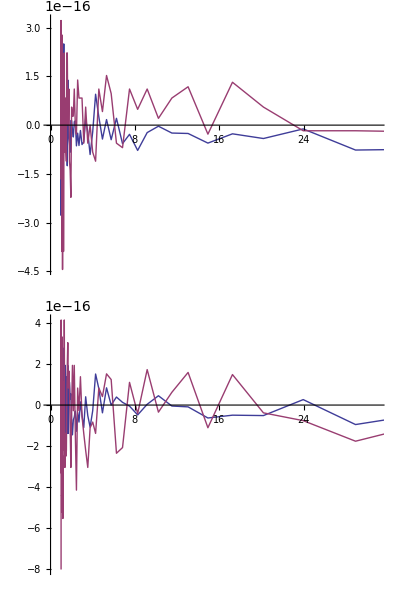
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
FromValueList[l,mat.ToValueList[l]]-{FPCauchy[+1,l⟦1⟧,if]+FPCauchy[+1,l⟦2⟧,if]+FPCauchy[+1,l⟦3⟧,if],
FPCauchy[+1,l⟦1⟧,if2]+FPCauchy[+1,l⟦2⟧,if2]+FPCauchy[+1,l⟦3⟧,if2],
FPCauchy[+1,l⟦1⟧,hf]+FPCauchy[+1,l⟦2⟧,hf]+FPCauchy[+1,l⟦3⟧,hf]}
```

### Matrix

```mathematica
f=({{Exp[-#], Sech[#]}, {1/(#^2+1), Exp[-#^2]}})&;
if=IFun[f,UnitInterval];
if2=IFun[f,Line[{2.+0.1 I,3.}]];
hf=IFun[f,Line[{1.,∞}]];
l={if,if2,hf};
```

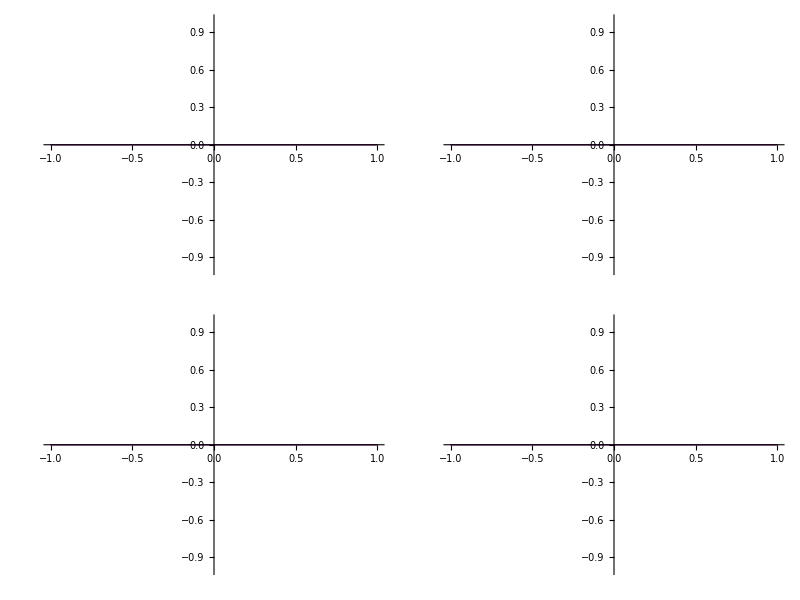
(-Graphics-)

```mathematica
FromValueList[if,CauchyMatrix[+1,l,if].ToValueList[l]]-(FPCauchy[+1,l⟦1⟧,if]+FPCauchy[+1,l⟦2⟧,if]+FPCauchy[+1,l⟦3⟧,if])//Chop
```

```mathematica
mat=CauchyMatrix[+1,l];
```

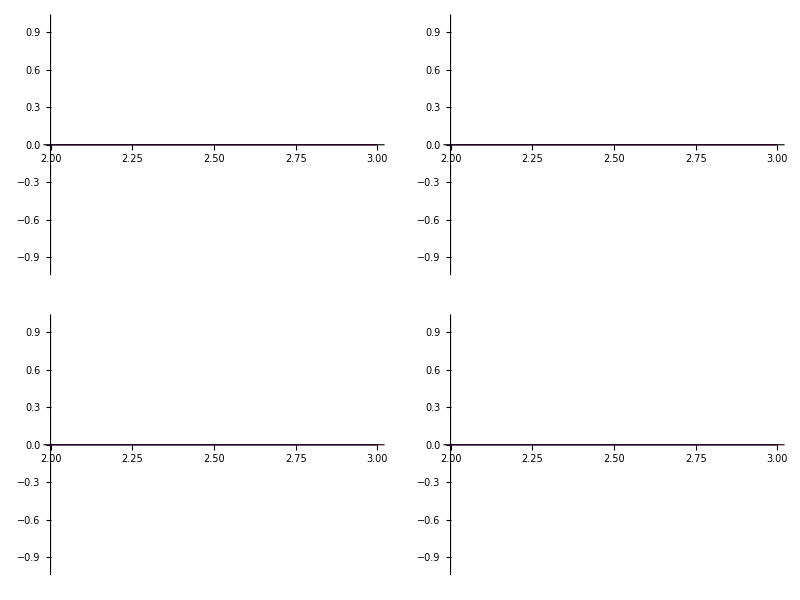
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
FromValueList[l,mat.ToValueList[l]]-{FPCauchy[+1,l⟦1⟧,if]+FPCauchy[+1,l⟦2⟧,if]+FPCauchy[+1,l⟦3⟧,if],
FPCauchy[+1,l⟦1⟧,if2]+FPCauchy[+1,l⟦2⟧,if2]+FPCauchy[+1,l⟦3⟧,if2],
FPCauchy[+1,l⟦1⟧,hf]+FPCauchy[+1,l⟦2⟧,hf]+FPCauchy[+1,l⟦3⟧,hf]}//Chop
```

## Timing

```mathematica
Cauchy[if,1.I+Range[20]]//Timing//First
```

0.071272

```mathematica
Cauchy[hf,(.01I+1. Range[20])]//Timing//First
```

1.63299

```mathematica
Cauchy[hf,#]&/@(1.I+Range[20])//Timing//First
```

3.19843

```mathematica
CauchyBasis[if,90,(.01I+1. Range[100])//N]//Timing//First
```

0.049968

```mathematica
CauchyBasis[hf,90,.01I+Range[100]]//Timing//First
```

0.498753

```mathematica
CauchyBasis[if,40,MapToInterval[hf,.01I+Range[100]]]//Timing//First
```

0.322224

```mathematica
CauchyBasis[if,40,#]&/@MapToInterval[hf,.01I+Range[100]]//Timing//First
```

0.076198

```mathematica
CauchyBasis[hf,90,#]&/@(1.I+Range[100])//Timing//First
```

0.5445

```mathematica
k=90;
z=1.I+Range[100];
CauchyBasis[hf//ToUnitInterval,90,MapToInterval[hf,z]]//Timing//First
```

0.511989

```mathematica
x=MapToInterval[hf,z];
```

```mathematica
CauchyBasis[if,90,x]//Timing//First
```

0.512488

```mathematica
-1/(I π)(ψp[k-1,IntervalToInnerCircle[x]])//Timing//First
```

0.082676

```mathematica
{Timing[ψp[-k+1,#]]//First,#}&/@IntervalToInnerCircle[x]//Sort//Last
```

{0.010094,0.94623-0.310931 ⅈ}

```mathematica
0.9462295925446707-0.3109312960261191 ⅈ//Arg
```

-0.317485

### rand around point

```mathematica
rand=Array[Random[Real,{0.85,1.05}] Exp[I (Random[Real,{-0.3,0.3}]-0.3174847627596865)]&,200];
```

```mathematica
Timing[ψpH[-90, rand]]//First
```

0.401802

```mathematica
Timing[ψpμ[-90, rand]]//First
```

0.059182

```mathematica
ψpμ[-90,rand]-ψpH[-90,rand]//Abs
```

```mathematica
Thread[{ψpμ[-90,rand]-ψpH[-90,rand]//Abs,rand}]//Sort//Last
```

{1.16399×10^-7,0.9649-0.320226 ⅈ}

```mathematica
0.964899731522672-0.32022634373887 ⅈ//Abs
```

1.01665

```mathematica
Table[Thread[{ψpμ[j,rand]-ψpH[j,rand]//Abs,rand}]//Sort//Last//First,{j,-45,-1}]
```

{1.38077×10^-12,1.42654×10^-12,8.19116×10^-13,7.00987×10^-13,5.86353×10^-13,5.0776×10^-13,4.39092×10^-13,3.75768×10^-13,3.02204×10^-13,2.58617×10^-13,2.24555×10^-13,1.92176×10^-13,1.61526×10^-13,1.38229×10^-13,1.01364×10^-13,8.65006×10^-14,7.78919×10^-14,6.66476×10^-14,6.76336×10^-14,5.76667×10^-14,4.2362×10^-14,3.62548×10^-14,3.40408×10^-14,2.91392×10^-14,2.81799×10^-14,2.41051×10^-14,1.95303×10^-14,1.67029×10^-14,1.41162×10^-14,1.20705×10^-14,1.00608×10^-14,8.60339×10^-15,9.0539×10^-15,7.7892×10^-15,5.51703×10^-15,4.7515×10^-15,4.28887×10^-15,3.88967×10^-15,3.21704×10^-15,2.71636×10^-15,2.28962×10^-15,2.10394×10^-15,2.0381×10^-15,1.88493×10^-15,4.57757×10^-16}

### Old

```mathematica
{0.0008870000000058553,0.0059245906210889017724832300383864452`15.893328321236682-0.00761459504898400402642953318473098151`16.002316786626285 ⅈ}
```

```mathematica
zz^(-k+1)( ψp[0,zz]-μ[-(-k+1)-1,zz])//Timing
```

{0.000567,0.00592459-0.0076146 ⅈ}

```mathematica
ψpμ[10,0.000001]-ψpH[10,0.000001]
```

1.19114×10^-22+1.36072×10^-23 ⅈ

```mathematica
Table[{Timing[ψpμ[j,0.6]]//First,Timing[ψpH[j,0.6]]//First},{j,-40,40}]
```

{{0.000195,0.000076},{0.000086,0.000074},{0.000083,0.000063},{0.000081,0.000063},{0.000091,0.000066},{0.000085,0.000063},{0.000095,0.000062},{0.000081,0.000061},{0.000079,0.000062},{0.000079,0.00006},{0.000079,0.000059},{0.000079,0.000063},{0.000078,0.00006},{0.000078,0.000062},{0.000079,0.000061},{0.000078,0.000063},{0.000077,0.00006},{0.000077,0.000077},{0.000078,0.000066},{0.000081,0.000063},{0.000077,0.00006},{0.000076,0.000061},{0.000076,0.000062},{0.000077,0.000062},{0.000096,0.000094},{0.000086,0.000063},{0.000078,0.00006},{0.000075,0.000063},{0.000077,0.000062},{0.000075,0.000062},{0.000076,0.000061},{0.000075,0.000061},{0.000076,0.000071},{0.000077,0.000061},{0.000074,0.000061},{0.000073,0.000094},{0.000074,0.000061},{0.000071,0.000061},{0.000073,0.00006},{0.000067,0.000059},{4.×10^-6,3.×10^-6},{0.000116,0.000103},{0.000102,0.000099},{0.0001,0.000102},{0.000103,0.000102},{0.000108,0.000102},{0.000107,0.000101},{0.000102,0.000101},{0.000102,0.000103},{0.000102,0.000124},{0.000104,0.00012},{0.000104,0.000127},{0.000116,0.000127},{0.000104,0.000132},{0.000114,0.000133},{0.000106,0.000405},{0.000109,0.000397},{0.000107,0.000405},{0.000109,0.0004},{0.000109,0.000404},{0.000109,0.000401},{0.000113,0.000413},{0.000116,0.000415},{0.000109,0.000427},{0.00011,0.000426},{0.00011,0.000457},{0.000115,0.000466},{0.000116,0.000482},{0.000112,0.000474},{0.00011,0.00048},{0.000113,0.000495},{0.000116,0.000493},{0.000112,0.000497},{0.000112,0.000502},{0.000118,0.000527},{0.000118,0.000568},{0.000115,0.000525},{0.000114,0.000537},{0.000113,0.000543},{0.000122,0.000573},{0.000117,0.000569}}

```mathematica
Table[ψpμ[j,zz]-ψpH[j,zz],{j,-100,100}]
```

```mathematica
ψpμ[-40,zz]//Timing
```

{0.000516,0.00341227-0.0395048 ⅈ}

{-1.,-0.809017-0.587785 ⅈ,-0.309017-0.951057 ⅈ,0.309017-0.951057 ⅈ,0.809017-0.587785 ⅈ,1.,0.809017+0.587785 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ,-0.809017+0.587785 ⅈ}

```mathematica
Timing[ψpH[-40, NCirclePoints[100]]]//First
```

0.085574

```mathematica
Timing[ψpμ[-40, NCirclePoints[100]]]//First
```

0.024429

```mathematica
({Timing[ψpH[-100,  #]]//First,#})&/@NCirclePoints[200]//Sort//Last//Last
```

```mathematica
Exp[I(0.5 -2.827433388230814)]-Exp[I(-2.827433388230814)]//Abs
```

0.494808

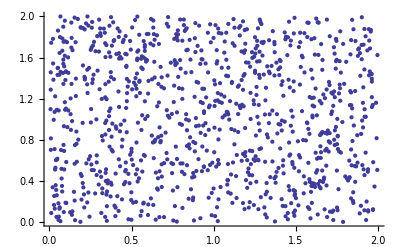

```mathematica
rand//ComplexDotPlot
```

```mathematica
?Random
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

```mathematica
rand=Array[Random[Real,{0.85,1.05}] Exp[I (Random[Real,{-0.3,0.3}]-2.827433388230814)]&,200];
```

```mathematica
Select[rand,0.85<Abs[#]<1.1&&-0.3-2.827433388230814<Arg[#]<0.3-2.827433388230814&]//Length
```

8348

```mathematica
-2.827433388230814-0.3
```

-3.12743

```mathematica
ψpμ[-40,rand]//Timing//First
```

0.264696

```mathematica
-1.0383692595445084-0.3579858797707254 ⅈ//Abs
```

1.09835

```mathematica
-0.7932003906699738-0.10824482477057942 ⅈ//Abs
```

0.800552

```mathematica
%//Last
```

{7.88011×10^-12,-0.7932-0.108245 ⅈ}

```mathematica
-0.3-2.827433388230814
```

-3.12743

```mathematica
Thread[{ψpμ[-100,rand]-ψpH[-100,rand]//Abs,rand}]//Sort//Last//Last
```

```mathematica
ψp[-40,#]&/@rand//Timing//First
```

0.062916

```mathematica
ψpH[-40,#]&/@rand//Timing//First
```

0.254707

```mathematica
ψp[-40,1.+Range[100] 1. I]//Timing//First
```

0.02984

```mathematica
ψp[-40,#]&/@(1.+Range[100] 1. I)//Timing//First
```

0.033297

```mathematica
Timing[ψpμ[-100,rand]]//First
```

0.062066

```mathematica
Timing[ψpH[-100,rand]]//First
```

0.409827

```mathematica
-0.9777065934740792-0.33261717228442733 ⅈ //Abs
```

1.03274

```mathematica
-0.9777065934740792-0.33261717228442733 ⅈ //Arg
```

-2.81367

```mathematica
Table[Timing[ψpμ[j,rand]]//First,{j,1,50}]
```

{0.051571,0.050022,0.049339,0.049226,0.049645,0.049702,0.049987,0.049971,0.050131,0.050061,0.050279,0.050643,0.05049,0.050519,0.050855,0.05074,0.051253,0.051014,0.051254,0.051267,0.05144,0.051492,0.051994,0.05176,0.052054,0.051943,0.052279,0.0522,0.052398,0.052318,0.05255,0.05258,0.052838,0.053368,0.053151,0.05309,0.053314,0.053174,0.053938,0.054341,0.054631,0.053954,0.054145,0.054434,0.05449,0.054455,0.054662,0.054835,0.054913,0.054939}

```mathematica
Table[Timing[ψpH[j,rand]]//First,{j,1,50}]
```

{0.054258,0.053307,0.053909,0.055122,0.055093,0.054921,0.056168,0.055984,0.057147,0.057159,0.068213,0.068152,0.0839,0.084009,0.087464,0.087345,0.096929,0.096864,0.10275,0.102937,0.10765,0.107368,0.111705,0.111693,0.117706,0.117832,0.122643,0.120922,0.125621,0.12568,0.129327,0.128906,0.132838,0.132957,0.136479,0.136494,0.13884,0.138942,0.142172,0.141948,0.145005,0.146602,0.148142,0.148014,0.150534,0.150623,0.152706,0.152713,0.155098,0.155428}

```mathematica
Table[Thread[{ψpμ[j,rand]-ψpH[j,rand]//Abs,rand}]//Sort//Last//First,{j,1,25}]
```

{1.5896×10^-15,1.57009×10^-15,1.57009×10^-15,1.60119×10^-15,1.72353×10^-15,1.72353×10^-15,1.7422×10^-15,1.55654×10^-15,3.63672×10^-15,3.77476×10^-15,8.41964×10^-15,7.19935×10^-15,9.86636×10^-15,8.46579×10^-15,1.90263×10^-14,1.63721×10^-14,8.15134×10^-14,6.99234×10^-14,1.2972×10^-13,1.10992×10^-13,3.37889×10^-13,2.89909×10^-13,6.56511×10^-13,5.61755×10^-13,1.79443×10^-12}

```mathematica
Table[Thread[{ψpμ[j,rand]-ψpH[j,rand]//Abs,rand}]//Sort//Last//First,{j,-50,-1}]
```

{8.91961×10^-12,6.20955×10^-12,6.51294×10^-12,4.76713×10^-12,4.83093×10^-12,3.486×10^-12,3.65632×10^-12,1.78902×10^-12,1.87643×10^-12,1.13251×10^-12,1.13482×10^-12,3.81804×10^-13,3.59319×10^-13,3.2674×10^-13,3.37431×10^-13,2.0427×10^-13,1.76888×10^-13,1.43623×10^-13,1.2277×10^-13,9.50978×10^-14,8.12896×10^-14,7.3329×10^-14,6.26914×10^-14,4.58622×10^-14,3.92055×10^-14,3.71969×10^-14,3.18029×10^-14,2.96293×10^-14,2.53374×10^-14,2.00543×10^-14,1.71452×10^-14,1.31126×10^-14,1.12121×10^-14,9.95923×10^-15,8.50291×10^-15,8.07779×10^-15,6.90385×10^-15,9.62563×10^-15,8.36011×10^-15,4.33238×10^-15,3.66883×10^-15,2.92489×10^-15,2.64043×10^-15,3.00594×10^-15,2.75176×10^-15,1.92696×10^-15,1.79362×10^-15,1.79018×10^-15,1.79018×10^-15,4.96507×10^-16}

```mathematica
-0.797554038896619-0.09701269577306018//ComplexDotPlot
```

ListPlot::lpn: -0.894567 is not a list of numbers or pairs of numbers.

ListPlot[-0.894567]

```mathematica
Exp[I(-0.2-2.827433388230814)]//Arg
```

-3.02743

```mathematica
ψpH[-100,1.Exp[I(0.3-2.827433388230814)]]//Timing
```

{0.000851,-0.000122839-0.00867212 ⅈ}

```mathematica
ψpH[-100,Exp[I(0.5 -2.827433388230814)]]//Timing
```

{0.000325,-0.000064849-0.00687426 ⅈ}

```mathematica
ψpH[-100,-0.9510565162951535-0.3090169943749475 ⅈ ]-ψpϕ[-100,-0.9510565162951535-0.3090169943749475 ⅈ ]
```

0.+0. ⅈ

```mathematica
(-0.9510565162951535-0.3090169943749475 ⅈ)//Arg
```

-2.82743

```mathematica
({Timing[ψpμ[-40,  #]]//First,#})&/@NCirclePoints[100]//Sort
```

{{0.00005,1.},{0.000078,0.+1. ⅈ},{0.00009,-1.},{0.000091,0.-1. ⅈ},{0.000175,0.125333+0.992115 ⅈ},{0.000175,0.187381+0.982287 ⅈ},{0.000175,-0.125333+0.992115 ⅈ},{0.000176,-0.187381-0.982287 ⅈ},{0.000176,-0.187381+0.982287 ⅈ},{0.000177,0.0627905+0.998027 ⅈ},{0.000177,-0.125333-0.992115 ⅈ},{0.000177,0.187381-0.982287 ⅈ},{0.000178,-0.24869-0.968583 ⅈ},{0.000178,0.0627905-0.998027 ⅈ},{0.000178,0.998027-0.0627905 ⅈ},{0.000178,-0.24869+0.968583 ⅈ},{0.000178,-0.0627905+0.998027 ⅈ},{0.000178,0.125333-0.992115 ⅈ},{0.000179,0.24869+0.968583 ⅈ},{0.000179,-0.998027+0.0627905 ⅈ},{0.000181,0.998027+0.0627905 ⅈ},{0.000182,-0.309017+0.951057 ⅈ},{0.000182,0.24869-0.968583 ⅈ},{0.000182,0.309017+0.951057 ⅈ},{0.000183,-0.368125+0.929776 ⅈ},{0.000183,0.309017-0.951057 ⅈ},{0.000183,0.368125-0.929776 ⅈ},{0.000185,0.368125+0.929776 ⅈ},{0.000186,-0.309017-0.951057 ⅈ},{0.000187,-0.0627905-0.998027 ⅈ},{0.000187,0.425779-0.904827 ⅈ},{0.000189,-0.425779+0.904827 ⅈ},{0.00019,0.425779+0.904827 ⅈ},{0.000194,-0.481754-0.876307 ⅈ},{0.000196,-0.481754+0.876307 ⅈ},{0.000196,0.481754-0.876307 ⅈ},{0.000197,0.481754+0.876307 ⅈ},{0.000201,-0.992115+0.125333 ⅈ},{0.000203,-0.535827+0.844328 ⅈ},{0.000204,0.992115+0.125333 ⅈ},{0.000205,0.535827-0.844328 ⅈ},{0.000209,-0.587785+0.809017 ⅈ},{0.00021,0.992115-0.125333 ⅈ},{0.000212,0.535827+0.844328 ⅈ},{0.000212,0.587785+0.809017 ⅈ},{0.000213,-0.587785-0.809017 ⅈ},{0.000215,0.587785-0.809017 ⅈ},{0.000217,-0.368125-0.929776 ⅈ},{0.000217,-0.535827-0.844328 ⅈ},{0.000222,-0.992115-0.125333 ⅈ},{0.000223,-0.637424+0.770513 ⅈ},{0.000224,-0.982287+0.187381 ⅈ},{0.000224,0.982287-0.187381 ⅈ},{0.000226,0.637424-0.770513 ⅈ},{0.000226,0.982287+0.187381 ⅈ},{0.000227,0.637424+0.770513 ⅈ},{0.000235,-0.637424-0.770513 ⅈ},{0.000241,-0.982287-0.187381 ⅈ},{0.000251,-0.425779-0.904827 ⅈ},{0.000268,-0.998027-0.0627905 ⅈ},{0.000269,0.968583+0.24869 ⅈ},{0.00027,0.968583-0.24869 ⅈ},{0.000273,-0.968583+0.24869 ⅈ},{0.000289,-0.968583-0.24869 ⅈ},{0.000313,0.951057+0.309017 ⅈ},{0.000316,0.684547+0.728969 ⅈ},{0.000325,-0.684547+0.728969 ⅈ},{0.000328,0.684547-0.728969 ⅈ},{0.000331,-0.684547-0.728969 ⅈ},{0.000333,-0.728969-0.684547 ⅈ},{0.000333,0.728969+0.684547 ⅈ},{0.000335,0.728969-0.684547 ⅈ},{0.000343,0.951057-0.309017 ⅈ},{0.000344,-0.728969+0.684547 ⅈ},{0.00035,-0.951057-0.309017 ⅈ},{0.000354,-0.951057+0.309017 ⅈ},{0.000389,0.876307-0.481754 ⅈ},{0.000392,-0.876307+0.481754 ⅈ},{0.000392,0.844328-0.535827 ⅈ},{0.000393,-0.844328-0.535827 ⅈ},{0.000394,-0.844328+0.535827 ⅈ},{0.000395,0.844328+0.535827 ⅈ},{0.000401,-0.876307-0.481754 ⅈ},{0.000404,0.904827-0.425779 ⅈ},{0.000405,0.904827+0.425779 ⅈ},{0.000407,-0.770513-0.637424 ⅈ},{0.000408,-0.770513+0.637424 ⅈ},{0.000408,-0.904827+0.425779 ⅈ},{0.000409,0.770513+0.637424 ⅈ},{0.000409,0.809017-0.587785 ⅈ},{0.00041,0.809017+0.587785 ⅈ},{0.000411,-0.809017+0.587785 ⅈ},{0.000427,0.876307+0.481754 ⅈ},{0.00043,-0.809017-0.587785 ⅈ},{0.000432,0.770513-0.637424 ⅈ},{0.000436,-0.904827-0.425779 ⅈ},{0.00045,0.929776-0.368125 ⅈ},{0.000457,-0.929776+0.368125 ⅈ},{0.000459,0.929776+0.368125 ⅈ},{0.000479,-0.929776-0.368125 ⅈ}}

```mathematica
(Timing[ψpμ[-40,0.996  #]]//First)&/@NCirclePoints[100]
```

{0.00021,0.000233,0.000246,0.000269,0.000323,0.000393,0.000513,0.00047,0.000427,0.000445,0.000415,0.000418,0.000347,0.000321,0.000231,0.000212,0.000201,0.000197,0.000189,0.000185,0.00018,0.000194,0.000216,0.000214,0.000218,0.00019,0.000183,0.000196,0.000179,0.000178,0.000189,0.000256,0.000199,0.000208,0.000211,0.000235,0.000234,0.000345,0.000353,0.000399,0.000433,0.000402,0.000399,0.000408,0.000455,0.000345,0.00028,0.000224,0.000202,0.000181,0.000102,0.00018,0.000201,0.000224,0.000269,0.000313,0.000459,0.000406,0.000398,0.000388,0.000392,0.000388,0.000333,0.000343,0.000226,0.000211,0.000199,0.000195,0.000195,0.000184,0.00018,0.000178,0.000174,0.000175,0.000173,0.000157,0.000175,0.000173,0.000174,0.000179,0.000181,0.000184,0.000188,0.000196,0.0002,0.000209,0.000224,0.000317,0.000331,0.000409,0.000399,0.000399,0.000394,0.000404,0.000455,0.000337,0.000273,0.000224,0.0002,0.000179}

```mathematica
ψpH[-40,zz]//Timing
```

{0.007968,0.00341227-0.0395048 ⅈ}

```mathematica
ψpμ[-40,zz]//Timing
```

{0.000518,0.00341227-0.0395048 ⅈ}

```mathematica
ψpH[-40,zz]-ψpμ[-40,zz]//Timing
```

{0.007362,-1.63064×10^-16+2.498×10^-16 ⅈ}

```mathematica
zz//Abs
```

0.996006

```mathematica
zz^(2)
```

0.798672-0.588425 ⅈ

```mathematica
π/3.
```

1.0472

0.314159

```mathematica
Exp[I π/3.]
```

0.5+0.866025 ⅈ

```mathematica
zz=0.9462295925446707-0.3109312960261191 ⅈ;
```

```mathematica
k
```

90

```mathematica
({Timing[ψpH[-k+1,#]]//First,#})&/@z//Sort//Last//Last
```

0.94623-0.310931 ⅈ

0.

```mathematica
//Timing
```

{0.000176,9.09091×10^-8}

```mathematica
{0.0005120000000147229,0.005924590621088583-0.0076145950489839714 ⅈ}
```

0.00592459-0.0076146 ⅈ

```mathematica
M=Floor[(k-1)/2]
```

44

```mathematica
z=IntervalToInnerCircle[x];
```

```mathematica
Last/@(({Hypergeometric2F1[1,1/2+M,3/2+M,#]//Timing//First,#})&/@(z^2)//Sort//Reverse)⟦;;10⟧
```

{0.798672-0.588425 ⅈ,0.803502-0.582309 ⅈ,0.808107-0.576372 ⅈ,0.812502-0.570608 ⅈ,0.816703-0.565007 ⅈ,0.82072-0.559563 ⅈ,0.824567-0.554269 ⅈ,0.828253-0.549118 ⅈ,0.831789-0.544104 ⅈ,0.835182-0.539222 ⅈ}

```mathematica
Hypergeometric2F1[1,1/2+M,3/2+M,0.7986721709587714-0.588424787096362 ⅈ]//Timing
```

{0.012742,0.577594-1.51609 ⅈ}

```mathematica
ϕ[-k,zz]//Timing
```

{0.00064,1.12362-0.00244977 ⅈ}

```mathematica
Hypergeometric2F1[1,1/2+M,3/2+M,zz]//Timing
```

{0.010429,0.577594-1.51609 ⅈ}

```mathematica
zz=0.7986721709587714-0.588424787096362 ⅈ;1/(1-zz) Hypergeometric2F1[1,1,1.5+M,zz/(zz-1)]//Timing
```

{0.016134,0.577594-1.51609 ⅈ}

```mathematica
zz/(zz-1)
```

0.479473+1.52136 ⅈ

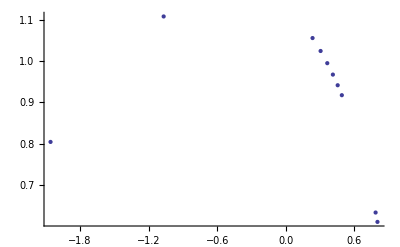

```mathematica
Last/@(({Hypergeometric2F1[1,1/2+M,3/2+M,#]//Timing//First,#})&/@(z^-2)//Sort//Reverse)⟦;;10⟧//ComplexDotPlot
```

```mathematica
Hypergeometric2F1[1,1/2 +M,3/2+M,z^-2]//Timing//First
```

0.077604

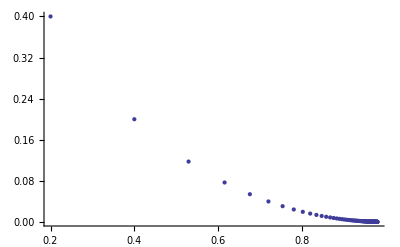

```mathematica
x//ComplexDotPlot
```

```mathematica
x
```

```mathematica
hf//ToUnitInterval//Timing//First
```

0.000047

```mathematica
MapToInterval[hf,z]//Timing//First
```

0.000519

## Cauchy Matrix dimensions timing

```mathematica
{s[1],s[2],s[3]}={I,0,-I};
{s[4],s[5],s[6]}=-Array[s,3];
θ[x_,z_]:=(8 I)/3 z^3+ 2 I x z;
G[_][_,_?InfinityQ]:=({{1, 0}, {0, 1}});
G[1][x_,z_]:=({{1, 0}, {s[1]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[3][x_,z_]:=({{1, 0}, {s[3]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[4][x_,z_]:=({{1, s[4]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
G[6][x_,z_]:=({{1, s[6]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
```

```mathematica
n=30;
GG={IFun[G[1][0.,#]&,Line[{0,∞ Exp[I π/6]}],n],IFun[G[3][0.,#]&,Line[{0,∞ Exp[I (π/6+2 π/3)]}],n],
IFun[G[4][0.,#]&,Line[{0,∞ Exp[I (-π/6-2 π/3)]}],n],
IFun[G[6][0.,#]&,Line[{0,∞ Exp[I (-π/6)]}],n]
};
```

```mathematica
Timing[CauchyMatrix[+1,GG];]
```

{5.75924,Null}

```mathematica
{12.73695,Null}
```

```mathematica
Timing[CauchyMatrix[+1,#⟦1,All⟧&/@GG];]
```

{5.76678,Null}

```mathematica
Timing[CauchyMatrix[+1,#⟦1,1⟧&/@GG];]
```

{5.75384,Null}

```mathematica
Timing[CauchyMatrix[+1,GG,GG⟦1⟧];]
```

{1.43297,Null}

```mathematica
Timing[FPCauchyBasis[+1,GG⟦2⟧,2,GG⟦1⟧];]
```

{0.009854,Null}

```mathematica
Timing[FPCauchyBasis[+1,GG⟦2⟧,2,GG⟦1⟧];]
```

{0.009905,Null}

```mathematica
Timing[CauchyBasis[GG⟦2⟧,2,(GG⟦1⟧//Points//Rest//Most)];]
```

{0.00915,Null}

```mathematica
Timing[CauchyBasis[GG⟦2⟧,2,#]&/@(GG⟦1⟧//Points//Rest//Most);]
```

{0.016335,Null}

```mathematica
Timing[FPCauchyBasis[+1,GG⟦2⟧//ToUnitInterval,2,GG⟦1⟧//ToUnitInterval];]
```

{0.002396,Null}

```mathematica
Timing[With[{s=+1,k=2,f=GG⟦2⟧,g=GG⟦1⟧},IFun[Values[FPCauchyBasis[s,f//ToUnitInterval,k,g//ToUnitInterval]]-Values[FPCauchyBasis[s,f//ToUnitInterval,1,g//ToUnitInterval]]-1/(I π)(μ[k-1,1.]+μ[k-2,1.])//#+LeftSingularityDataBasis[f//ToUnitInterval,k]⟦2⟧ Log[Abs[MapToIntervalD[f,f//LeftEndpoint]]] BasisVector[Length[#]][1]&
,g//Domain]];]
```

{0.00501,Null}

```mathematica
{3.141857999999999,Null}
```

```mathematica
Timing[CauchyMatrix[+1,GG⟦2⟧,GG⟦1⟧];]
```

{0.698742,Null}

```mathematica
{0.9895099999999957,Null}
```

```mathematica
0.0005 30^2 2
```

0.9

## Timing

```mathematica
rand=Array[Random[Real,{0,1}] Exp[I Random[Real,{-π,π}]]&,1000];
```

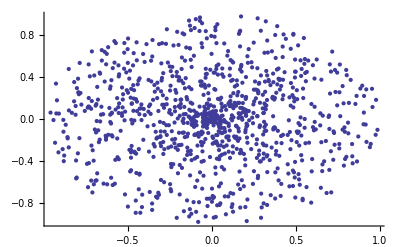

```mathematica
rand//ComplexDotPlot
```

```mathematica
ψp[1,z]
```

```mathematica
Table[ψpex[k,z_]=ψp[k,z];,{k,-100,100}];
```

```mathematica
ψp[1,rand]//Timing//First
```

0.146268

```mathematica
ψpex[1,rand]//Timing//First
```

0.003065

```mathematica
Monitor[Table[ψpH[k,SetPrecision[rand,20]]-ψpS[k,rand]//Abs//Max,{k,20,40}],k]
```

{1.77722×10^-15,1.48952×10^-15,1.9101×10^-15,1.87838×10^-15,2.18689×10^-15,2.04715×10^-15,1.66533×10^-15,1.86107×10^-15,2.24957×10^-15,2.0107×10^-15,1.93892×10^-15,2.36037×10^-15,3.3839×10^-15,3.14215×10^-15,3.21465×10^-15,3.33113×10^-15,2.77556×10^-15,2.78221×10^-15,2.74878×10^-15,2.40178×10^-15,2.83705×10^-15}

```mathematica
Timing[ψp[100,#]&/@rand;]
```

{0.218673,Null}

```mathematica
Timing[ψpS[100,rand];]
```

{0.034455,Null}

```mathematica
Timing[ψpH[100,rand];]
```

{4.69652,Null}

```mathematica
%235⟦1⟧
```

$Aborted[]

```mathematica
Timing[ψpH[-200,rand];]
```

{0.505874,Null}

```mathematica
Timing[ψpS[200,rand];]
```

{0.169299,Null}

```mathematica
ψp[2,rand]//Timing//First
```

0.141134

```mathematica
ψpex[2,rand]//Timing//First
```

0.003141

```mathematica
ψp[2,rand]-ψpex[2,rand]//Abs//Max
```

1.11576×10^-15

```mathematica
ψp[100,rand]//Timing//First
```

4.68013

```mathematica
ψpex[100,rand]//Timing//First
```

0.0347

```mathematica
Thread[{ψp[100,rand]-ψpex[100,rand]//Abs,rand}]//Sort
```

{{0.,-0.742102-0.424913 ⅈ},{0.,-0.698953+0.417081 ⅈ},{0.,0.329074-0.816644 ⅈ},{3.12578×10^-20,0.000115033+0.000149251 ⅈ},{1.6263×10^-19,-0.0254092-0.826884 ⅈ},{1.69821×10^-19,0.0000863161-0.00118577 ⅈ},{2.71051×10^-19,0.0459193-0.816692 ⅈ},{2.98156×10^-19,0.122606-0.809889 ⅈ},{3.03044×10^-19,0.0137665-0.0330388 ⅈ},{3.80754×10^-19,-0.00197137-0.00110368 ⅈ},{4.23015×10^-19,0.0010159+0.00143465 ⅈ},{4.87891×10^-19,0.169055-0.84121 ⅈ},{5.03636×10^-19,-0.00839509-0.0193551 ⅈ},{5.50339×10^-19,-0.0257767+0.00310717 ⅈ},{6.50521×10^-19,-0.71705-0.584475 ⅈ},{6.57236×10^-19,0.00248447+0.00302004 ⅈ},{8.67362×10^-19,0.698909-0.48229 ⅈ},{8.70855×10^-19,0.016612+0.786321 ⅈ},{8.99203×10^-19,-0.0358133+0.839356 ⅈ},{9.26343×10^-19,-0.354985-0.802692 ⅈ},{9.39851×10^-19,0.00754414+0.00513889 ⅈ},{9.46739×10^-19,-0.267241+0.857367 ⅈ},{9.6974×10^-19,-0.643771-0.613167 ⅈ},{9.82161×10^-19,-0.166022-0.876177 ⅈ},{1.05257×10^-18,-0.123952+0.849121 ⅈ},{1.06336×10^-18,-0.0015695-0.00608032 ⅈ},{1.0842×10^-18,-0.323812-0.748418 ⅈ},{1.0842×10^-18,0.65669-0.493996 ⅈ},{1.19262×10^-18,0.308318-0.801533 ⅈ},{1.27612×10^-18,-0.00263093+0.00711702 ⅈ},{1.30424×10^-18,0.00122403-0.00752468 ⅈ},{1.36904×10^-18,-0.000151815+0.00802533 ⅈ},{1.45284×10^-18,0.166175+0.833813 ⅈ},{1.52753×10^-18,0.013687-0.00711814 ⅈ},{1.65496×10^-18,-0.173378+0.81831 ⅈ},{1.65496×10^-18,0.16871+0.843166 ⅈ},{1.73472×10^-18,-0.135317+0.940186 ⅈ},{1.73472×10^-18,0.484852+0.805238 ⅈ},{1.73494×10^-18,0.291681+0.843415 ⅈ},{1.73537×10^-18,0.0213328+0.847664 ⅈ},{1.7462×10^-18,0.021341+0.877418 ⅈ},{1.74822×10^-18,-0.681534-0.515152 ⅈ},{1.75912×10^-18,0.0179156+0.0122409 ⅈ},{1.77181×10^-18,-0.108263-0.789448 ⅈ},{1.77574×10^-18,0.377012-0.755055 ⅈ},{1.78811×10^-18,-0.730812-0.417797 ⅈ},{1.80574×10^-18,-0.121569-0.900818 ⅈ},{1.81745×10^-18,-0.691867-0.586154 ⅈ},{1.81745×10^-18,-0.452024-0.7745 ⅈ},{1.93948×10^-18,0.826114+0.374954 ⅈ},{1.98192×10^-18,0.00141304-0.010562 ⅈ},{1.99033×10^-18,-0.498003+0.769207 ⅈ},{2.00376×10^-18,0.118617-0.836422 ⅈ},{2.05288×10^-18,-0.0731395+0.840955 ⅈ},{2.1684×10^-18,-0.205874+0.833353 ⅈ},{2.1684×10^-18,0.73265+0.469595 ⅈ},{2.1684×10^-18,0.792906-0.378189 ⅈ},{2.31554×10^-18,0.0130385-0.0061254 ⅈ},{2.5311×10^-18,-0.413746-0.718645 ⅈ},{2.60381×10^-18,-0.10201+0.8686 ⅈ},{2.6111×10^-18,0.540354-0.758066 ⅈ},{2.6402×10^-18,-0.447324+0.73287 ⅈ},{2.64024×10^-18,-0.0759229-0.790228 ⅈ},{2.71051×10^-18,-0.352541+0.755038 ⅈ},{2.72618×10^-18,-0.519959+0.726148 ⅈ},{2.72618×10^-18,0.440526+0.766077 ⅈ},{2.74284×10^-18,0.547492+0.773773 ⅈ},{2.76046×10^-18,0.0346393+0.0109007 ⅈ},{2.79852×10^-18,0.126139-0.880976 ⅈ},{2.87582×10^-18,0.063122-0.01557 ⅈ},{2.90922×10^-18,0.377162+0.802705 ⅈ},{3.03577×10^-18,0.701901+0.522834 ⅈ},{3.12732×10^-18,-0.666799+0.444345 ⅈ},{3.12732×10^-18,0.540317-0.771343 ⅈ},{3.12732×10^-18,0.624028+0.569232 ⅈ},{3.15724×10^-18,-0.354842-0.863795 ⅈ},{3.46945×10^-18,-0.0703251+0.937599 ⅈ},{3.46945×10^-18,0.708746+0.454118 ⅈ},{3.46947×10^-18,0.0508394-0.801061 ⅈ},{3.46949×10^-18,-0.00291428+0.793526 ⅈ},{3.46951×10^-18,0.0319843-0.819602 ⅈ},{3.47622×10^-18,-0.653972+0.55942 ⅈ},{3.47622×10^-18,0.0237129-0.93035 ⅈ},{3.49014×10^-18,-0.0931636-0.881923 ⅈ},{3.52032×10^-18,0.161604+0.81386 ⅈ},{3.52032×10^-18,0.329644+0.750153 ⅈ},{3.55149×10^-18,-0.130456-0.856439 ⅈ},{3.57622×10^-18,0.835597-0.352886 ⅈ},{3.69475×10^-18,0.0112713-0.0363629 ⅈ},{3.70537×10^-18,0.745586+0.444512 ⅈ},{3.75735×10^-18,-0.51632-0.716239 ⅈ},{3.79664×10^-18,0.426859+0.808292 ⅈ},{3.8317×10^-18,-0.163918+0.808898 ⅈ},{3.87252×10^-18,0.0454907+0.00420908 ⅈ},{3.87896×10^-18,-0.725341+0.408863 ⅈ},{3.87896×10^-18,-0.134394-0.925828 ⅈ},{3.89644×10^-18,0.296735-0.839842 ⅈ},{3.91666×10^-18,-0.624637+0.622797 ⅈ},{4.00752×10^-18,0.05172-0.0216943 ⅈ},{4.10425×10^-18,0.51345+0.703906 ⅈ},{4.21028×10^-18,-0.732318+0.522455 ⅈ},{4.22091×10^-18,-0.0168028-0.0185288 ⅈ},{4.34899×10^-18,0.409528-0.730476 ⅈ},{4.42006×10^-18,0.0329031+0.905296 ⅈ},{4.51248×10^-18,-0.129777+0.891704 ⅈ},{4.54364×10^-18,0.496663-0.745954 ⅈ},{4.61009×10^-18,0.722503-0.38627 ⅈ},{4.67089×10^-18,-0.637082+0.642811 ⅈ},{4.67089×10^-18,-0.616465+0.686527 ⅈ},{4.77818×10^-18,0.199705-0.836177 ⅈ},{4.8487×10^-18,-0.570762+0.725558 ⅈ},{4.90654×10^-18,-0.094974+0.953673 ⅈ},{4.92485×10^-18,0.0157316-0.0239208 ⅈ},{4.94628×10^-18,0.0259537+0.00834541 ⅈ},{5.01861×10^-18,-0.00296043+0.0136229 ⅈ},{5.05754×10^-18,-0.628335+0.523476 ⅈ},{5.05784×10^-18,0.0719525-0.0207891 ⅈ},{5.17813×10^-18,-0.685955-0.581656 ⅈ},{5.20048×10^-18,-0.013796-0.00140476 ⅈ},{5.22221×10^-18,0.802641+0.419773 ⅈ},{5.29737×10^-18,-0.0577676+0.91478 ⅈ},{5.50413×10^-18,0.0571743+0.029339 ⅈ},{5.55382×10^-18,-0.807254-0.392793 ⅈ},{5.63785×10^-18,-0.795333+0.386568 ⅈ},{5.81844×10^-18,0.800307-0.358066 ⅈ},{5.94337×10^-18,0.0523984-0.0421796 ⅈ},{6.11878×10^-18,-0.0363785-0.924982 ⅈ},{6.13317×10^-18,0.0115468-0.937157 ⅈ},{6.21948×10^-18,0.0838804-0.905364 ⅈ},{6.44713×10^-18,-0.41534-0.836857 ⅈ},{6.61985×10^-18,-0.818323+0.354245 ⅈ},{6.73254×10^-18,0.837777-0.419566 ⅈ},{6.83821×10^-18,0.0640542+0.0342407 ⅈ},{6.86566×10^-18,-0.0834385+0.0323303 ⅈ},{6.87956×10^-18,-0.654387+0.658485 ⅈ},{6.88618×10^-18,-0.0905753-0.0569838 ⅈ},{7.15245×10^-18,0.785659-0.441653 ⅈ},{7.35981×10^-18,0.863593-0.401972 ⅈ},{7.5359×10^-18,-0.00331739-0.0270656 ⅈ},{7.66671×10^-18,0.0193749-0.0240141 ⅈ},{7.81439×10^-18,0.0182935-0.0232606 ⅈ},{7.83125×10^-18,-0.0541556-0.0247521 ⅈ},{8.01074×10^-18,0.0480673+0.0114274 ⅈ},{8.01613×10^-18,-0.0438239+0.0273888 ⅈ},{8.06984×10^-18,-0.579262+0.744485 ⅈ},{8.10097×10^-18,-0.0157131+0.0452081 ⅈ},{8.18267×10^-18,0.761527+0.521385 ⅈ},{8.20025×10^-18,0.0257415+0.0407395 ⅈ},{8.38594×10^-18,0.0190546+0.0464856 ⅈ},{8.39907×10^-18,0.0326545+0.034374 ⅈ},{8.42056×10^-18,0.799398+0.469599 ⅈ},{8.57017×10^-18,-0.0496494-0.0325703 ⅈ},{8.65226×10^-18,0.0111828-0.0273279 ⅈ},{8.6679×10^-18,-0.0232876+0.0446188 ⅈ},{8.67633×10^-18,-0.701578-0.619859 ⅈ},{8.89899×10^-18,-0.00231754+0.0528069 ⅈ},{8.92559×10^-18,-0.0246901-0.046748 ⅈ},{8.93546×10^-18,0.0364591-0.0382181 ⅈ},{9.65503×10^-18,-0.0365012-0.0433398 ⅈ},{1.0104×10^-17,-0.0325764-0.0491237 ⅈ},{1.01888×10^-17,0.0199926+0.0379212 ⅈ},{1.02153×10^-17,0.0465894-0.0324249 ⅈ},{1.02477×10^-17,0.0106643-0.0580722 ⅈ},{1.04412×10^-17,-0.0327126+0.0527633 ⅈ},{1.05849×10^-17,0.0394768-0.0482533 ⅈ},{1.06075×10^-17,-0.785579+0.53642 ⅈ},{1.07953×10^-17,-0.0352346-0.0529101 ⅈ},{1.09133×10^-17,-0.0426319+0.0481994 ⅈ},{1.10152×10^-17,-0.0310651+0.0558668 ⅈ},{1.10291×10^-17,0.00502599+0.0421464 ⅈ},{1.11045×10^-17,-0.0108495+0.0647927 ⅈ},{1.11204×10^-17,0.0266778+0.000942968 ⅈ},{1.12757×10^-17,-0.208437-0.939096 ⅈ},{1.13272×10^-17,0.0193274+0.0637749 ⅈ},{1.14799×10^-17,-0.0452511-0.0505448 ⅈ},{1.22092×10^-17,-0.047731-0.0529234 ⅈ},{1.23871×10^-17,0.00490291+0.0734914 ⅈ},{1.24496×10^-17,0.0426487-0.061537 ⅈ},{1.25368×10^-17,-0.00782634+0.0299501 ⅈ},{1.28856×10^-17,-0.0388456-0.0308662 ⅈ},{1.29716×10^-17,0.00795918+0.074421 ⅈ},{1.31899×10^-17,0.648623-0.653036 ⅈ},{1.34559×10^-17,0.0452899+0.00197378 ⅈ},{1.36175×10^-17,-0.0328324-0.0728676 ⅈ},{1.36388×10^-17,-0.0496833-0.00546062 ⅈ},{1.38778×10^-17,-0.850702+0.479107 ⅈ},{1.38778×10^-17,0.32123+0.932849 ⅈ},{1.42059×10^-17,0.485316+0.813355 ⅈ},{1.42687×10^-17,0.0247587+0.0793249 ⅈ},{1.43135×10^-17,0.0467758-0.0694467 ⅈ},{1.43758×10^-17,-0.043783+0.0733326 ⅈ},{1.48215×10^-17,-0.713226+0.646394 ⅈ},{1.48346×10^-17,-0.0517385-0.0692039 ⅈ},{1.48975×10^-17,-0.0281368-0.0829878 ⅈ},{1.5398×10^-17,0.0454113-0.0789278 ⅈ},{1.55158×10^-17,0.716108+0.644649 ⅈ},{1.55888×10^-17,-0.0350093-0.0149538 ⅈ},{1.56671×10^-17,-0.0369865+0.0214729 ⅈ},{1.60971×10^-17,-0.0524327+0.0164324 ⅈ},{1.61488×10^-17,0.0545218-0.0767538 ⅈ},{1.65688×10^-17,0.0549147-0.0813757 ⅈ},{1.67123×10^-17,-0.0933843-0.0226546 ⅈ},{1.72147×10^-17,-0.0377564+0.0948523 ⅈ},{1.72906×10^-17,0.0557156+0.0831667 ⅈ},{1.77459×10^-17,-0.0227495+0.104471 ⅈ},{1.78338×10^-17,0.100025-0.0424953 ⅈ},{1.8828×10^-17,0.0744442-0.0841062 ⅈ},{1.89473×10^-17,-0.103182+0.0257208 ⅈ},{1.90181×10^-17,-0.0604432+0.0487327 ⅈ},{1.96262×10^-17,0.389143+0.886833 ⅈ},{1.96943×10^-17,-0.105392-0.0376796 ⅈ},{1.99556×10^-17,0.115572+0.00364618 ⅈ},{2.00651×10^-17,-0.0919185+0.0625517 ⅈ},{2.02477×10^-17,-0.0966883+0.0296788 ⅈ},{2.04066×10^-17,0.0749337-0.0923558 ⅈ},{2.04298×10^-17,0.120906-0.0101452 ⅈ},{2.04539×10^-17,0.0411217-0.113945 ⅈ},{2.06332×10^-17,0.100876-0.0641011 ⅈ},{2.07026×10^-17,0.0129339+0.121291 ⅈ},{2.08343×10^-17,-0.118526-0.0184987 ⅈ},{2.08888×10^-17,-0.114839+0.00981225 ⅈ},{2.10606×10^-17,-0.106008-0.0722712 ⅈ},{2.12493×10^-17,-0.0447728+0.119158 ⅈ},{2.13266×10^-17,0.0854761+0.0899608 ⅈ},{2.15459×10^-17,-0.112261-0.0575997 ⅈ},{2.16428×10^-17,-0.106392+0.0817038 ⅈ},{2.16894×10^-17,-0.125263+0.00236776 ⅈ},{2.17045×10^-17,-0.0061446+0.133828 ⅈ},{2.19665×10^-17,-0.0601429-0.117255 ⅈ},{2.19772×10^-17,0.119707+0.0371876 ⅈ},{2.20517×10^-17,-0.0164285+0.127925 ⅈ},{2.21656×10^-17,-0.0211366-0.130843 ⅈ},{2.22275×10^-17,-0.0490239-0.0333457 ⅈ},{2.23601×10^-17,0.0623109+0.114881 ⅈ},{2.25506×10^-17,0.0506015-0.124729 ⅈ},{2.27654×10^-17,-0.119883-0.0515836 ⅈ},{2.28292×10^-17,0.128709+0.0184292 ⅈ},{2.30938×10^-17,-0.0809854+0.0474951 ⅈ},{2.38377×10^-17,-0.0536571-0.127574 ⅈ},{2.39049×10^-17,-0.13299+0.0223052 ⅈ},{2.3991×10^-17,-0.0725228+0.120477 ⅈ},{2.40079×10^-17,0.0792382-0.119004 ⅈ},{2.41952×10^-17,0.0660683-0.128093 ⅈ},{2.44607×10^-17,0.0603982-0.132312 ⅈ},{2.45481×10^-17,-0.0293785+0.146636 ⅈ},{2.45626×10^-17,0.0782024+0.125083 ⅈ},{2.47502×10^-17,-0.137463+0.0259892 ⅈ},{2.48101×10^-17,-0.143468-0.0345072 ⅈ},{2.50346×10^-17,0.0263805-0.149916 ⅈ},{2.50698×10^-17,-0.0262385+0.150013 ⅈ},{2.55136×10^-17,-0.0800753-0.130198 ⅈ},{2.56202×10^-17,-0.125141+0.080312 ⅈ},{2.57541×10^-17,0.0335009-0.150958 ⅈ},{2.5972×10^-17,-0.0622116-0.143406 ⅈ},{2.62305×10^-17,0.107038-0.1071 ⅈ},{2.6678×10^-17,0.00390951-0.164576 ⅈ},{2.71917×10^-17,0.143895-0.0617836 ⅈ},{2.72618×10^-17,-0.133678+0.0904097 ⅈ},{2.72704×10^-17,0.0575712+0.148409 ⅈ},{2.808×10^-17,-0.15538+0.0497457 ⅈ},{2.85481×10^-17,0.105911+0.125924 ⅈ},{2.88392×10^-17,-0.0926631-0.146176 ⅈ},{2.89057×10^-17,0.114768+0.12391 ⅈ},{2.89571×10^-17,0.148145-0.0677886 ⅈ},{2.89618×10^-17,0.159359+0.0131489 ⅈ},{2.90704×10^-17,0.128614+0.104835 ⅈ},{2.90822×10^-17,0.00791803-0.178928 ⅈ},{2.91184×10^-17,0.0733361-0.00747353 ⅈ},{2.94408×10^-17,0.129919+0.119029 ⅈ},{2.94815×10^-17,-0.173251-0.0172588 ⅈ},{2.95947×10^-17,-0.100055-0.144972 ⅈ},{2.9643×10^-17,-0.736131-0.64731 ⅈ},{2.96827×10^-17,-0.105221-0.0105282 ⅈ},{2.97322×10^-17,-0.168133+0.00524445 ⅈ},{3.01065×10^-17,0.115788+0.135971 ⅈ},{3.01449×10^-17,0.098734+0.147712 ⅈ},{3.06175×10^-17,-0.103264-0.150226 ⅈ},{3.06697×10^-17,-0.167453-0.0356058 ⅈ},{3.07243×10^-17,0.159962+0.0574252 ⅈ},{3.08646×10^-17,-0.167175+0.0474264 ⅈ},{3.09119×10^-17,-0.0780143-0.166179 ⅈ},{3.0978×10^-17,0.165985+0.04511 ⅈ},{3.10317×10^-17,0.682971-0.702801 ⅈ},{3.11083×10^-17,-0.0164459+0.188392 ⅈ},{3.1522×10^-17,0.158317-0.0870429 ⅈ},{3.15674×10^-17,0.088202-0.165401 ⅈ},{3.17745×10^-17,0.17857+0.0152346 ⅈ},{3.18453×10^-17,0.0996136-0.163517 ⅈ},{3.1919×10^-17,-0.116195+0.148467 ⅈ},{3.19338×10^-17,-0.0381536-0.188471 ⅈ},{3.23449×10^-17,0.0486349+0.187779 ⅈ},{3.2538×10^-17,0.181461-0.00438786 ⅈ},{3.29141×10^-17,0.172237+0.0539987 ⅈ},{3.29148×10^-17,0.104532+0.16105 ⅈ},{3.29312×10^-17,0.0843486-0.0283065 ⅈ},{3.29854×10^-17,0.0875092-0.173518 ⅈ},{3.31418×10^-17,-0.141873-0.137222 ⅈ},{3.32527×10^-17,0.0368801+0.194103 ⅈ},{3.3784×10^-17,-0.126007+0.158416 ⅈ},{3.39904×10^-17,-0.190385+0.0335011 ⅈ},{3.40006×10^-17,0.0556389+0.205097 ⅈ},{3.41019×10^-17,0.136103+0.151985 ⅈ},{3.41928×10^-17,0.14466+0.129283 ⅈ},{3.43245×10^-17,0.110615+0.174144 ⅈ},{3.45212×10^-17,0.169603+0.108573 ⅈ},{3.46131×10^-17,-0.163432+0.117607 ⅈ},{3.46945×10^-17,-0.0702881+0.969649 ⅈ},{3.49174×10^-17,0.16054-0.11558 ⅈ},{3.50886×10^-17,0.136589+0.156364 ⅈ},{3.54015×10^-17,0.0267754-0.211066 ⅈ},{3.56762×10^-17,0.185841+0.0696484 ⅈ},{3.56833×10^-17,0.0629605-0.211585 ⅈ},{3.59092×10^-17,0.13276-0.1636 ⅈ},{3.59386×10^-17,0.20252+0.0408335 ⅈ},{3.60322×10^-17,-0.202372+0.0075619 ⅈ},{3.62962×10^-17,-0.0492131-0.220448 ⅈ},{3.63169×10^-17,-0.0642648-0.216102 ⅈ},{3.65072×10^-17,0.0155752-0.222127 ⅈ},{3.65072×10^-17,0.180751+0.106848 ⅈ},{3.66614×10^-17,0.0282405-0.22322 ⅈ},{3.67869×10^-17,-0.16601-0.126709 ⅈ},{3.68303×10^-17,0.204098+0.0324143 ⅈ},{3.69826×10^-17,-0.173789-0.128366 ⅈ},{3.72033×10^-17,0.203253+0.0636507 ⅈ},{3.72562×10^-17,0.101705-0.199319 ⅈ},{3.73476×10^-17,0.138625-0.177124 ⅈ},{3.75294×10^-17,0.0305378-0.232444 ⅈ},{3.77393×10^-17,0.00555462-0.232614 ⅈ},{3.80455×10^-17,0.156311+0.156179 ⅈ},{3.80555×10^-17,0.205784-0.0716781 ⅈ},{3.8352×10^-17,0.16271+0.155967 ⅈ},{3.84028×10^-17,0.145743-0.166838 ⅈ},{3.8415×10^-17,-0.187295+0.11036 ⅈ},{3.86761×10^-17,-0.146933-0.164087 ⅈ},{3.89699×10^-17,0.205058+0.0854285 ⅈ},{3.8987×10^-17,0.206921-0.0420388 ⅈ},{3.90072×10^-17,0.200991-0.101021 ⅈ},{3.90543×10^-17,0.211432-0.0583986 ⅈ},{3.92164×10^-17,-0.0488832+0.232304 ⅈ},{3.93223×10^-17,0.111926+0.218492 ⅈ},{3.95697×10^-17,0.193262+0.0960212 ⅈ},{3.95774×10^-17,0.222227-0.0100581 ⅈ},{3.97978×10^-17,-0.184286+0.146174 ⅈ},{3.98279×10^-17,0.199638-0.123404 ⅈ},{3.9941×10^-17,-0.160477-0.170329 ⅈ},{4.×10^-17,-0.0208786+0.247876 ⅈ},{4.00328×10^-17,0.206673+0.0792179 ⅈ},{4.10808×10^-17,0.0528619-0.248958 ⅈ},{4.11426×10^-17,-0.196385+0.124597 ⅈ},{4.1154×10^-17,0.0380624-0.250391 ⅈ},{4.12664×10^-17,-0.146094+0.188583 ⅈ},{4.13302×10^-17,0.164414-0.183246 ⅈ},{4.13961×10^-17,-0.218955+0.0758126 ⅈ},{4.15474×10^-17,-0.194961-0.128871 ⅈ},{4.15904×10^-17,-0.0587082-0.248623 ⅈ},{4.17271×10^-17,-0.221614-0.0312552 ⅈ},{4.18704×10^-17,0.152004-0.193385 ⅈ},{4.20784×10^-17,0.219859+0.078126 ⅈ},{4.21543×10^-17,0.240221+0.0153214 ⅈ},{4.22188×10^-17,0.155968-0.205863 ⅈ},{4.22967×10^-17,-0.0849224-0.250615 ⅈ},{4.24415×10^-17,0.0718905-0.262853 ⅈ},{4.24946×10^-17,0.184665+0.154008 ⅈ},{4.33715×10^-17,0.0884287-0.249444 ⅈ},{4.35585×10^-17,-0.240156+0.0478266 ⅈ},{4.3697×10^-17,-0.149805+0.210889 ⅈ},{4.39245×10^-17,-0.219822+0.116386 ⅈ},{4.41722×10^-17,-0.181915+0.187631 ⅈ},{4.42535×10^-17,-0.0909134+0.0535269 ⅈ},{4.47077×10^-17,0.0153836+0.287605 ⅈ},{4.48393×10^-17,-0.186021+0.185519 ⅈ},{4.53376×10^-17,-0.0389006+0.301661 ⅈ},{4.57245×10^-17,0.151551+0.228016 ⅈ},{4.58909×10^-17,0.0430905-0.293764 ⅈ},{4.605×10^-17,0.0211666+0.281149 ⅈ},{4.60703×10^-17,0.128126+0.248542 ⅈ},{4.63476×10^-17,0.248122+0.0601893 ⅈ},{4.67318×10^-17,0.245242-0.037768 ⅈ},{4.67994×10^-17,-0.237907-0.11398 ⅈ},{4.71921×10^-17,0.125084-0.258478 ⅈ},{4.7631×10^-17,-0.255323-0.0567274 ⅈ},{4.76916×10^-17,-0.250088+0.0872969 ⅈ},{4.83121×10^-17,-0.253426+0.0637043 ⅈ},{4.8456×10^-17,-0.218108-0.187544 ⅈ},{4.86517×10^-17,-0.0643978+0.322061 ⅈ},{4.89181×10^-17,0.209365-0.174674 ⅈ},{4.89436×10^-17,0.270352+0.0311001 ⅈ},{4.90079×10^-17,0.0115547+0.443789 ⅈ},{4.90613×10^-17,-0.0172474+0.321485 ⅈ},{4.90654×10^-17,-0.055508-0.30598 ⅈ},{4.90999×10^-17,-0.1456-0.270017 ⅈ},{4.91384×10^-17,-0.0353264+0.430387 ⅈ},{4.92797×10^-17,-0.124925-0.299597 ⅈ},{4.94217×10^-17,0.271352+0.0280243 ⅈ},{4.94871×10^-17,0.201603+0.193601 ⅈ},{4.9556×10^-17,0.24746+0.140994 ⅈ},{4.95612×10^-17,0.180602+0.222258 ⅈ},{4.99883×10^-17,-0.0368977+0.39548 ⅈ},{5.00037×10^-17,0.203261+0.208987 ⅈ},{5.00671×10^-17,-0.880378-0.399201 ⅈ},{5.0092×10^-17,0.203945+0.21201 ⅈ},{5.05159×10^-17,-0.498852-0.83216 ⅈ},{5.05406×10^-17,-0.134901+0.305091 ⅈ},{5.05996×10^-17,-0.216029+0.183947 ⅈ},{5.07982×10^-17,0.108217-0.368032 ⅈ},{5.11688×10^-17,-0.121108+0.286642 ⅈ},{5.12244×10^-17,0.148494-0.282112 ⅈ},{5.14054×10^-17,0.15713+0.259605 ⅈ},{5.14346×10^-17,0.242269-0.153541 ⅈ},{5.15144×10^-17,-0.042108+0.323755 ⅈ},{5.1577×10^-17,-0.141497-0.305357 ⅈ},{5.16282×10^-17,-0.0607864+0.358871 ⅈ},{5.17595×10^-17,0.0438009-0.381101 ⅈ},{5.18267×10^-17,0.100366-0.309232 ⅈ},{5.1843×10^-17,-0.188549-0.245625 ⅈ},{5.24758×10^-17,-0.198393-0.248024 ⅈ},{5.25838×10^-17,0.0776254-0.326724 ⅈ},{5.26114×10^-17,-0.180249-0.243449 ⅈ},{5.26205×10^-17,-0.270534-0.056382 ⅈ},{5.28971×10^-17,0.21188-0.223894 ⅈ},{5.29758×10^-17,-0.057883+0.320223 ⅈ},{5.33621×10^-17,-0.235289-0.193219 ⅈ},{5.3415×10^-17,0.234302-0.284462 ⅈ},{5.35987×10^-17,-0.125524-0.332515 ⅈ},{5.36434×10^-17,-0.159803+0.295041 ⅈ},{5.36964×10^-17,0.284339-0.074467 ⅈ},{5.37659×10^-17,-0.181468+0.367997 ⅈ},{5.39494×10^-17,0.12576-0.318461 ⅈ},{5.40368×10^-17,0.172151-0.292117 ⅈ},{5.42847×10^-17,-0.119927-0.389335 ⅈ},{5.4309×10^-17,0.286427-0.058897 ⅈ},{5.43504×10^-17,0.0595096-0.455732 ⅈ},{5.44041×10^-17,-0.286743-0.0352998 ⅈ},{5.45284×10^-17,0.25225+0.17023 ⅈ},{5.45904×10^-17,-0.222382-0.228429 ⅈ},{5.4697×10^-17,0.0266698+0.479598 ⅈ},{5.48086×10^-17,-0.0688719+0.359901 ⅈ},{5.48516×10^-17,-0.268224+0.14327 ⅈ},{5.49861×10^-17,-0.0451737+0.330408 ⅈ},{5.50228×10^-17,-0.146473-0.340327 ⅈ},{5.50813×10^-17,-0.0871767-0.359586 ⅈ},{5.50843×10^-17,-0.280033-0.117696 ⅈ},{5.51044×10^-17,0.0184122+0.444926 ⅈ},{5.53296×10^-17,0.176309-0.314811 ⅈ},{5.53935×10^-17,0.0614811+0.427881 ⅈ},{5.54506×10^-17,-0.267641-0.149738 ⅈ},{5.55048×10^-17,0.137027+0.312268 ⅈ},{5.5567×10^-17,-0.216436+0.278977 ⅈ},{5.55721×10^-17,-0.21144+0.252543 ⅈ},{5.576×10^-17,-0.245148+0.319849 ⅈ},{5.59504×10^-17,-0.00887611+0.471448 ⅈ},{5.66398×10^-17,-0.234852+0.49877 ⅈ},{5.6673×10^-17,-0.284202+0.108896 ⅈ},{5.71712×10^-17,-0.0605413-0.404494 ⅈ},{5.72019×10^-17,0.191101-0.330762 ⅈ},{5.72578×10^-17,0.150017+0.325221 ⅈ},{5.7351×10^-17,-0.100443-0.374385 ⅈ},{5.75282×10^-17,0.311055-0.0245489 ⅈ},{5.75294×10^-17,0.276786+0.261316 ⅈ},{5.7704×10^-17,0.262349+0.199325 ⅈ},{5.78278×10^-17,0.30936+0.0600419 ⅈ},{5.79139×10^-17,0.302749+0.103612 ⅈ},{5.79982×10^-17,-0.268726+0.196406 ⅈ},{5.81197×10^-17,-0.282375-0.285126 ⅈ},{5.81691×10^-17,0.0394503+0.521653 ⅈ},{5.81715×10^-17,0.167563-0.324062 ⅈ},{5.84467×10^-17,-0.197671+0.708105 ⅈ},{5.8627×10^-17,0.0363388+0.424982 ⅈ},{5.87366×10^-17,-0.308228-0.0249935 ⅈ},{5.90634×10^-17,-0.294414+0.138199 ⅈ},{5.90957×10^-17,-0.284376+0.137739 ⅈ},{5.93624×10^-17,-0.169579+0.343764 ⅈ},{5.95048×10^-17,0.30647+0.0589794 ⅈ},{5.95423×10^-17,0.268618-0.191643 ⅈ},{5.95477×10^-17,0.0304901-0.3754 ⅈ},{5.95685×10^-17,0.0603364-0.337629 ⅈ},{5.95929×10^-17,-0.24208-0.260126 ⅈ},{5.96143×10^-17,-0.048022-0.397089 ⅈ},{5.97804×10^-17,0.286426+0.157201 ⅈ},{6.01336×10^-17,-0.159313+0.5583 ⅈ},{6.04825×10^-17,-0.194659+0.400652 ⅈ},{6.05245×10^-17,0.313044-0.073864 ⅈ},{6.0542×10^-17,-0.201342-0.51442 ⅈ},{6.09009×10^-17,-0.234045+0.410364 ⅈ},{6.13762×10^-17,0.279955+0.338151 ⅈ},{6.13878×10^-17,0.321537-0.0517771 ⅈ},{6.1473×10^-17,0.314226-0.113938 ⅈ},{6.1688×10^-17,0.317696+0.100003 ⅈ},{6.17932×10^-17,0.190618-0.638323 ⅈ},{6.18098×10^-17,0.305683-0.144826 ⅈ},{6.18528×10^-17,0.320774+0.0951751 ⅈ},{6.19322×10^-17,0.124584+0.374944 ⅈ},{6.19426×10^-17,0.0731826-0.478061 ⅈ},{6.19618×10^-17,-0.304979-0.16126 ⅈ},{6.19667×10^-17,-0.303494-0.115932 ⅈ},{6.20634×10^-17,-0.0809488-0.977944 ⅈ},{6.20634×10^-17,0.292844-0.938641 ⅈ},{6.20937×10^-17,0.265371-0.236597 ⅈ},{6.24757×10^-17,-0.0568803+0.686217 ⅈ},{6.24849×10^-17,0.0291119+0.508885 ⅈ},{6.24956×10^-17,-0.317548+0.078497 ⅈ},{6.25525×10^-17,-0.086654-0.584259 ⅈ},{6.28583×10^-17,0.27628+0.247379 ⅈ},{6.30331×10^-17,0.316396+0.358687 ⅈ},{6.30563×10^-17,-0.179297+0.478935 ⅈ},{6.31449×10^-17,-0.258748-0.270992 ⅈ},{6.33011×10^-17,0.257189+0.359777 ⅈ},{6.34028×10^-17,0.174246+0.501996 ⅈ},{6.34791×10^-17,-0.289043-0.216769 ⅈ},{6.36152×10^-17,-0.202181-0.291582 ⅈ},{6.39646×10^-17,0.313164+0.150219 ⅈ},{6.41102×10^-17,0.0483891-0.351417 ⅈ},{6.41203×10^-17,0.319507+0.133065 ⅈ},{6.41588×10^-17,0.250602-0.495 ⅈ},{6.41687×10^-17,-0.155009+0.39149 ⅈ},{6.42785×10^-17,0.111937+0.563638 ⅈ},{6.441×10^-17,-0.21583-0.270522 ⅈ},{6.46319×10^-17,-0.129482+0.674489 ⅈ},{6.46332×10^-17,-0.0107399-0.359858 ⅈ},{6.46999×10^-17,0.275278-0.539354 ⅈ},{6.47755×10^-17,0.121329+0.551081 ⅈ},{6.50883×10^-17,-0.306734-0.168509 ⅈ},{6.51132×10^-17,0.148978+0.369916 ⅈ},{6.5938×10^-17,-0.290648+0.228399 ⅈ},{6.60054×10^-17,0.115217+0.366302 ⅈ},{6.60065×10^-17,-0.147099-0.77319 ⅈ},{6.60286×10^-17,0.0623899+0.483531 ⅈ},{6.60976×10^-17,-0.318115-0.700056 ⅈ},{6.62496×10^-17,0.30331-0.231743 ⅈ},{6.62667×10^-17,0.239753+0.494366 ⅈ},{6.64342×10^-17,-0.0293583+0.432742 ⅈ},{6.65343×10^-17,0.33022-0.342347 ⅈ},{6.65456×10^-17,0.164981-0.498156 ⅈ},{6.65795×10^-17,0.323533-0.109326 ⅈ},{6.66515×10^-17,0.273022+0.275232 ⅈ},{6.68386×10^-17,-0.0492361-0.538172 ⅈ},{6.68628×10^-17,0.303605+0.232861 ⅈ},{6.76111×10^-17,-0.323926-0.173909 ⅈ},{6.77348×10^-17,0.323918+0.131542 ⅈ},{6.77966×10^-17,-0.0987864-0.645203 ⅈ},{6.80217×10^-17,-0.345396-0.0556017 ⅈ},{6.82148×10^-17,-0.248343+0.273677 ⅈ},{6.8303×10^-17,-0.333564-0.119295 ⅈ},{6.83488×10^-17,-0.177242-0.463576 ⅈ},{6.83911×10^-17,-0.305155-0.228131 ⅈ},{6.84478×10^-17,-0.161148-0.382692 ⅈ},{6.89607×10^-17,0.338877+0.362023 ⅈ},{6.92981×10^-17,-0.301691+0.265881 ⅈ},{6.93839×10^-17,0.177254+0.454066 ⅈ},{6.93958×10^-17,0.293694-0.708483 ⅈ},{6.94608×10^-17,-0.36376+0.0510585 ⅈ},{6.95801×10^-17,0.181961+0.347809 ⅈ},{6.99961×10^-17,0.328599+0.183468 ⅈ},{7.00287×10^-17,-0.354038+0.597929 ⅈ},{7.00848×10^-17,-0.329043-0.184122 ⅈ},{7.02576×10^-17,0.309461-0.246926 ⅈ},{7.02678×10^-17,0.0772837-0.734572 ⅈ},{7.04181×10^-17,0.317239+0.261742 ⅈ},{7.06081×10^-17,-0.227768+0.70294 ⅈ},{7.06768×10^-17,0.364751+0.0286901 ⅈ},{7.07379×10^-17,0.107859+0.482785 ⅈ},{7.08166×10^-17,0.156711-0.621802 ⅈ},{7.08458×10^-17,-0.208382+0.410203 ⅈ},{7.10622×10^-17,0.0695972+0.40483 ⅈ},{7.10774×10^-17,-0.30167-0.256442 ⅈ},{7.11238×10^-17,0.00504885-0.731231 ⅈ},{7.11884×10^-17,-0.324871+0.201586 ⅈ},{7.1489×10^-17,-0.243796+0.458435 ⅈ},{7.15962×10^-17,0.0211083-0.459267 ⅈ},{7.19923×10^-17,-0.323719+0.347912 ⅈ},{7.20197×10^-17,0.0740328+0.721986 ⅈ},{7.22114×10^-17,-0.125208+0.566239 ⅈ},{7.24649×10^-17,0.324081-0.250961 ⅈ},{7.27719×10^-17,0.262614+0.281953 ⅈ},{7.28597×10^-17,-0.349271+0.184996 ⅈ},{7.291×10^-17,0.250514+0.281939 ⅈ},{7.33351×10^-17,0.126976+0.540624 ⅈ},{7.34526×10^-17,-0.119957+0.497697 ⅈ},{7.36416×10^-17,0.175697+0.517577 ⅈ},{7.37306×10^-17,-0.0148865-0.756263 ⅈ},{7.37939×10^-17,-0.0357754+0.480811 ⅈ},{7.38834×10^-17,0.092344+0.606127 ⅈ},{7.38892×10^-17,0.29144-0.401307 ⅈ},{7.39206×10^-17,0.367564-0.0836702 ⅈ},{7.40112×10^-17,0.268356-0.36831 ⅈ},{7.40316×10^-17,0.219361+0.668032 ⅈ},{7.44833×10^-17,-0.302269-0.578401 ⅈ},{7.45934×10^-17,0.0129096-0.742162 ⅈ},{7.46549×10^-17,-0.0570399-0.661284 ⅈ},{7.46971×10^-17,0.106472+0.417409 ⅈ},{7.47622×10^-17,0.37307-0.0765871 ⅈ},{7.51207×10^-17,-0.321125+0.291987 ⅈ},{7.53058×10^-17,-0.341332+0.325951 ⅈ},{7.54617×10^-17,-0.366552+0.140653 ⅈ},{7.55072×10^-17,0.0231272-0.518797 ⅈ},{7.55862×10^-17,0.365847-0.0971079 ⅈ},{7.57131×10^-17,0.178547-0.580893 ⅈ},{7.57357×10^-17,-0.0700821-0.505908 ⅈ},{7.57739×10^-17,0.376702-0.0854149 ⅈ},{7.57816×10^-17,0.292233+0.41719 ⅈ},{7.5795×10^-17,-0.339406-0.259369 ⅈ},{7.59948×10^-17,-0.376946+0.072302 ⅈ},{7.61135×10^-17,-0.196927+0.368547 ⅈ},{7.62098×10^-17,-0.382196-0.0674901 ⅈ},{7.63542×10^-17,-0.060425+0.724207 ⅈ},{7.63703×10^-17,-0.272628+0.718488 ⅈ},{7.63904×10^-17,-0.106564+0.60485 ⅈ},{7.67848×10^-17,-0.338784+0.262701 ⅈ},{7.70013×10^-17,-0.345736-0.235941 ⅈ},{7.72147×10^-17,0.360709+0.200887 ⅈ},{7.73558×10^-17,-0.242701-0.426207 ⅈ},{7.73558×10^-17,-0.208201+0.450465 ⅈ},{7.7464×10^-17,-0.298626+0.368971 ⅈ},{7.7687×10^-17,-0.151978+0.683358 ⅈ},{7.77046×10^-17,-0.283599-0.599564 ⅈ},{7.80627×10^-17,-0.00151634+0.622894 ⅈ},{7.80927×10^-17,0.371302+0.187767 ⅈ},{7.86447×10^-17,-0.373136+0.124058 ⅈ},{7.87976×10^-17,0.308807-0.326991 ⅈ},{7.88468×10^-17,0.393076-0.110372 ⅈ},{7.88539×10^-17,0.198372-0.382248 ⅈ},{7.91583×10^-17,0.281774-0.298514 ⅈ},{7.92355×10^-17,0.280193-0.338921 ⅈ},{7.94051×10^-17,0.361715+0.213071 ⅈ},{7.9638×10^-17,0.370363+0.206485 ⅈ},{7.96564×10^-17,-0.398687+0.0395173 ⅈ},{7.97858×10^-17,-0.190563-0.435953 ⅈ},{7.98088×10^-17,-0.0294956+0.770949 ⅈ},{7.98433×10^-17,-0.38837+0.71573 ⅈ},{7.98965×10^-17,-0.240452-0.456116 ⅈ},{8.04127×10^-17,0.168147+0.474566 ⅈ},{8.0534×10^-17,0.355808-0.269494 ⅈ},{8.07238×10^-17,0.167934+0.693863 ⅈ},{8.09416×10^-17,0.375245+0.202267 ⅈ},{8.12975×10^-17,-0.376212+0.374469 ⅈ},{8.14455×10^-17,0.381131-0.335962 ⅈ},{8.16634×10^-17,0.281976+0.346212 ⅈ},{8.17405×10^-17,0.198974-0.439103 ⅈ},{8.17488×10^-17,0.397393-0.582402 ⅈ},{8.18911×10^-17,0.366204+0.353219 ⅈ},{8.2149×10^-17,-0.229327-0.428227 ⅈ},{8.23928×10^-17,0.203264+0.402007 ⅈ},{8.26193×10^-17,0.384162-0.223762 ⅈ},{8.2633×10^-17,0.307144-0.375641 ⅈ},{8.32535×10^-17,-0.261283+0.539876 ⅈ},{8.32667×10^-17,0.000938405-0.785848 ⅈ},{8.36139×10^-17,-0.373417-0.308159 ⅈ},{8.37408×10^-17,0.401539-0.348777 ⅈ},{8.37891×10^-17,-0.288325-0.330781 ⅈ},{8.41395×10^-17,0.0277272+0.72536 ⅈ},{8.41959×10^-17,0.11125-0.703357 ⅈ},{8.42101×10^-17,0.42163+0.692308 ⅈ},{8.42458×10^-17,0.0968554+0.649286 ⅈ},{8.43041×10^-17,0.350454-0.723132 ⅈ},{8.44153×10^-17,-0.803281-0.555523 ⅈ},{8.45603×10^-17,0.329234+0.417986 ⅈ},{8.46467×10^-17,0.38332+0.252327 ⅈ},{8.51661×10^-17,-0.404774+0.0979443 ⅈ},{8.56765×10^-17,-0.129118-0.534799 ⅈ},{8.58798×10^-17,-0.177681+0.588313 ⅈ},{8.58969×10^-17,0.0541605-0.610891 ⅈ},{8.59181×10^-17,-0.346713-0.358492 ⅈ},{8.60089×10^-17,-0.288796+0.439195 ⅈ},{8.60135×10^-17,0.211719-0.764374 ⅈ},{8.60275×10^-17,0.271211+0.486128 ⅈ},{8.62132×10^-17,-0.331416-0.737902 ⅈ},{8.63069×10^-17,0.382657-0.302206 ⅈ},{8.64103×10^-17,-0.407227-0.195666 ⅈ},{8.64193×10^-17,-0.420585+0.105453 ⅈ},{8.65712×10^-17,0.348772+0.325091 ⅈ},{8.69106×10^-17,-0.369017-0.692744 ⅈ},{8.73326×10^-17,-0.468394+0.513146 ⅈ},{8.74703×10^-17,0.327103-0.353855 ⅈ},{8.75004×10^-17,-0.249838+0.502583 ⅈ},{8.76035×10^-17,0.00125327-0.661106 ⅈ},{8.77065×10^-17,0.4234-0.148404 ⅈ},{8.81494×10^-17,0.236079+0.543218 ⅈ},{8.81685×10^-17,0.324038+0.46 ⅈ},{8.86291×10^-17,-0.576626-0.613837 ⅈ},{8.8786×10^-17,0.38968+0.332371 ⅈ},{8.91528×10^-17,0.397043+0.48313 ⅈ},{8.93154×10^-17,0.37797-0.505601 ⅈ},{8.94235×10^-17,-0.418711+0.141117 ⅈ},{8.94435×10^-17,0.364686+0.43487 ⅈ},{8.96158×10^-17,-0.520969+0.634198 ⅈ},{8.96451×10^-17,-0.429486+0.389574 ⅈ},{8.97416×10^-17,-0.429002+0.101134 ⅈ},{9.01224×10^-17,0.421604+0.59252 ⅈ},{9.01603×10^-17,-0.589298-0.626777 ⅈ},{9.03265×10^-17,0.404962+0.283306 ⅈ},{9.04804×10^-17,0.412158-0.159668 ⅈ},{9.05552×10^-17,0.432839+0.44814 ⅈ},{9.07057×10^-17,0.420664+0.190587 ⅈ},{9.07614×10^-17,-0.131027+0.677309 ⅈ},{9.09624×10^-17,0.211787+0.600395 ⅈ},{9.09779×10^-17,0.414966-0.2276 ⅈ},{9.09914×10^-17,0.387547+0.473771 ⅈ},{9.1073×10^-17,0.412597+0.316744 ⅈ},{9.11192×10^-17,0.0429581-0.639654 ⅈ},{9.11814×10^-17,-0.314518-0.719812 ⅈ},{9.1238×10^-17,-0.359794+0.360441 ⅈ},{9.1879×10^-17,-0.434359-0.667277 ⅈ},{9.19426×10^-17,0.28587-0.401938 ⅈ},{9.19608×10^-17,0.451643-0.428887 ⅈ},{9.20153×10^-17,-0.418053-0.00782786 ⅈ},{9.2113×10^-17,-0.244929-0.666085 ⅈ},{9.26944×10^-17,-0.399453+0.54592 ⅈ},{9.2833×10^-17,0.097753-0.736099 ⅈ},{9.28384×10^-17,-0.296211+0.393597 ⅈ},{9.33717×10^-17,-0.361192+0.558073 ⅈ},{9.33737×10^-17,-0.248111-0.618861 ⅈ},{9.37965×10^-17,0.424982+0.228231 ⅈ},{9.38077×10^-17,0.16864-0.66484 ⅈ},{9.38325×10^-17,0.337652+0.374688 ⅈ},{9.39007×10^-17,-0.29572+0.724787 ⅈ},{9.40353×10^-17,0.48271-0.636015 ⅈ},{9.46349×10^-17,-0.408446+0.621835 ⅈ},{9.47037×10^-17,0.495314+0.569086 ⅈ},{9.48228×10^-17,-0.444891+0.0778622 ⅈ},{9.49615×10^-17,0.391581-0.46801 ⅈ},{9.50197×10^-17,0.482437-0.489012 ⅈ},{9.50949×10^-17,-0.430623+0.0485127 ⅈ},{9.5528×10^-17,0.344434-0.389582 ⅈ},{9.55762×10^-17,-0.435812+0.369232 ⅈ},{9.61374×10^-17,0.516005-0.522995 ⅈ},{9.6278×10^-17,-0.0292839-0.757199 ⅈ},{9.64894×10^-17,0.1271-0.709552 ⅈ},{9.65096×10^-17,-0.429322-0.518998 ⅈ},{9.65425×10^-17,-0.445334+0.167922 ⅈ},{9.71815×10^-17,0.313218+0.633105 ⅈ},{9.77207×10^-17,0.330077-0.503492 ⅈ},{9.79629×10^-17,0.39692+0.386022 ⅈ},{9.83902×10^-17,-0.190945-0.716745 ⅈ},{9.85449×10^-17,-0.43396-0.28433 ⅈ},{9.86059×10^-17,-0.44863-0.512143 ⅈ},{9.87062×10^-17,0.455352-0.517351 ⅈ},{9.93877×10^-17,-0.500748+0.66775 ⅈ},{9.9418×10^-17,-0.450234-0.327711 ⅈ},{9.94239×10^-17,0.273794-0.560646 ⅈ},{9.97696×10^-17,0.458169-0.00976791 ⅈ},{9.97883×10^-17,-0.466244+0.0805304 ⅈ},{9.98079×10^-17,-0.460821-0.0116818 ⅈ},{9.98719×10^-17,-0.463304+0.196824 ⅈ},{9.99275×10^-17,-0.450956+0.190988 ⅈ},{1.00086×10^-16,-0.440565+0.332868 ⅈ},{1.00457×10^-16,0.379873+0.583908 ⅈ},{1.00514×10^-16,0.464326-0.121255 ⅈ},{1.00592×10^-16,0.451367-0.149691 ⅈ},{1.00667×10^-16,-0.499465+0.5367 ⅈ},{1.00704×10^-16,-0.4622+0.276755 ⅈ},{1.00771×10^-16,0.467611-0.284578 ⅈ},{1.00771×10^-16,0.49331-0.554802 ⅈ},{1.01225×10^-16,-0.241867-0.686278 ⅈ},{1.01897×10^-16,0.405893+0.380634 ⅈ},{1.02019×10^-16,0.249393+0.730032 ⅈ},{1.02154×10^-16,0.214729+0.537609 ⅈ},{1.02205×10^-16,-0.598629-0.557405 ⅈ},{1.02432×10^-16,-0.464582+0.629794 ⅈ},{1.02438×10^-16,-0.457482-0.318179 ⅈ},{1.02584×10^-16,-0.485407-0.497344 ⅈ},{1.02643×10^-16,-0.47275-0.0397546 ⅈ},{1.02701×10^-16,-0.460204-0.309206 ⅈ},{1.03129×10^-16,0.469291+0.129486 ⅈ},{1.03216×10^-16,-0.476782+0.1478 ⅈ},{1.03818×10^-16,-0.445972+0.561547 ⅈ},{1.04044×10^-16,-0.474919+0.150839 ⅈ},{1.04347×10^-16,0.40255+0.374295 ⅈ},{1.04384×10^-16,-0.480146-0.485969 ⅈ},{1.04575×10^-16,0.333134+0.635643 ⅈ},{1.04606×10^-16,0.461926+0.208586 ⅈ},{1.04855×10^-16,0.495397+0.453046 ⅈ},{1.04996×10^-16,-0.478509-0.00577461 ⅈ},{1.05209×10^-16,0.550609+0.528359 ⅈ},{1.05555×10^-16,0.244605-0.615844 ⅈ},{1.05734×10^-16,-0.467179+0.324765 ⅈ},{1.05779×10^-16,0.461566-0.63916 ⅈ},{1.05839×10^-16,-0.479253+0.289323 ⅈ},{1.05918×10^-16,0.470638+0.345258 ⅈ},{1.05986×10^-16,0.423245+0.376032 ⅈ},{1.06085×10^-16,-0.482271+0.205756 ⅈ},{1.06252×10^-16,-0.480493-0.314988 ⅈ},{1.06912×10^-16,-0.300041+0.532406 ⅈ},{1.07724×10^-16,0.47959+0.229641 ⅈ},{1.07822×10^-16,-0.486759+0.463094 ⅈ},{1.0834×10^-16,0.5232-0.624084 ⅈ},{1.0842×10^-16,0.00729443-0.750702 ⅈ},{1.08473×10^-16,0.494483+0.39783 ⅈ},{1.08639×10^-16,0.482094+0.302455 ⅈ},{1.08639×10^-16,0.488266+0.205475 ⅈ},{1.0885×10^-16,-0.480687-0.292601 ⅈ},{1.08888×10^-16,-0.480534-0.366053 ⅈ},{1.09195×10^-16,-0.578609+0.539559 ⅈ},{1.09202×10^-16,0.484931+0.11275 ⅈ},{1.09301×10^-16,0.474008-0.199736 ⅈ},{1.09727×10^-16,-0.489885-0.291382 ⅈ},{1.09799×10^-16,-0.49074+0.387254 ⅈ},{1.0996×10^-16,-0.313326+0.715967 ⅈ},{1.10397×10^-16,-0.476925-0.254469 ⅈ},{1.10458×10^-16,-0.497969+0.252819 ⅈ},{1.10572×10^-16,0.518953-0.57331 ⅈ},{1.10975×10^-16,0.490479+0.170758 ⅈ},{1.11381×10^-16,0.488825-0.505622 ⅈ},{1.11503×10^-16,0.594325-0.496321 ⅈ},{1.12474×10^-16,-0.622265-0.619783 ⅈ},{1.13505×10^-16,-0.505596+0.276615 ⅈ},{1.13836×10^-16,0.505758+0.276816 ⅈ},{1.13885×10^-16,0.357427+0.647773 ⅈ},{1.14498×10^-16,0.505133-0.217435 ⅈ},{1.15014×10^-16,0.53134+0.412705 ⅈ},{1.15476×10^-16,0.507799+0.191375 ⅈ},{1.15954×10^-16,0.413365-0.616003 ⅈ},{1.16061×10^-16,0.5556+0.440847 ⅈ},{1.16198×10^-16,0.510973-0.131274 ⅈ},{1.1631×10^-16,-0.518912-0.00990391 ⅈ},{1.16934×10^-16,0.505693-0.11685 ⅈ},{1.17405×10^-16,-0.521546+0.481388 ⅈ},{1.17658×10^-16,-0.550974+0.428367 ⅈ},{1.18117×10^-16,0.495105-0.406642 ⅈ},{1.18137×10^-16,0.498969+0.453515 ⅈ},{1.18737×10^-16,-0.553267+0.407992 ⅈ},{1.18971×10^-16,-0.430321-0.527298 ⅈ},{1.19294×10^-16,-0.552833-0.380917 ⅈ},{1.19611×10^-16,-0.527494+0.238435 ⅈ},{1.19614×10^-16,-0.533821+0.302233 ⅈ},{1.20095×10^-16,-0.555147+0.513714 ⅈ},{1.20442×10^-16,0.536985-0.391718 ⅈ},{1.20498×10^-16,0.534321+0.479094 ⅈ},{1.20627×10^-16,0.515724-0.036952 ⅈ},{1.2095×10^-16,0.524116-0.0548029 ⅈ},{1.20965×10^-16,0.517188-0.118672 ⅈ},{1.21012×10^-16,0.531779-0.341865 ⅈ},{1.21867×10^-16,0.57349+0.559042 ⅈ},{1.23093×10^-16,-0.560733-0.361813 ⅈ},{1.23159×10^-16,0.54269+0.291864 ⅈ},{1.23839×10^-16,0.559502+0.362398 ⅈ},{1.23896×10^-16,0.519858-0.250072 ⅈ},{1.24263×10^-16,0.565129+0.451012 ⅈ},{1.25081×10^-16,-0.534525+0.0565224 ⅈ},{1.25576×10^-16,-0.529332+0.188024 ⅈ},{1.25947×10^-16,0.527995+0.561248 ⅈ},{1.25977×10^-16,0.527816+0.0177009 ⅈ},{1.26459×10^-16,-0.573958-0.386729 ⅈ},{1.26579×10^-16,-0.533616+0.0323845 ⅈ},{1.26982×10^-16,0.543992+0.202018 ⅈ},{1.27341×10^-16,-0.51563+0.072516 ⅈ},{1.28024×10^-16,0.532459-0.155252 ⅈ},{1.28534×10^-16,0.601278+0.514761 ⅈ},{1.28692×10^-16,-0.542096-0.110226 ⅈ},{1.3016×10^-16,-0.508505+0.446425 ⅈ},{1.3177×10^-16,-0.530563+0.112653 ⅈ},{1.31942×10^-16,-0.551082+0.150749 ⅈ},{1.32104×10^-16,0.557172-0.228542 ⅈ},{1.32195×10^-16,0.469602+0.671293 ⅈ},{1.32869×10^-16,0.6108+0.387967 ⅈ},{1.33578×10^-16,0.552701+0.00251855 ⅈ},{1.3451×10^-16,-0.553222+0.0592605 ⅈ},{1.35184×10^-16,-0.59696+0.37232 ⅈ},{1.35381×10^-16,0.597021-0.379188 ⅈ},{1.35911×10^-16,-0.58905+0.48718 ⅈ},{1.36837×10^-16,0.553682+0.573514 ⅈ},{1.3687×10^-16,-0.56294+0.201391 ⅈ},{1.37132×10^-16,0.552216-0.081367 ⅈ},{1.38379×10^-16,-0.556374+0.11487 ⅈ},{1.3985×10^-16,-0.562344-0.183192 ⅈ},{1.42271×10^-16,-0.602315+0.313036 ⅈ},{1.4248×10^-16,0.578417-0.223205 ⅈ},{1.42904×10^-16,-0.572242+0.0921342 ⅈ},{1.43115×10^-16,-0.60488+0.290672 ⅈ},{1.43982×10^-16,0.563372-0.646175 ⅈ},{1.43985×10^-16,-0.636968+0.359179 ⅈ},{1.44129×10^-16,0.651672+0.376573 ⅈ},{1.4843×10^-16,-0.590468-0.164258 ⅈ},{1.52152×10^-16,0.592461+0.145175 ⅈ},{1.56865×10^-16,-0.595277-0.152219 ⅈ},{1.57647×10^-16,-0.595938+0.0553781 ⅈ},{1.59493×10^-16,-0.615353-0.148047 ⅈ},{1.59792×10^-16,-0.609019+0.107548 ⅈ},{1.60975×10^-16,-0.599189-0.040249 ⅈ},{1.62107×10^-16,-0.59405+0.0620317 ⅈ},{1.6381×10^-16,0.611409+0.118741 ⅈ},{1.63895×10^-16,0.612113-0.025337 ⅈ},{1.65428×10^-16,0.607332-0.105399 ⅈ},{1.65802×10^-16,-0.603599-0.0268098 ⅈ},{1.65845×10^-16,0.601628-0.0751722 ⅈ},{1.66065×10^-16,-0.628706-0.174192 ⅈ},{1.68253×10^-16,-0.629442-0.194933 ⅈ},{1.6876×10^-16,-0.604058+0.0440712 ⅈ},{1.70198×10^-16,-0.681324+0.30808 ⅈ},{1.70507×10^-16,0.651496-0.218837 ⅈ},{1.73551×10^-16,0.618493-0.0959971 ⅈ},{1.737×10^-16,-0.631216-0.157072 ⅈ},{1.80311×10^-16,0.708331-0.304998 ⅈ},{1.81492×10^-16,-0.708347-0.295446 ⅈ},{1.83383×10^-16,-0.671186-0.21828 ⅈ},{1.8658×10^-16,-0.656543+0.119429 ⅈ},{1.87593×10^-16,-0.666574-0.194062 ⅈ},{1.90743×10^-16,0.678433-0.207129 ⅈ},{1.91198×10^-16,0.645714+0.0565276 ⅈ},{1.91569×10^-16,-0.677099+0.186959 ⅈ},{1.92908×10^-16,0.703153+0.244774 ⅈ},{1.94946×10^-16,0.644853-0.05866 ⅈ},{1.96051×10^-16,-0.646351+0.0485304 ⅈ},{1.97827×10^-16,-0.715722-0.250626 ⅈ},{1.97836×10^-16,-0.658928+0.0437566 ⅈ},{2.02561×10^-16,0.659958+0.0341516 ⅈ},{2.03941×10^-16,-0.663963-0.0208878 ⅈ},{2.04815×10^-16,0.730323-0.242738 ⅈ},{2.06958×10^-16,-0.675344-0.105462 ⅈ},{2.07517×10^-16,-0.686287+0.144409 ⅈ},{2.08355×10^-16,0.735705+0.260123 ⅈ},{2.1031×10^-16,-0.690672+0.129804 ⅈ},{2.11723×10^-16,0.758322-0.277988 ⅈ},{2.12133×10^-16,-0.713677+0.173618 ⅈ},{2.12806×10^-16,-0.688475-0.125517 ⅈ},{2.16778×10^-16,-0.806577-0.563924 ⅈ},{2.21035×10^-16,-0.684342-0.0168915 ⅈ},{2.23773×10^-16,0.591176-0.794336 ⅈ},{2.24478×10^-16,-0.731849+0.202283 ⅈ},{2.26871×10^-16,-0.695648-0.09772 ⅈ},{2.33286×10^-16,0.699283-0.09203 ⅈ},{2.35271×10^-16,0.69469+0.0220497 ⅈ},{2.35514×10^-16,-0.425073-0.890832 ⅈ},{2.45708×10^-16,0.697761+0.0359173 ⅈ},{2.48253×10^-16,-0.710092-0.697472 ⅈ},{2.77556×10^-16,0.173944+0.97928 ⅈ},{2.77556×10^-16,0.207777-0.970171 ⅈ},{3.14018×10^-16,0.272709+0.961363 ⅈ},{3.51083×10^-16,0.710373-0.696542 ⅈ},{4.51828×10^-16,-0.452501-0.891514 ⅈ},{1.74385×10^-14,-0.941507-0.00753937 ⅈ},{1.96993×10^-14,-0.959044+0.0633292 ⅈ},{7.4017×10^-14,0.915094-0.0505983 ⅈ},{1.08976×10^-13,-0.924677+0.0553799 ⅈ},{2.6885×10^-13,-0.9094+0.0538159 ⅈ},{2.71582×10^-13,0.985288-0.100545 ⅈ},{5.04583×10^-13,0.902561-0.0476868 ⅈ},{6.01053×10^-13,0.904305+0.0635866 ⅈ},{8.35969×10^-13,-0.882903-0.00615087 ⅈ},{1.43787×10^-12,0.955842+0.11627 ⅈ},{3.06142×10^-12,-0.868829-0.0526357 ⅈ},{4.86353×10^-12,0.974665-0.148239 ⅈ},{2.1868×10^-11,-0.849755+0.0837941 ⅈ},{2.81688×10^-11,0.810214-0.0324867 ⅈ},{4.14625×10^-11,-0.882087-0.118916 ⅈ},{6.85752×10^-11,-0.832147+0.0611887 ⅈ},{7.65117×10^-11,-0.810124+0.0428615 ⅈ},{1.24865×10^-10,0.976955+0.185002 ⅈ},{2.01014×10^-10,-0.809781+0.126416 ⅈ},{2.94029×10^-10,0.854157+0.145803 ⅈ},{3.4238×10^-10,-0.920888+0.18046 ⅈ},{4.236×10^-10,0.871241-0.164492 ⅈ},{4.4962×10^-10,0.777884-0.098823 ⅈ},{6.3603×10^-10,0.789223-0.0774663 ⅈ},{6.67335×10^-10,-0.818995+0.170913 ⅈ},{1.04312×10^-9,0.763986+0.0289721 ⅈ},{1.08474×10^-9,-0.85705-0.182279 ⅈ},{1.08578×10^-9,0.815446+0.15568 ⅈ},{1.09742×10^-9,0.811918-0.134103 ⅈ},{1.24168×10^-9,-0.85818-0.170202 ⅈ},{1.26389×10^-9,0.905527+0.221953 ⅈ},{1.37735×10^-9,0.791115-0.119411 ⅈ},{1.80043×10^-9,0.920092-0.215702 ⅈ},{2.20509×10^-9,-0.932208-0.223879 ⅈ},{3.98482×10^-9,-0.787379-0.180036 ⅈ},{4.48501×10^-9,-0.737673+0.110456 ⅈ},{5.76626×10^-9,-0.755323+0.0790923 ⅈ},{6.48224×10^-9,-0.732784+0.121833 ⅈ},{6.90563×10^-9,-0.775605+0.139623 ⅈ},{8.92205×10^-9,0.783726+0.151682 ⅈ},{9.17702×10^-9,0.861101+0.222303 ⅈ},{9.18317×10^-9,0.72436-0.115875 ⅈ},{9.38471×10^-9,0.945317-0.235222 ⅈ},{1.56305×10^-8,-0.727658+0.116233 ⅈ},{1.68511×10^-8,0.745725+0.132477 ⅈ},{2.10099×10^-8,-0.717723+0.0996019 ⅈ},{2.35907×10^-8,0.940039-0.265947 ⅈ},{2.56919×10^-8,0.727192-0.130539 ⅈ},{4.80503×10^-8,0.834308-0.236221 ⅈ},{1.17209×10^-7,-0.793602+0.254502 ⅈ},{1.90347×10^-7,-0.79028+0.238377 ⅈ},{1.968×10^-7,-0.887154-0.284669 ⅈ},{2.31426×10^-7,0.952885+0.2905 ⅈ},{2.97921×10^-7,0.918745+0.284569 ⅈ},{3.44415×10^-7,-0.850676-0.268175 ⅈ},{3.49485×10^-7,0.883567+0.29267 ⅈ},{4.08432×10^-7,-0.791926+0.255461 ⅈ},{5.75271×10^-7,-0.781022+0.250202 ⅈ},{6.56931×10^-7,-0.802211+0.296593 ⅈ},{7.15366×10^-7,0.758214-0.235821 ⅈ},{1.02123×10^-6,-0.911916-0.315351 ⅈ},{1.38321×10^-6,0.759175+0.256942 ⅈ},{1.75868×10^-6,0.778013+0.31605 ⅈ},{1.87095×10^-6,0.894639+0.319962 ⅈ},{3.26459×10^-6,-0.926605+0.339869 ⅈ},{4.24482×10^-6,-0.796473-0.324704 ⅈ},{0.00001201,-0.877885-0.345812 ⅈ},{0.209756,0.668332-0.40077 ⅈ},{0.230628,0.658225-0.430501 ⅈ},{0.837768,-0.664297+0.434493 ⅈ},{2.18932,-0.702712-0.394669 ⅈ}}

```mathematica
(-0.7027124617198501-0.3946685338122204 ⅈ)^2
```

0.338042+0.554677 ⅈ

```mathematica
ψpex[100,-0.7027124617198501-0.3946685338122204 ⅈ]
```

0.00319197+0.00884294 ⅈ

```mathematica
ψpS[100,-0.7027124617198501-0.3946685338122204 ⅈ]
```

0.00319197+0.00884294 ⅈ

```mathematica
ψpH[100,-0.7027124617198501-0.3946685338122204 ⅈ]
```

-1.89808-1.07665 ⅈ

```mathematica
z=-0.7027124617198501-0.3946685338122204 ⅈ;
```

```mathematica
Hypergeometric2F1[1,1,3/2+50,z^-2/(z^(-2)-1)]
```

-181.663+150.915 ⅈ

```mathematica
ψp
```

```mathematica
Hypergeometric2F1[1,1,3/2+50,SetPrecision[z^-2/(z^(-2)-1),1000]]
```

1.017369079435997674786214948670414948043504368350086011155400359431563637900635599938279687923988466669371401621114846210994378758750212418347200989748316424598554465771503341255024603788584129704199977139457238727657492395744839239997150987336745571177444536788084739293252333531574377117397657328314467865414951998342682327636742218409196715796271406236988627304005146116750596496255035977446636580286922470276143404341531943531300642831317677198635520728682247844520711763877378600809842778884536982680460049440430742242754430495206249109404590483564990926585725840743316574369481191228135914749935732005886554756293537583137422519678540019923384501503854692392510714285987251483189892594586359008419735095030652022729859581866543187231146314613399715874603362498485141283192614351434095501451419544176474003970755434391241576043821625954594199104979227124028122631338374536905955525666386833919565129667892711519375059720698364037086123538206411284361605367142199974813963482507361977797596667+0.0154742811219216337936653548621666677438957064014930600009822868270114045961027494643578285908725974666538621594363114796630110158077671268632047479073531530858051511479997681426785867711945513824292090385387948783879670921704723759424527105136604402661646283132950198524802675949590819242062771319448234165211987759374992885428209387495820797215032941197874681583851852739486059810489122960246760415116193610422719226225379431133356666628161072349019710893346195978768279477516749068329083385412806362877822240118517939303298157909162037840337881487171242499315653108167605435219101430996269734111208797062048472941302642196328625976715680946587443998202042943775627026672341633022378205770062032641149271135914306394923262971664991247151386131758917345723729808102325386810139130480732589722740041143993115115582347858850494287055076217154221876294143999957488239318909966818388574290567265259442196479303812752561543344208912672566241282894171331842971098852278043248169187954305367255866884876 ⅈ

```mathematica
ψp[100,SetPrecision[-0.7027124617198501-0.3946685338122204 ⅈ,100]]
```

0.0031919733849581122965224604166068669882938596446688223460257077164926919634963164689375934528431+0.0088429380221014035787021491306667286199820406978251985163080342210253183715594986907115527291828 ⅈ

```mathematica
z
```

0.715955-1.21604 ⅈ

```mathematica
?ψp
```

```mathematica
-0.7308118014274968-0.4177968655752896 ⅈ//Arg
```

-2.62225

```mathematica
Hypergeometric2F1[1,1/2+50,3/2+50,SetPrecision[(-0.7308118014274968-0.4177968655752896 ⅈ)^2,100]]
```

0.8323469855540527768717752335587156303382956322593778511631124579217739603665801366389235265494764935+0.76966823471264546058674578543343071378717498849067448314258688549181713401076532135188793285660423 ⅈ

-0.638029+0.95315 ⅈ

```mathematica
(-0.7308118014274968-0.4177968655752896 ⅈ)^(-2)
```

0.715955-1.21604 ⅈ

```mathematica
z=0.7159549386239438-1.2160439301752928 ⅈ;
1/(1-z)Hypergeometric2F1[1,1,3/2+50,z/(z-1) ]
```

0.197616-0.789239 ⅈ

```mathematica
Hypergeometric2F1[1,1/2 +50,3/2+50,SetPrecision[0.7159549386239438-1.2160439301752928 ⅈ ,100]]
```

0.19761612256823735278489754333173129435678939833846190526627741762056967807957116258626488423123587-0.78923895577434057507567609120287970125802902448564404691281213161153490409334727378981339935870808 ⅈ

```mathematica
Hypergeometric2F1[1,1/2 +50,3/2+50,0.7159549386239438-1.2160439301752928 ⅈ ]
```

3339.84+51.4654 ⅈ

```mathematica
With[{n=100,M=50,z=-0.7308118014274968-0.4177968655752896 ⅈ},
Hypergeometric2F1[1,1/2 +M,3/2+M,z^-2]]
```

3339.84+51.4654 ⅈ

```mathematica
With[{n=100,M=50,z=SetPrecision[-0.7308118014274968-0.4177968655752896 ⅈ,100]},
 Hypergeometric2F1[1,1/2 +M,3/2+M,z^-2]]
```

0.1976161225682374021831978135096471531220408312986611769246855885485121818182326229691104431686695-0.7892389557743406585703708965656136838609025516815932842374607823694153327931118904873950518114504 ⅈ

```mathematica
Hypergeometric2F1[1,1/2+50,3/2+50,(-0.7308118014274968-0.4177968655752896 ⅈ)^2]
```

0.832346985554053+0.769668234712645 ⅈ

```mathematica
ψpμ[100,-0.7308118014274968-0.4177968655752896 ⅈ]
```

0.00258933+0.0092123 ⅈ

```mathematica
ψpH[100,-0.7308118014274968-0.4177968655752896 ⅈ]
```

-34.4028+18.9704 ⅈ

```mathematica
ψp[100,SetPrecision[-0.7308118014274968-0.4177968655752896 ⅈ,100]]
```

0.002589328192297290574254028929320961088382781549725034941918122036219975249503770235904975183052739+0.009212302388116548595641735066252473776957703756327250633594465097690430109415686961396920123959925 ⅈ

```mathematica
ψpex[100,-0.7308118014274968-0.4177968655752896 ⅈ]
```

0.00258933+0.0092123 ⅈ

```mathematica
ψp[-100,rand]//Timing//First
```

0.326163

```mathematica
ψpex[-100,rand]//Timing//First
```

0.033061

```mathematica
ψp[-100,rand]-ψpex[-100,rand]//Abs
```

## Span Cauchy

```mathematica
ψpL[1;;100,pts]-Table[ψp[k,pts],{k,1,100}]//Norm
```

6.47714×10^-15

```mathematica
ψpL[-100;;-1,pts]-Table[ψp[k,pts],{k,-100,-1}]//Norm
```

4.48012×10^-15

```mathematica
ψpL[-100;;100,pts]-Table[ψp[k,pts],{k,-100,100}]//Norm
```

6.48615×10^-15

```mathematica
pts=Array[.99999Exp[I Random[Real,{-π,π}]]&,200];(ψpL[-100;;100,pts]-Table[ψp[k,pts],{k,-100,100}])/ψpL[-100;;100,pts]//Norm
```

8.0717×10^-13

```mathematica
Timing[ψpL[-100;;100,pts];]
```

{0.056402,Null}

```mathematica
Timing[Table[ψp[k,pts],{k,-100,100}];]
```

```mathematica
Table[CauchyBasis[UnitInterval,k,g//Points],{k,100}]-CauchyBasis[UnitInterval,1;;100,g//Points]//Norm
```

2.61027×10^-15

```mathematica
Timing[CauchyBasis[UnitInterval,1;;100,g//Points];]
```

{0.135118,Null}

```mathematica
Timing[Table[CauchyBasis[UnitInterval,k,g//Points],{k,100}];]
```

{4.75087,Null}

```mathematica
CauchyBasis[g,;;100,g//ToUnitInterval//Points]-Table[CauchyBasis[g,k,g//ToUnitInterval//Points],{k,100}]//Norm
```

2.40475×10^-15

```mathematica
Table[CauchyBasis[+1,UnitInterval,k,g//Points],{k,20}]-CauchyBasis[+1,UnitInterval,;;20,g//Points]//Norm
```

1.11757×10^-15

```mathematica
Table[CauchyBasis[-1,UnitInterval,k,g//Points],{k,10}]-CauchyBasis[-1,UnitInterval,;;10,g//Points]//Norm
```

6.15402×10^-8

```mathematica
CauchyBasis[g,;;100,hf//Points]-Table[CauchyBasis[g,k,hf//Points],{k,100}]//Norm
```

1.42717×10^-15

```mathematica
CauchyBasis[hf,;;100,g//Points]-Table[CauchyBasis[hf,k,g//Points],{k,100}]// Norm
```

8.00347×10^-15

```mathematica
Timing[CauchyBasis[UnitInterval,;;100,g//Points];]
```

{0.159434,Null}

```mathematica
Timing[CauchyBasis[hf,;;100,g//Points];]
```

{0.24466,Null}

```mathematica
Timing[CauchyBasis[hf//ReverseOrientation,;;100,g//Points];]
```

{0.234057,Null}

```mathematica
CauchyBasis[hf//ReverseOrientation,;;100,g//Points]-Table[CauchyBasis[hf//ReverseOrientation,k,g//Points],{k,100}]// Norm
```

8.00077×10^-15

```mathematica
CauchyMatrix[+1,hf,g]-Transpose[CauchyBasis[hf,;;Length[hf],g//FinitePoints]].FiniteTransformMatrix[hf]//Norm
```

1.05952×10^-15

```mathematica
Timing[CauchyMatrix[+1,hf,g];]
```

{5.12276,Null}

```mathematica
Timing[Transpose[CauchyBasis[hf,;;Length[hf],g//FinitePoints]].FiniteTransformMatrix[hf];]
```

{0.238819,Null}

```mathematica
Timing[Table[Values[FPCauchyBasis[+1,UnitInterval,k,g//ToUnitInterval]],{k,Length[hf]}];]
```

{1.02694,Null}

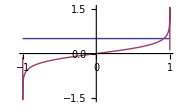

```mathematica
FPCauchyBasis[+1,UnitInterval,1,g//ToUnitInterval]
```

```mathematica
Timing[Table[RightSingularityDataBasis[+1,UnitInterval,k];,{k,Length[hf]}]]
```

{0.008834,{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
Table[PadRight[4 Riffle[Reverse[Table[1/j,{j,1,k-1,2}]],0]//(If[OddQ[k],Join[{0},#],#]&),10],{k,11}]//Transpose//MatrixForm
```

(0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9 | 0
0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9
0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0
0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7
0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4)

```mathematica
?ToeplitzMatrix
```

ToeplitzMatrix[n] gives the n×n Toeplitz matrix with first row and first column being successive integers.
ToeplitzMatrix[{c_1,c_2,…,c_n}] gives the Toeplitz matrix whose first column consists of elements c_1, c_2, ….
ToeplitzMatrix[{c_1,c_2,…,c_m},{r_1,r_2,…, r_n}] gives the Toeplitz matrix with elements c_i down the first column, and r_i across the first row.

```mathematica
(mat=With[{k=10},
)//MatrixForm
```

(0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0 | 4/9
0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7 | 0
0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0 | 4/7
0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0 | 4/5
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

ColumnMap[Private`f_,Private`m_?VectorQ]:=Transpose[Private`f/@Private`m]
 
ColumnMap[Private`f_,Private`m_?MatrixQ]:=Transpose[Private`f/@Transpose[Private`m]]

```mathematica
-2/(I π)ArcTanh[IntervalToBottomCircle[Points[g//ToUnitInterval]//Rest//Most]](InverseDCT[BasisVector[Length[g]][1]]//Rest//Most)-(FPCauchyBasis[+1,UnitInterval,1,g//ToUnitInterval]//Values//Most//Rest)//Norm
```

2.37258×10^-15

```mathematica
With[{k=4},-2/(I π)ArcTanh[IntervalToBottomCircle[Points[g//ToUnitInterval]//Rest//Most]](InverseDCT[BasisVector[Length[g]][k]]//Rest//Most)+Most[Rest[dctmat⟦All,k⟧/(2 I π)]]-(FPCauchyBasis[+1,UnitInterval,k,g//ToUnitInterval]//Values//Most//Rest)//Chop]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FPCauchyBasis[+1,hf//ToUnitInterval,;;20,hf//ToUnitInterval]-Table[FPCauchyBasis[+1,hf//ToUnitInterval,k,hf//ToUnitInterval],{k,20}]//Chop
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FPCauchyBasis[-1,hf//ToUnitInterval,;;20,hf//ToUnitInterval]-Table[FPCauchyBasis[-1,hf//ToUnitInterval,k,hf//ToUnitInterval],{k,20}]//Chop
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Timing[n=100;
mat=ToeplitzMatrix[ZeroVector[n],
4 Riffle[Table[1/j,{j,1,n-1,2}],0]//(Join[{0},If[OddQ[n],Join[#,{0}],#]]&)];
dctmat=ColumnMap[InverseDCT[PadRight[HalfFirst[#],g//Length]]&,mat];

Join[{Table[LeftSingularityDataBasis[+1,UnitInterval,k]//First,{k,n}]},-2/(I π)ArcTanh[IntervalToBottomCircle[g//ToUnitInterval//Points//Rest//Most]] ColumnMap[(#//InverseDCT//Rest//Most)&,IdentityMatrix[{Length[g],n}]]+ColumnMap[(#//Rest//Most)&,dctmat]/(2 I π),
{Table[RightSingularityDataBasis[+1,UnitInterval,k]//First,{k,n}]}
];]
```

{0.304834,Null}

```mathematica
n=5;
mat=ToeplitzMatrix[ZeroVector[n],
4 Riffle[Table[1/j,{j,1,n-1,2}],0]//(Join[{0},If[OddQ[n],Join[#,{0}],#]]&)];
dctmat=ColumnMap[InverseDCT[PadRight[HalfFirst[#],g//Length]]&,mat];

Join[{Table[LeftSingularityDataBasis[+1,UnitInterval,k]//First,{k,n}]},-2/(I π)ArcTanh[IntervalToBottomCircle[g//ToUnitInterval//Points//Rest//Most]] ColumnMap[(#//InverseDCT//Rest//Most)&,IdentityMatrix[{Length[g],n}]]+ColumnMap[(#//Rest//Most)&,dctmat]/(2 I π),
{Table[RightSingularityDataBasis[+1,UnitInterval,k]//First,{k,n}]}
]-Transpose[Table[(FPCauchyBasis[+1,UnitInterval,k,g//ToUnitInterval]//Values),{k,n}]]//Norm
```

4.63882×10^-15

```mathematica
Table[LeftSingularityDataBasis[+1,UnitInterval,k]//First,{k,n}]
```

{0.5-0.110318 ⅈ,-0.5-0.207992 ⅈ,0.5+0.526302 ⅈ,-0.5-0.632405 ⅈ,0.5+0.738509 ⅈ}

```mathematica
Transpose[Table[(FPCauchyBasis[+1,UnitInterval,k,g//ToUnitInterval]//Values//Most//First),{k,n}]]
```

Transpose::nmtx: The first two levels of the one-dimensional list {0.5`  - 0.1103178000763258` ⅈ, -0.5` - 0.2079920861074649` ⅈ, 0.5`  + 0.5263019722912556` ⅈ, -0.5` - 0.6324052676858525` ⅈ, 0.5`  + 0.7385085630804495` ⅈ} cannot be transposed.

Transpose[{0.5-0.110318 ⅈ,-0.5-0.207992 ⅈ,0.5+0.526302 ⅈ,-0.5-0.632405 ⅈ,0.5+0.738509 ⅈ}]

```mathematica
//
```

```mathematica
Timing[
mat=ToeplitzMatrix[ZeroVector[n],
4 Riffle[Table[1/j,{j,1,n-1,2}],0]//(Join[{0},If[OddQ[n],Join[#,{0}],#]]&)];
dctmat=ColumnMap[InverseDCT[PadRight[HalfFirst[#],g//Length]]&,mat];

Join[Table[LeftSingularityDataBasis[UnitInterval,k],{k,n}],-2/(I π)ArcTanh[IntervalToBottomCircle[g//ToUnitInterval//Points//Rest//Most]] ColumnMap[(#//InverseDCT//Rest//Most)&,IdentityMatrix[{Length[g],n}]]+ColumnMap[(#//Rest//Most)&,dctmat]/(2 I π)
];]
```

{0.020896,Null}

```mathematica
Timing[Transpose[Table[(FPCauchyBasis[+1,UnitInterval,k,g//ToUnitInterval]//Values//Most//Rest)//Chop,{k,n}]];]
```

{0.05775,Null}

```mathematica
-2/(I π)ArcTanh[IntervalToBottomCircle[g//ToUnitInterval//Points//Rest//Most]] ColumnMap[(#//InverseDCT//Rest//Most)&,IdentityMatrix[{Length[g],n}]]+ColumnMap[(#//Rest//Most)&,dctmat]/(2 I π)-Transpose[Table[(FPCauchyBasis[+1,UnitInterval,k,g//ToUnitInterval]//Values//Most//Rest)//Chop,{k,n}]]//Norm
```

4.63882×10^-15

```mathematica
//Dimensions
```

{198,5}

### HalfLine

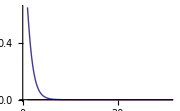

```mathematica
hf
```

```mathematica
FPCauchyBasis//Clear
```

```mathematica
(FPCauchyBasis[+1,hf,1;;20,hf];)//Timing
```

{0.041549,Null}

```mathematica
Timing[Table[FPCauchyBasis[+1,hf,k,hf],{k,20}];]
```

{0.200699,Null}

```mathematica
Last[FPCauchyBasis[+1,hf,1;;Length[hf],hf]]-FPCauchyBasis[+1,hf,Length[hf],hf]//Values//Norm
```

9.44669×10^-15

```mathematica
Values/@(FPCauchyBasis[+1,hf,1;;Length[hf],hf]-Table[FPCauchyBasis[+1,hf,k,hf],{k,Length[hf]}])//Flatten//Abs//Max
```

1.27906×10^-13

```mathematica
Values/@(FPCauchyBasis[+1,hf//ReverseOrientation,1;;Length[hf],hf//ReverseOrientation]-Table[FPCauchyBasis[+1,hf//ReverseOrientation,k,hf//ReverseOrientation],{k,Length[hf]}])//Flatten//Abs//Max
```

1.27906×10^-13

```mathematica
FPCauchyBasis[+1,if3,;;3,if3]
```

FourierDCT::fftl: Argument … is not a non-empty list or rectangular array of numeric quantities.

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 π ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

-Graphics-

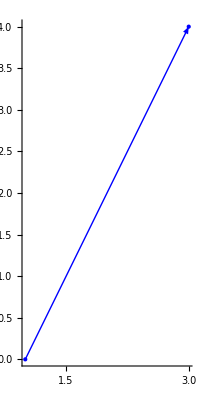

```mathematica
{if3}//DomainPlot
```

```mathematica
CauchyBasis//Clear
```

{0,0. ⅈ,0. ⅈ}

```mathematica
({{a, b}, {c, d}})-{e,aa}
```

{{a-e,b-e},{-aa+c,-aa+d}}

```mathematica
Values/@(FPCauchyBasis[+1,if3,;;Length[if3],if3]-Table[FPCauchyBasis[+1,if3,k,if3],{k,Length[if3]}])//Norm
```

7.36575×10^-14

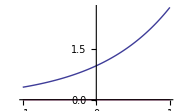
FPCauchyBasis[1,Line[{1.,3.+4. ⅈ}],1;;52,-Graphics-]

```mathematica
FPCauchyBasis[+1,if3,;;Length[if3],if]
```

### Endpoints equal

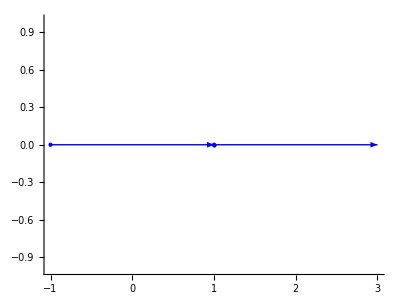

```mathematica
{if,hf}//DomainPlot
```

```mathematica
FPCauchyBasis[+1,if,1;;Length[if],ReverseOrientation[hf]]
```

```mathematica
Values/@(FPCauchyBasis[+1,if,1;;Length[if],ReverseOrientation[hf]]-Table[FPCauchyBasis[+1,if,k,ReverseOrientation[hf]],{k,Length[if]}])//Norm
```

3.14156×10^-9

```mathematica
Values/@(FPCauchyBasis[+1,if//ReverseOrientation,1;;Length[if],hf]-Table[FPCauchyBasis[+1,if//ReverseOrientation,k,hf],{k,Length[if]}])//Norm
```

3.14156×10^-9

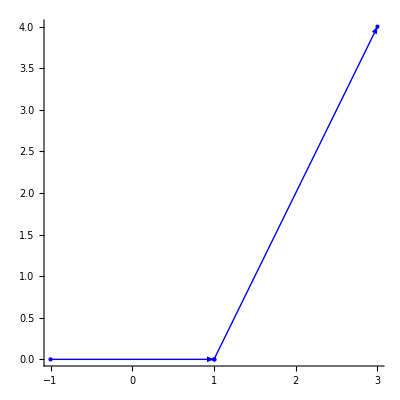

```mathematica
{if,if3}//DomainPlot
```

```mathematica
Values/@(FPCauchyBasis[+1,if,1;;Length[if],if3//ReverseOrientation]-Table[FPCauchyBasis[+1,if,k,if3//ReverseOrientation],{k,Length[if]}])//Norm
```

1.04484×10^-9

```mathematica
Values/@(FPCauchyBasis[+1,if,1;;Length[if],if3]-Table[FPCauchyBasis[+1,if,k,if3],{k,Length[if]}])//Norm
```

1.04484×10^-9

```mathematica
Values/@(FPCauchyBasis[+1,if//ReverseOrientation,1;;Length[if],if3//ReverseOrientation]-Table[FPCauchyBasis[+1,if//ReverseOrientation,k,if3//ReverseOrientation],{k,Length[if]}])//Norm
```

1.04629×10^-9

```mathematica
Values/@(FPCauchyBasis[+1,if//ReverseOrientation,1;;Length[if],if3]-Table[FPCauchyBasis[+1,if//ReverseOrientation,k,if3],{k,Length[if]}])//Norm
```

1.04629×10^-9

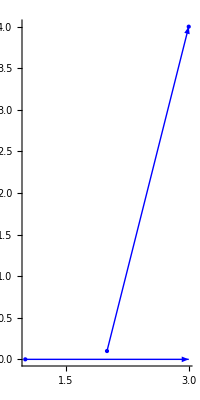

```mathematica
{hf,if2}//DomainPlot
```

```mathematica
Values/@(FPCauchyBasis[+1,if2,1;;Length[if2],hf//ReverseOrientation]-Table[FPCauchyBasis[+1,if2,k,hf//ReverseOrientation],{k,Length[if2]}])//Norm
```

1.16225×10^-15

```mathematica
Values/@(FPCauchyBasis[+1,if2,1;;Length[if2],hf]-Table[FPCauchyBasis[+1,if2,k,hf],{k,Length[if2]}])//Norm
```

1.16225×10^-15

```mathematica
Values/@(FPCauchyBasis[+1,if2,1;;Length[if2],if]-Table[FPCauchyBasis[+1,if2,k,if],{k,Length[if2]}])//Norm
```

7.5545×10^-16

#### Test Numerical vale

```mathematica
With[{f=if,g=hf,k=3},
Join[{First/@RightSingularityDataBasis[f,;;k,LeftContourArg[g]]},
CauchyBasis[f,;;k,g//Points//Rest//Most],
{ZeroMatrix[k]}]]
```

{{0.+0.110318 ⅈ,0.-0.207992 ⅈ,0.-0.526302 ⅈ},{1.37694 ⅈ,1.15627 ⅈ,1.02716 ⅈ,0.935528 ⅈ,0.864416 ⅈ,0.80628 ⅈ,0.757093 ⅈ,0.714451 ⅈ,0.676805 ⅈ,0.643095 ⅈ,0.612566 ⅈ,0.584663 ⅈ,0.558961 ⅈ,0.535132 ⅈ,0.512915 ⅈ,0.4921 ⅈ,0.472516 ⅈ,0.454021 ⅈ,0.436495 ⅈ,0.419839 ⅈ,0.403967 ⅈ,0.388805 ⅈ,0.37429 ⅈ,0.360366 ⅈ,0.346986 ⅈ,0.334106 ⅈ,0.321689 ⅈ,0.309701 ⅈ,0.298114 ⅈ,0.2869 ⅈ,0.276037 ⅈ,0.265502 ⅈ,0.255277 ⅈ,0.245344 ⅈ,0.235689 ⅈ,0.226296 ⅈ,0.217155 ⅈ,0.208253 ⅈ,0.19958 ⅈ,0.191127 ⅈ,0.182886 ⅈ,0.17485 ⅈ,0.167011 ⅈ,0.159365 ⅈ,0.151905 ⅈ,0.144628 ⅈ,0.13753 ⅈ,0.130607 ⅈ,0.123857 ⅈ,0.117277 ⅈ,0.110865 ⅈ,0.10462 ⅈ,0.098542 ⅈ,0.0926293 ⅈ,0.086882 ⅈ,0.0813004 ⅈ,0.0758851 ⅈ,0.0706369 ⅈ,0.065557 ⅈ,0.0606468 ⅈ,0.0559081 ⅈ,0.0513428 ⅈ,0.046953 ⅈ,0.0427411 ⅈ,0.0387097 ⅈ,0.0348613 ⅈ,0.0311988 ⅈ,0.0277249 ⅈ,0.0244425 ⅈ,0.0213547 ⅈ,0.0184643 ⅈ,0.0157742 ⅈ,0.0132872 ⅈ,0.0110062 ⅈ,0.00893359 ⅈ,0.00707197 ⅈ,0.0054236 ⅈ,0.00399056 ⅈ,0.0027747 ⅈ,0.00177765 ⅈ,0.00100074 ⅈ,0.00044503 ⅈ,0.000111296 ⅈ},{1.05911 ⅈ,0.839584 ⅈ,0.712094 ⅈ,0.622472 ⅈ,0.553707 ⅈ,0.498206 ⅈ,0.451905 ⅈ,0.412372 ⅈ,0.378033 ⅈ,0.347808 ⅈ,0.320925 ⅈ,0.296811 ⅈ,0.275031 ⅈ,0.255243 ⅈ,0.237176 ⅈ,0.220612 ⅈ,0.20537 ⅈ,0.191301 ⅈ,0.17828 ⅈ,0.166199 ⅈ,0.154967 ⅈ,0.144506 ⅈ,0.134747 ⅈ,0.12563 ⅈ,0.117104 ⅈ,0.109121 ⅈ,0.10164 ⅈ,0.0946251 ⅈ,0.0880423 ⅈ,0.0818624 ⅈ,0.0760586 ⅈ,0.0706065 ⅈ,0.0654842 ⅈ,0.0606715 ⅈ,0.05615 ⅈ,0.0519029 ⅈ,0.0479146 ⅈ,0.0441708 ⅈ,0.0406583 ⅈ,0.0373647 ⅈ,0.0342786 ⅈ,0.0313893 ⅈ,0.0286868 ⅈ,0.0261617 ⅈ,0.0238052 ⅈ,0.0216089 ⅈ,0.019565 ⅈ,0.017666 ⅈ,0.0159047 ⅈ,0.0142743 ⅈ,0.0127682 ⅈ,0.0113803 ⅈ,0.0101045 ⅈ,0.00893483 ⅈ,0.00786577 ⅈ,0.00689181 ⅈ,0.00600761 ⅈ,0.00520799 ⅈ,0.00448788 ⅈ,0.00384234 ⅈ,0.00326653 ⅈ,0.00275572 ⅈ,0.00230529 ⅈ,0.00191073 ⅈ,0.00156762 ⅈ,0.00127165 ⅈ,0.00101865 ⅈ,0.00080454 ⅈ,0.000625389 ⅈ,0.000477403 ⅈ,0.000356941 ⅈ,0.000260526 ⅈ,0.000184862 ⅈ,0.000126843 ⅈ,0.0000835714 ⅈ,0.0000523715 ⅈ,0.0000308032 ⅈ,0.000016676 ⅈ,8.0623×10^-6 ⅈ,3.30917×10^-6 ⅈ,1.04874×10^-6 ⅈ,2.07399×10^-7 ⅈ,1.29715×10^-8 ⅈ},{0.742022 ⅈ,0.525244 ⅈ,0.401516 ⅈ,0.316408 ⅈ,0.252737 ⅈ,0.202782 ⅈ,0.162383 ⅈ,0.12903 ⅈ,0.101088 ⅈ,0.0774244 ⅈ,0.057226 ⅈ,0.0398842 ⅈ,0.0249324 ⅈ,0.0120046 ⅈ,0.000808164 ⅈ,-0.0088949 ⅈ,-0.0173005 ⅈ,-0.0245719 ⅈ,-0.0308467 ⅈ,-0.0362417 ⅈ,-0.0408572 ⅈ,-0.0447793 ⅈ,-0.0480833 ⅈ,-0.0508346 ⅈ,-0.0530908 ⅈ,-0.0549025 ⅈ,-0.0563148 ⅈ,-0.0573677 ⅈ,-0.058097 ⅈ,-0.0585347 ⅈ,-0.0587096 ⅈ,-0.0586479 ⅈ,-0.058373 ⅈ,-0.0579063 ⅈ,-0.0572674 ⅈ,-0.0564739 ⅈ,-0.0555421 ⅈ,-0.0544871 ⅈ,-0.0533224 ⅈ,-0.0520607 ⅈ,-0.0507138 ⅈ,-0.0492925 ⅈ,-0.0478068 ⅈ,-0.046266 ⅈ,-0.044679 ⅈ,-0.0430537 ⅈ,-0.0413978 ⅈ,-0.0397185 ⅈ,-0.0380225 ⅈ,-0.036316 ⅈ,-0.0346049 ⅈ,-0.0328948 ⅈ,-0.0311911 ⅈ,-0.0294986 ⅈ,-0.0278221 ⅈ,-0.026166 ⅈ,-0.0245345 ⅈ,-0.0229315 ⅈ,-0.021361 ⅈ,-0.0198262 ⅈ,-0.0183308 ⅈ,-0.0168777 ⅈ,-0.0154699 ⅈ,-0.0141104 ⅈ,-0.0128017 ⅈ,-0.0115462 ⅈ,-0.0103464 ⅈ,-0.00920427 ⅈ,-0.00812191 ⅈ,-0.00710116 ⅈ,-0.00614372 ⅈ,-0.00525118 ⅈ,-0.00442497 ⅈ,-0.00366638 ⅈ,-0.00297661 ⅈ,-0.0023567 ⅈ,-0.00180759 ⅈ,-0.00133007 ⅈ,-0.000924863 ⅈ,-0.000592539 ⅈ,-0.000333577 ⅈ,-0.000148343 ⅈ,-0.0000370988 ⅈ},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
FPCauchyBasis//Clear
```

```mathematica
Domain[if]~NEqual~Domain[hf]
```

Abs[Line[{-1.,1.}]-Line[{1.,∞}]]<2.22045×10^-14

```mathematica
hf//RightEndpointInfinityQ
```

True

```mathematica
?RightJoin
```

Common`RightJoin

RightJoin[v__]:=Transpose[Join@@VectorTranspose/@{v}]

```mathematica
Transpose[CauchyBasis[if,;;3,g//Points//Rest//Most]]//Dimensions
```

{198,3}

```mathematica
First/@RightSingularityDataBasis[f,;;3,LeftContourArg[g]]
```

{0.125+0.110318 ⅈ,0.125-0.207992 ⅈ,0.125-0.526302 ⅈ}

```mathematica
Join[{First/@RightSingularityDataBasis[f,;;3,LeftContourArg[g]]},Transpose[CauchyBasis[if,;;3,g//Points//Rest//Most]],
{ZeroVector[3]}
]
```

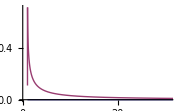
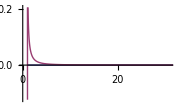
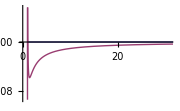

```mathematica
With[{f=if//Domain,g=hf,k=3},
IFun[#,g//Domain]&/@Transpose[Join[{First/@RightSingularityDataBasis[f,;;k,LeftContourArg[g]]},
Transpose[CauchyBasis[f,;;k,g//Points//Rest//Most]],
{ZeroVector[k]}]]]
```

```mathematica
(Values/@(FPCauchyBasis[+1,if,1;;Length[if],hf]-Table[FPCauchyBasis[+1,if,k,hf],{k,Length[if]}]))//Norm
```

8.83363×10^-14

```mathematica
LeftSingularityDataBasis[if//ReverseOrientation,;;3,RightContourArg[hf//ReverseOrientation]]
```

{{0.-0.110318 ⅈ,ⅈ/(2 π)},{0.-0.207992 ⅈ,-ⅈ/(2 π)},{0.+0.526302 ⅈ,ⅈ/(2 π)}}

```mathematica
FPCauchyBasis[+1,if//ReverseOrientation,1;;Length[if],hf//ReverseOrientation]
```

```mathematica
if//Length
```

100

```mathematica
CauchyBasis[if//ReverseOrientation,;;k,g//Points//Rest//Most]
```

```mathematica
hf//ReverseOrientation//Points//Second
```

2860.02

```mathematica
n=86;((CauchyBasis[if,1;;n,hf//ReverseOrientation//Points//Second]-Table[CauchyBasis[if,k,hf//ReverseOrientation//Points//Second],{k,n}]))//Norm
```

6.11749×10^-17

```mathematica
if//ReverseOrientation//Domain
```

```mathematica
ψpL[-86;;86,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]]
```

```mathematica
IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,SetPrecision[hf//ReverseOrientation//Points//Second,100]]]
```

-0.000174824+0. ⅈ

2.05675×10^-6+0. ⅈ

```mathematica
Last[ψpL[;;85,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]]]-ψp[85,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]]//Chop
```

0

```mathematica
Last[ψpL[;;85,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]]]-ψpH[85,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]]//Chop
```

0

```mathematica
ψpL[;;86,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]]-Table[ψp[k,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,SetPrecision[hf//ReverseOrientation//Points//Second,100]]]],{k,86}]//Chop//Norm
```

0

```mathematica
n=86;((CauchyBasis[UnitInterval,1;;n,MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]-Table[CauchyBasis[UnitInterval,k,MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]],{k,n}]))//Chop//Norm
```

0

```mathematica
n=86;((CauchyBasis[UnitInterval,1;;n,MapToInterval[if//ReverseOrientation,hf//ReverseOrientation//Points//Second]]-Table[CauchyBasis[if//ReverseOrientation,k,hf//ReverseOrientation//Points//Second],{k,n}]))//Norm//Chop
```

0

```mathematica
Thread[{hf//ReverseOrientation//Points//Most//Rest,Last[CauchyBasis[if//ReverseOrientation,1;;n,hf//ReverseOrientation//Points//Most//Rest]]-CauchyBasis[if//ReverseOrientation,n,SetPrecision[hf//ReverseOrientation//Points//Most//Rest,100]]}]//Chop
```

{{2860.02,0},{715.256,0},{318.077,0},{179.064,0},{114.721,0},{79.77,0},{58.6955,0},{45.0175,0},{35.64,0},{28.9326,0},{23.97,0},{20.1957,0},{17.2585,0},{14.9282,0},{13.0484,0},{11.51,0},{10.2353,0},{9.16723,0},{8.2635,0},{7.49209,0},{6.82843,0},{6.25338,0},{5.75188,0},{5.31194,0},{4.92393,0},{4.58001,0},{4.2738,0},{4.,0},{3.75424,0},{3.53284,0},{3.33273,0},{3.1513,0},{2.98632,0},{2.83589,0},{2.6984,0},{2.57242,0},{2.45674,0},{2.35029,0},{2.25216,0},{2.16153,0},{2.07769,0},{2.,0},{1.92791,0},{1.86093,0},{1.79862,0},{1.74058,0},{1.68647,0},{1.63596,0},{1.58879,0},{1.54469,0},{1.50344,0},{1.46484,0},{1.42868,0},{1.39481,0},{1.36308,0},{1.33333,0},{1.30546,0},{1.27933,0},{1.25485,0},{1.23191,0},{1.21044,0},{1.19035,0},{1.17157,0},{1.15403,0},{1.13767,0},{1.12244,0},{1.10828,0},{1.09515,0},{1.083,0},{1.0718,0},{1.06151,0},{1.0521,-2.84733×10^-9+2.24038×10^-10 ⅈ},{1.04354,-1.19025×10^-10},{1.0358,0},{1.02887,0},{1.02272,0},{1.01733,0},{1.0127,0},{1.00879,0},{1.00562,0},{1.00315,0},{1.0014,0},{1.00035,0}}

```mathematica
Last[ψpL[;;n,IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,1.0520950836016871]]]]-ψpH[n,SetPrecision[IntervalToInnerCircle[MapToInterval[if//ReverseOrientation,1.0520950836016871]],100]]//Chop
```

0

```mathematica
n=100;((CauchyBasis[if//ReverseOrientation,1;;n,hf//ReverseOrientation//Points//Most//Rest]-Table[CauchyBasis[if//ReverseOrientation,k,hf//ReverseOrientation//Points//Most//Rest],{k,n}]))//Norm
```

3.14156×10^-9

```mathematica
(Values/@(FPCauchyBasis[+1,if//ReverseOrientation,1;;100,hf//ReverseOrientation]-Table[FPCauchyBasis[+1,if//ReverseOrientation,k,hf//ReverseOrientation],{k,100}]))//Last
```

{0,0.-5.5218×10^-17 ⅈ,0.-5.35614×10^-17 ⅈ,6.9649×10^-288-5.41136×10^-17 ⅈ,-7.0705×10^-254+6.07398×10^-18 ⅈ,7.7694×10^-35-7.84095×10^-17 ⅈ,-7.76956×10^-35-7.6753×10^-17 ⅈ,-7.76982×10^-35-4.19657×10^-17 ⅈ,-1.65035×10^-194-8.89009×10^-17 ⅈ,7.77078×10^-35-5.68745×10^-17 ⅈ,-1.70818×10^-175-7.17834×10^-17 ⅈ,-7.77264×10^-35+2.31915×10^-17 ⅈ,1.5548×10^-34-5.57701×10^-17 ⅈ,7.77579×10^-35-8.22748×10^-17 ⅈ,-5.2308×10^-147-9.00053×10^-17 ⅈ,7.78071×10^-35-1.22032×10^-16 ⅈ,7.784×10^-35-2.81611×10^-17 ⅈ,-1.00005×10^-130-2.98177×10^-17 ⅈ,7.79257×10^-35-1.24793×10^-16 ⅈ,-7.79801×10^-35+2.31916×10^-17 ⅈ,-3.19211×10^-117-3.09221×10^-17 ⅈ,-3.40138×10^-113-5.79789×10^-17 ⅈ,7.81989×10^-35-1.19823×10^-16 ⅈ,-1.01039×10^-105-4.63829×10^-17 ⅈ,7.83997×10^-35-5.13526×10^-17 ⅈ,-6.43434×10^-99+9.38724×10^-18 ⅈ,-9.84063×10^-96-5.30092×10^-17 ⅈ,7.88017×10^-35-5.63224×10^-17 ⅈ,-7.89665×10^-35-5.46658×10^-17 ⅈ,7.91486×10^-35-5.46654×10^-17 ⅈ,-3.31889×10^-84-5.46658×10^-17 ⅈ,7.95689×10^-35-5.63222×10^-17 ⅈ,-7.98097×10^-35-5.52177×10^-17 ⅈ,-1.31188×10^-76-5.46658×10^-17 ⅈ,-8.03591×10^-35-5.63218×10^-17 ⅈ,-5.97241×10^-72-5.57703×10^-17 ⅈ,-9.95845×10^-70-5.74263×10^-17 ⅈ,8.13752×10^-35-5.68749×10^-17 ⅈ,-1.7742×10^-65-5.6874×10^-17 ⅈ,8.22006×10^-35-5.85317×10^-17 ⅈ,8.26637×10^-35-5.90839×10^-17 ⅈ,-8.31633×10^-35-5.74271×10^-17 ⅈ,-1.19169×10^-57-5.85317×10^-17 ⅈ,8.42827×10^-35-5.90839×10^-17 ⅈ,-5.01736×10^-54-5.853×10^-17 ⅈ,-2.81381×10^-52-5.90839×10^-17 ⅈ,8.63072×10^-35-5.96345×10^-17 ⅈ,8.70884×10^-35-6.0739×10^-17 ⅈ,-8.79299×10^-35-6.12913×10^-17 ⅈ,-1.18175×10^-45-6.01868×10^-17 ⅈ,8.98143×10^-35-6.18436×10^-17 ⅈ,-1.53904×10^-42-6.40526×10^-17 ⅈ,1.84015×10^-34-6.29481×10^-17 ⅈ,-1.54305×10^-39-6.57094×10^-17 ⅈ,-9.46138×10^-35-6.62583×10^-17 ⅈ,9.47882×10^-35-6.73628×10^-17 ⅈ,1.63376×10^-34-6.73628×10^-17 ⅈ,-1.89703×10^-34-6.95787×10^-17 ⅈ,-9.18598×10^-36-7.1781×10^-17 ⅈ,-2.94081×10^-35-7.23366×10^-17 ⅈ,-2.60602×10^-35-7.34411×10^-17 ⅈ,-2.52764×10^-34-7.67615×10^-17 ⅈ,-1.7336×10^-35-7.84014×10^-17 ⅈ,-1.65664×10^-34-7.8957×10^-17 ⅈ,-1.70518×10^-34-8.33751×10^-17 ⅈ,-7.71124×10^-36-8.50421×10^-17 ⅈ,-6.54515×10^-35-8.72512×10^-17 ⅈ,-1.44445×10^-34-9.16693×10^-17 ⅈ,-5.29631×10^-34-9.38648×10^-17 ⅈ,-3.23556×10^-32-1.0159×10^-16 ⅈ,-4.31408×10^-31-1.07119×10^-16 ⅈ,-4.93038×10^-30-1.11564×10^-16 ⅈ,-2.84733×10^-9+2.24038×10^-10 ⅈ,-1.19025×10^-10-5.23899×10^-11 ⅈ,-3.01798×10^-11+2.32638×10^-11 ⅈ,-1.48472×10^-11+4.17078×10^-12 ⅈ,3.82652×10^-11+2.41167×10^-12 ⅈ,-8.32029×10^-12+6.36844×10^-13 ⅈ,2.91484×10^-12+1.2614×10^-14 ⅈ,3.87111×10^-14+1.46814×10^-14 ⅈ,4.08235×10^-14+1.26735×10^-14 ⅈ,-1.05987×10^-14-1.04691×10^-15 ⅈ,-3.70363×10^-16-1.0339×10^-15 ⅈ,-5.13478×10^-16-1.51962×10^-15 ⅈ,0.+0. ⅈ}

```mathematica
%//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.84733×10^-9+2.24038×10^-10 ⅈ,-1.19025×10^-10,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
if//Length
```

100

```mathematica
Timing[FPCauchyBasis[+1,if//ReverseOrientation,1;;90,hf//ReverseOrientation];]
```

{0.107351,Null}

```mathematica
ψpS//Clear
```

```mathematica
ψpL[0;;20,0.1+0.1 I]
```

{0.0993254+0.100659 ⅈ,-1.00013+0.0199984 ⅈ,-0.102013-0.0980135 ⅈ,-0.333733-0.0200027 ⅈ,-0.0313731-0.0353736 ⅈ,-0.1996-0.00667467 ⅈ,-0.0192925-0.0206275 ⅈ,-0.142724-0.003992 ⅈ,-0.0138732-0.0146716 ⅈ,-0.111031-0.00285447 ⅈ,-0.0108177-0.0113886 ⅈ,-0.090852-0.00222063 ⅈ,-0.00886314-0.00930726 ⅈ,-0.0768787-0.00181704 ⅈ,-0.00750616-0.00786957 ⅈ,-0.0666303-0.00153757 ⅈ,-0.00650928-0.00681679 ⅈ,-0.0587928-0.00133261 ⅈ,-0.00574602-0.00601254 ⅈ,-0.0526049-0.00117586 ⅈ,-0.00514291-0.00537808 ⅈ}

```mathematica
ψpL[0;;20,0.1+0.1 I]-%1857
```

{0.+0. ⅈ,-4.44089×10^-16-3.46945×10^-17 ⅈ,-4.16334×10^-17-6.93889×10^-17 ⅈ,0.-1.04083×10^-17 ⅈ,6.93889×10^-18-6.93889×10^-18 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
ψpL//Clear
```

```mathematica
hf//Length
```

85

## Cauchy Matrix Span

```mathematica
OldCauchyMatrix[s_,f_,g_]:=Transpose[Array[FiniteValues[FPCauchyBasis[+1,f,#,g]]&,Length[f]]].FiniteTransformMatrix[f];
```

```mathematica
CauchyMatrix[+1,if,if]-OldCauchyMatrix[+1,if,if]//Norm
```

1.34175×10^-13

```mathematica
CauchyMatrix[+1,if,if2]-OldCauchyMatrix[+1,if,if2]//Norm
```

2.42461×10^-16

```mathematica
CauchyMatrix[+1,if,if3]-OldCauchyMatrix[+1,if,if3]//Norm
```

1.20265×10^-10

```mathematica
CauchyMatrix[+1,if,hf]-OldCauchyMatrix[+1,if,hf]//Norm
```

3.41329×10^-10

```mathematica
{Timing[CauchyMatrix[+1,if,if3];],Timing[OldCauchyMatrix[+1,if,if3];]}
```

{{0.208316,Null},{6.29482,Null}}

```mathematica
{Timing[CauchyMatrix[+1,if,hf];],Timing[OldCauchyMatrix[+1,if,hf];]}
```

{{0.916913,Null},{5.22277,Null}}

{{0.5+1.43842 ⅈ,-6.85216×10^-17-0.37526 ⅈ,-1.47451×10^-17-0.14363 ⅈ,-7.80626×10^-18-0.113051 ⅈ,«93»,6.93889×10^-18-0.000177242 ⅈ,9.62772×10^-17-0.0000620021 ⅈ,8.23994×10^-18-0.0000162386 ⅈ},«98»,{«1»}}

## Example Testing

-0.0826569+0.5 ⅈ

```mathematica
CauchyMatrix[+1,GG⟦1⟧⟦2,1⟧,GG⟦1⟧⟦2,1⟧].ToValueList[GG⟦1⟧⟦2,1⟧]-Join[{First[LeftSingularityData[+1,GG⟦1⟧⟦2,1⟧]]},Cauchy[+1,GG⟦1⟧⟦2,1⟧,FinitePoints[GG⟦1⟧⟦2,1⟧]//Rest]]//Norm
```

3.37614×10^-15

```mathematica
CauchyMatrix[+1,GG⟦1⟧⟦2,1⟧,GG⟦2⟧⟦2,1⟧].ToValueList[GG⟦1⟧⟦2,1⟧]-Join[{First[LeftSingularityData[GG⟦1⟧⟦2,1⟧,GG⟦2⟧⟦2,1⟧//LeftContourArg]]},Cauchy[GG⟦1⟧⟦2,1⟧,FinitePoints[GG⟦2⟧⟦2,1⟧]//Rest]]//Norm
```

2.67139×10^-15

```mathematica
CauchyMatrix[+1,GG⟦1⟧⟦2,1⟧,GG⟦3⟧⟦2,1⟧].ToValueList[GG⟦1⟧⟦2,1⟧]-Join[{First[LeftSingularityData[GG⟦1⟧⟦2,1⟧,GG⟦3⟧⟦2,1⟧//LeftContourArg]]},Cauchy[GG⟦1⟧⟦2,1⟧,FinitePoints[GG⟦3⟧⟦2,1⟧]//Rest]]//Norm
```

2.58155×10^-15

```mathematica
CauchyMatrix[+1,GG⟦1⟧⟦2,1⟧,GG⟦4⟧⟦2,1⟧].ToValueList[GG⟦1⟧⟦2,1⟧]-Join[{First[LeftSingularityData[GG⟦1⟧⟦2,1⟧,GG⟦4⟧⟦2,1⟧//LeftContourArg]]},Cauchy[GG⟦1⟧⟦2,1⟧,FinitePoints[GG⟦4⟧⟦2,1⟧]//Rest]]//Norm
```

2.94968×10^-15

```mathematica
ComplexContourNIntegrate[s[1]Exp[θ[0.,z]]/(z-FinitePoints[GG⟦4⟧⟦2,1⟧]//Rest//First),{z,Exp[I π/6] t},{t,0,∞}]/(2 π I)
```

1.01214-0.333067 ⅈ

```mathematica
Cauchy[GG⟦1⟧⟦2,1⟧,FinitePoints[GG⟦4⟧⟦2,1⟧]//Rest//First]
```

1.01214-0.333067 ⅈ

```mathematica
CauchyMatrix[+1,GG⟦1⟧⟦1,1⟧,GG⟦1⟧⟦1,1⟧].ToValueList[GG⟦1⟧⟦1,1⟧]-OldCauchyMatrix[+1,GG⟦1⟧⟦1,1⟧,GG⟦1⟧⟦1,1⟧].ToValueList[GG⟦1⟧⟦1,1⟧]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TransformMatrix[GG⟦1⟧⟦1,1⟧].Values[GG⟦1⟧⟦1,1⟧]-ColumnMap[DCT,IdentityMatrix[Length[GG⟦1⟧⟦1,1⟧]]].Values[GG⟦1⟧⟦1,1⟧]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TransformMatrix[GG⟦1⟧⟦1,1⟧].Values[GG⟦1⟧⟦2,1⟧]-ColumnMap[DCT,IdentityMatrix[Length[GG⟦1⟧⟦2,1⟧]]].Values[GG⟦1⟧⟦2,1⟧]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
TransformMatrix[GG⟦1⟧⟦1,1⟧].Values[GG⟦1⟧⟦2,1⟧]//Chop
```

{0.420345 ⅈ,-0.605275 ⅈ,0.139546 ⅈ,0.134326 ⅈ,-0.0957934 ⅈ,-0.0345918 ⅈ,0.0549474 ⅈ,0.00500818 ⅈ,-0.0288227 ⅈ,0.00200852 ⅈ,0.0148191 ⅈ,-0.00265134 ⅈ,-0.00769753 ⅈ,0.00191191 ⅈ,0.00409618 ⅈ,-0.00114415 ⅈ,-0.00224221 ⅈ,0.000610751 ⅈ,0.00125885 ⅈ,-0.000290677 ⅈ,-0.000719378 ⅈ,0.000115424 ⅈ,0.000414135 ⅈ,-0.0000275979 ⅈ,-0.000237391 ⅈ,-0.000011185 ⅈ,0.000133788 ⅈ,0.0000242772 ⅈ,-0.0000730553 ⅈ,-0.0000250832 ⅈ,0.0000379116 ⅈ,0.0000209064 ⅈ,-0.0000181217 ⅈ,-0.0000154722 ⅈ,7.46755×10^-6 ⅈ,0.0000104846 ⅈ,-2.12704×10^-6 ⅈ,-6.55816×10^-6 ⅈ,-2.41719×10^-7 ⅈ,3.76158×10^-6 ⅈ,1.0469×10^-6 ⅈ,-1.9254×10^-6 ⅈ,-1.10415×10^-6 ⅈ,8.09411×10^-7 ⅈ,8.56489×10^-7 ⅈ,-1.87331×10^-7 ⅈ,-5.18457×10^-7 ⅈ,-1.14663×10^-7 ⅈ,1.71481×10^-7 ⅈ,1.01697×10^-7 ⅈ}

```mathematica
GG⟦1⟧⟦2,1⟧//Values
```

```mathematica
GG⟦1⟧⟦1,1⟧//RightEndpointInfinityQ
```

```mathematica
Join[TransformMatrix[GG⟦1⟧⟦1,1⟧].Values[GG⟦1⟧⟦2,1⟧]]//Chop
```

{0.420345 ⅈ,-0.605275 ⅈ,0.139546 ⅈ,0.134326 ⅈ,-0.0957934 ⅈ,-0.0345918 ⅈ,0.0549474 ⅈ,0.00500818 ⅈ,-0.0288227 ⅈ,0.00200852 ⅈ,0.0148191 ⅈ,-0.00265134 ⅈ,-0.00769753 ⅈ,0.00191191 ⅈ,0.00409618 ⅈ,-0.00114415 ⅈ,-0.00224221 ⅈ,0.000610751 ⅈ,0.00125885 ⅈ,-0.000290677 ⅈ,-0.000719378 ⅈ,0.000115424 ⅈ,0.000414135 ⅈ,-0.0000275979 ⅈ,-0.000237391 ⅈ,-0.000011185 ⅈ,0.000133788 ⅈ,0.0000242772 ⅈ,-0.0000730553 ⅈ,-0.0000250832 ⅈ,0.0000379116 ⅈ,0.0000209064 ⅈ,-0.0000181217 ⅈ,-0.0000154722 ⅈ,7.46755×10^-6 ⅈ,0.0000104846 ⅈ,-2.12704×10^-6 ⅈ,-6.55816×10^-6 ⅈ,-2.41719×10^-7 ⅈ,3.76158×10^-6 ⅈ,1.0469×10^-6 ⅈ,-1.9254×10^-6 ⅈ,-1.10415×10^-6 ⅈ,8.09411×10^-7 ⅈ,8.56489×10^-7 ⅈ,-1.87331×10^-7 ⅈ,-5.18457×10^-7 ⅈ,-1.14663×10^-7 ⅈ,1.71481×10^-7 ⅈ,1.01697×10^-7 ⅈ}

```mathematica
FiniteTransformMatrix[GG⟦1⟧⟦1,1⟧].ToValueList[GG⟦1⟧⟦2,1⟧]//Chop
```

{0,-0.605275 ⅈ,0.139546 ⅈ,0.134326 ⅈ,-0.0957934 ⅈ,-0.0345918 ⅈ,0.0549474 ⅈ,0.00500818 ⅈ,-0.0288227 ⅈ,0.00200852 ⅈ,0.0148191 ⅈ,-0.00265134 ⅈ,-0.00769753 ⅈ,0.00191191 ⅈ,0.00409618 ⅈ,-0.00114415 ⅈ,-0.00224221 ⅈ,0.000610751 ⅈ,0.00125885 ⅈ,-0.000290677 ⅈ,-0.000719378 ⅈ,0.000115424 ⅈ,0.000414135 ⅈ,-0.0000275979 ⅈ,-0.000237391 ⅈ,-0.000011185 ⅈ,0.000133788 ⅈ,0.0000242772 ⅈ,-0.0000730553 ⅈ,-0.0000250832 ⅈ,0.0000379116 ⅈ,0.0000209064 ⅈ,-0.0000181217 ⅈ,-0.0000154722 ⅈ,7.46755×10^-6 ⅈ,0.0000104846 ⅈ,-2.12704×10^-6 ⅈ,-6.55816×10^-6 ⅈ,-2.41719×10^-7 ⅈ,3.76158×10^-6 ⅈ,1.0469×10^-6 ⅈ,-1.9254×10^-6 ⅈ,-1.10415×10^-6 ⅈ,8.09411×10^-7 ⅈ,8.56489×10^-7 ⅈ,-1.87331×10^-7 ⅈ,-5.18457×10^-7 ⅈ,-1.14663×10^-7 ⅈ,1.71481×10^-7 ⅈ,1.01697×10^-7 ⅈ}

```mathematica
InverseDCT[Join[FiniteTransformMatrix[GG⟦1⟧⟦1,1⟧].ToValueList[GG⟦1⟧⟦2,1⟧],{0}]]//Chop
```

{1. ⅈ,1. ⅈ,1. ⅈ,0.999998 ⅈ,0.999989 ⅈ,0.999958 ⅈ,0.999872 ⅈ,0.999667 ⅈ,0.999236 ⅈ,0.998398 ⅈ,0.996867 ⅈ,0.99421 ⅈ,0.98978 ⅈ,0.982641 ⅈ,0.971463 ⅈ,0.95441 ⅈ,0.929027 ⅈ,0.892177 ⅈ,0.840129 ⅈ,0.76896 ⅈ,0.675552 ⅈ,0.559424 ⅈ,0.425373 ⅈ,0.285892 ⅈ,0.160627 ⅈ,0.0694831 ⅈ,0.020473 ⅈ,0.00341568 ⅈ,0.000244695 ⅈ,3.86903×10^-6 ⅈ,9.09105×10^-7 ⅈ,-7.66636×10^-7 ⅈ,6.23673×10^-7 ⅈ,-4.97891×10^-7 ⅈ,3.95973×10^-7 ⅈ,-3.15356×10^-7 ⅈ,2.51652×10^-7 ⅈ,-2.00923×10^-7 ⅈ,1.60112×10^-7 ⅈ,-1.26957×10^-7 ⅈ,9.98026×10^-8 ⅈ,-7.74421×10^-8 ⅈ,5.89882×10^-8 ⅈ,-4.37858×10^-8 ⅈ,3.13483×10^-8 ⅈ,-2.13134×10^-8 ⅈ,1.34124×10^-8 ⅈ,-7.44817×10^-9 ⅈ,3.28055×10^-9 ⅈ,-8.15753×10^-10 ⅈ,0}

```mathematica
GG⟦1⟧⟦1,1⟧//DCT
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ToValueList[FPCauchy[+1,GG⟦1⟧⟦1,1⟧,GG⟦1⟧⟦1,1⟧]]
```

{0.+0.110318 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
GI=#-IdentityMatrix[2]&/@#&/@GG;
```

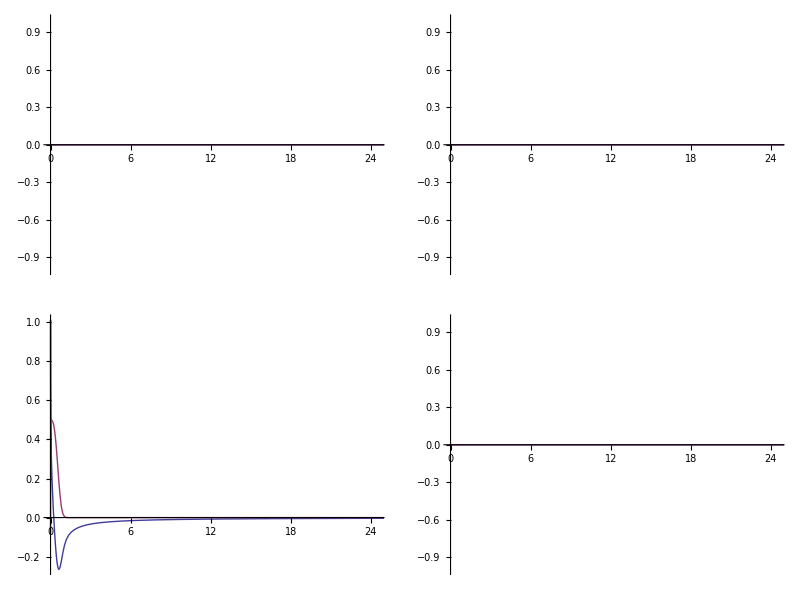
(-Graphics-)

```mathematica
FromValueList[GI⟦1⟧,CauchyMatrix[+1,GI⟦1⟧].ToValueList[GI⟦1⟧]]
```

#### Debug 3 and 1

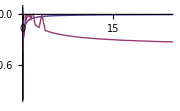

```mathematica
FromValueList[GI⟦1⟧⟦1,2⟧,CauchyMatrix[+1,GI⟦3⟧⟦1,2⟧,GI⟦1⟧⟦1,2⟧].ToValueList[GI⟦3⟧⟦1,2⟧]]
```

```mathematica
MapToInterval[GI⟦3⟧⟦1,2⟧,GI⟦1⟧⟦1,2⟧//Points//Rest//Most]
```

{-1.00206+1.08644×10^-19 ⅈ,-1.00828+4.37278×10^-19 ⅈ,-1.01879-1.76747×10^-18 ⅈ,-1.03381+1.79387×10^-18 ⅈ,-1.05368+0. ⅈ,-1.07885+0. ⅈ,-1.10992+0. ⅈ,-1.14769+8.00151×10^-18 ⅈ,-1.19319+0. ⅈ,-1.2478+0. ⅈ,-1.31329+1.85661×10^-17 ⅈ,-1.39208+0. ⅈ,-1.48743+0. ⅈ,-1.60388+0. ⅈ,-1.7479+0. ⅈ,-1.92904+0. ⅈ,-2.16198+0. ⅈ,-2.47046+0. ⅈ,-2.89549+0. ⅈ,-3.5146+2.82851×10^-16 ⅈ,-4.49396+0. ⅈ,-6.26567+0. ⅈ,-10.4142+0. ⅈ,-31.1997+0. ⅈ,31.1997+2.53137×10^-14 ⅈ,10.4142+0. ⅈ,6.26567-1.53917×10^-15 ⅈ,4.49396+0. ⅈ,3.5146-3.51008×10^-16 ⅈ,2.89549+1.99444×10^-16 ⅈ,2.47046+0. ⅈ,2.16198+0. ⅈ,1.92904+0. ⅈ,1.7479-6.21×10^-17 ⅈ,1.60388+0. ⅈ,1.48743+0. ⅈ,1.39208+0. ⅈ,1.31329+0. ⅈ,1.2478+0. ⅈ,1.19319+0. ⅈ,1.14769+0. ⅈ,1.10992+0. ⅈ,1.07885+0. ⅈ,1.05368+0. ⅈ,1.03381+0. ⅈ,1.01879+0. ⅈ,1.00828+0. ⅈ,1.00206+0. ⅈ}

```mathematica
CauchyMatrix[+1,GI⟦3⟧⟦1,2⟧,GI⟦1⟧⟦1,2⟧]-OldCauchyMatrix[+1,GI⟦3⟧⟦1,2⟧,GI⟦1⟧⟦1,2⟧]//Norm
```

3.53438×10^-14

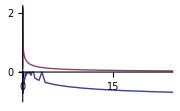

```mathematica
FPCauchyBasis[+1,GI⟦3⟧⟦1,2⟧,2,GI⟦1⟧⟦1,2⟧]
```

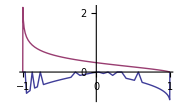

```mathematica
IFun[Join[{0},CauchyBasis[GI⟦3⟧⟦1,2⟧,2,GI⟦1⟧⟦1,2⟧//Points//Rest//Most],{0}],UnitInterval]
```

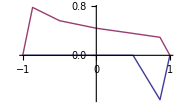

```mathematica
IFun[Join[{0},CauchyBasis[UnitInterval,2,MapToInterval[GI⟦3⟧⟦1,2⟧,(GI⟦1⟧⟦1,2⟧//Points)⟦2;;6⟧]],{0}],UnitInterval]
```

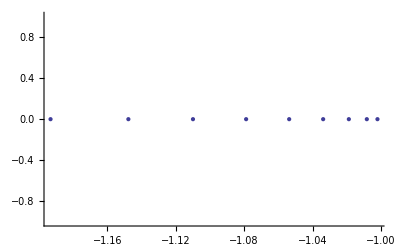

```mathematica
MapToInterval[GI⟦3⟧⟦1,2⟧,(GI⟦1⟧⟦1,2⟧//Points)⟦2;;10⟧]//Chop//ComplexDotPlot
```

```mathematica
ψpH[2,IntervalToInnerCircle[MapToInterval[GI⟦3⟧⟦1,2⟧,SetPrecision[(GI⟦1⟧⟦1,2⟧//Points)⟦2;;10⟧,100]]]]//Chop
```

{-0.574966,-0.182211,0.0300606,0.161825,0.247171-1.6361 ⅈ,0.302394-1.42711 ⅈ,0.336704-1.24034 ⅈ,0.355851,0.36367-0.923786 ⅈ}

```mathematica
IntervalToInnerCircle[MapToInterval[GI⟦3⟧⟦1,2⟧,(GI⟦1⟧⟦1,2⟧//Points)⟦2;;10⟧]]//Chop
```

{-0.937857,-0.879342,-0.824037,-0.77158,-0.721656,-0.67399,-0.628342,-0.584496,-0.542264}

```mathematica
IntervalToInnerCircle[MapToInterval[GI⟦3⟧⟦1,2⟧,(GI⟦1⟧⟦1,2⟧//Points)⟦6⟧]]
```

-0.721656+0. ⅈ

```mathematica
ψpS[2,SetPrecision[IntervalToInnerCircle[MapToInterval[GI⟦3⟧⟦1,2⟧,(GI⟦1⟧⟦1,2⟧//Points)⟦6⟧]],100]]
```

0.24717073464584416040444662984977288433643378399383524406353190983005988966062784345365396730814738+0. ⅈ

```mathematica
ψp//Clear
```

```mathematica
ψp[2,IntervalToInnerCircle[MapToInterval[GI⟦3⟧⟦1,2⟧,(GI⟦1⟧⟦1,2⟧//Points)⟦6⟧]]]//Chop
```

0.247171-1.6361 ⅈ

```mathematica
mat=CauchyMatrix[+1,GI⟦3⟧⟦1,2⟧,GI⟦1⟧⟦1,2⟧];
```

## Old Ca

```mathematica
OldCauchyMatrix[s_,f_,g_]:=Transpose[Array[FiniteValues[FPCauchyBasis[+1,f,#,g]]&,Length[f]]].FiniteTransformMatrix[f];
OldCauchyMatrix[s_?SignQ,f_IFun?VectorFunQ,g_IFun]:=OldCauchyMatrix[s,f⟦1⟧,g]//BlockDiagonalMatrix[{#,#}]&;
OldCauchyMatrix[s_?SignQ,f_IFun?MatrixFunQ,g_IFun]:=OldCauchyMatrix[s,f⟦1,1⟧,g]//BlockDiagonalMatrix[{#,#,#,#}]&;

OldCauchyMatrix[s_?SignQ,l:{__?MatrixFunQ},g_IFun]:=OldCauchyMatrix[s,#⟦1,1⟧&/@l,g]//BlockDiagonalMatrix[{#,#,#,#}]&;
OldCauchyMatrix[s_?SignQ,l:{__?MatrixFunQ},l2_List]:=OldCauchyMatrix[s,#⟦1,1⟧&/@l,l2]//BlockDiagonalMatrix[{#,#,#,#}]&;

OldCauchyMatrix[s_?SignQ,l:{__?VectorFunQ},g_IFun]:=OldCauchyMatrix[s,#⟦1⟧&/@l,g]//BlockDiagonalMatrix[{#,#}]&;
OldCauchyMatrix[s_?SignQ,l:{__?VectorFunQ},l2_List]:=OldCauchyMatrix[s,#⟦1⟧&/@l,l2]//BlockDiagonalMatrix[{#,#}]&;
OldCauchyMatrix[s_?SignQ,l_List,g_IFun]:=RightJoin@@(CauchyMatrix[s,#,g]&/@l);
OldCauchyMatrix[s_?SignQ,l_List,l2_List]:=Join@@(CauchyMatrix[s,l,#]&/@l2);

OldCauchyMatrix[s_?SignQ,f_IFun]:=CauchyMatrix[s,f,f];
OldCauchyMatrix[s_?SignQ,f_List]:=CauchyMatrix[s,f,f];
```

## Hastings–McLeod Reverse Orientation

```mathematica
{s[1],s[2],s[3]}={I,0,-I};
{s[4],s[5],s[6]}=-Array[s,3];
θ[x_,z_]:=(8 I)/3 z^3+ 2 I x z;
G//Clear;
G[_][_,_?InfinityQ]:=({{1, 0}, {0, 1}});
G[1][x_,z_]:=({{1, 0}, {s[1]Exp[θ[x,z]], 1}})/.Underflow[]->0//Inverse;
G[3][x_,z_]:=({{1, 0}, {s[3]Exp[θ[x,z]], 1}})/.Underflow[]->0//Inverse;
G[4][x_,z_]:=({{1, s[4]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0//Inverse;
G[6][x_,z_]:=({{1, s[6]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0//Inverse;
```

GG returns the jump curve sampled at n points along each ray

```mathematica
GG//Clear
```

```mathematica
GGR[n_,x_]:={IFun[Inverse[G[1][x,#]]&,Line[{0,∞ Exp[I π/6]}],n],IFun[G[3][x,#]&,Line[{∞ Exp[I (π/6+2 π/3)],0}],n],
IFun[G[4][x,#]&,Line[{∞ Exp[I (-π/6-2 π/3)],0}],n],
IFun[G[6][x,#]&,Line[{∞ Exp[I (-π/6)],0}],n]
};
```

```mathematica
GG[n_,x_]:={IFun[G[1][x,#]&,Line[{∞ Exp[I π/6],0}],n],IFun[G[3][x,#]&,Line[{∞ Exp[I (π/6+2 π/3)],0}],n],
IFun[G[4][x,#]&,Line[{∞ Exp[I (-π/6-2 π/3)],0}],n],
IFun[G[6][x,#]&,Line[{∞ Exp[I (-π/6)],0}],n]
};
```

We can plot the domain of our jump curve

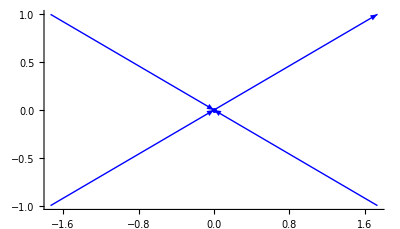

```mathematica
GGR[30,0.]//DomainPlot
```

RHSolverTop precomputes the Cauchy matrices for a given grid, to speed up evaluation for multiple x's.  The Top means that only the top row is returned

```mathematica
GI=#-IdentityMatrix[2]&/@#&/@GG[30,0.];
GI11=#⟦2,1⟧&/@GI;
GIR=#-IdentityMatrix[2]&/@#&/@GGR[30,0.];
GI11R=#⟦2,1⟧&/@GIR;
```

```mathematica
matp=CauchyMatrix[+1,GI11];
```

```mathematica
matpR=CauchyMatrix[+1,GI11R];
```

```mathematica
FromValueList[GI11R,matpR.ToValueList[GI11R]]⟦1⟧//First
```

-4.44089×10^-16+0.666667 ⅈ

```mathematica
FromValueList[GI11,matp.ToValueList[GI11]]⟦1⟧//Last
```

0.-0.333333 ⅈ

```mathematica
LeftSingularityData[-1,GI11R⟦1⟧]+(RightSingularityData[GI11R⟦2⟧,π/6]+RightSingularityData[GI11R⟦3⟧,π/6]+RightSingularityData[GI11R⟦4⟧,π/6])
```

{2.08167×10^-16-0.333333 ⅈ,2.77556×10^-17-3.65927×10^-33 ⅈ}

```mathematica
RightSingularityData[+1,GI11⟦1⟧]+(RightSingularityData[GI11⟦2⟧,π/6]+RightSingularityData[GI11⟦3⟧,π/6]+RightSingularityData[GI11⟦4⟧,π/6])
```

{0.-0.333333 ⅈ,0.-1.92593×10^-33 ⅈ}

```mathematica
RightSingularityData[GI11R⟦2⟧,π/6]+RightSingularityData[GI11R⟦3⟧,π/6]+RightSingularityData[GI11R⟦4⟧,π/6]
```

{0.0826565+0.166667 ⅈ,0.159155-9.62965×10^-34 ⅈ}

```mathematica
RightSingularityData[GI11⟦2⟧,π/6]+RightSingularityData[GI11⟦3⟧,π/6]+RightSingularityData[GI11⟦4⟧,π/6]
```

{0.0826565+0.166667 ⅈ,0.159155-9.62965×10^-34 ⅈ}

```mathematica
LeftSingularityData[+1,GI11⟦1⟧]+RightSingularityData[GI11⟦2⟧,π/6]+RightSingularityData[GI11⟦3⟧,π/6]+RightSingularityData[GI11⟦4⟧,π/6]//Chop
```

{0.165313-0.333333 ⅈ,0.31831}

```mathematica
FromValueList[GI,matp.ToValueList[GI]]⟦1⟧//First
```

{{0.+0. ⅈ,0.+0.333333 ⅈ},{0.165313-0.333333 ⅈ,0.+0. ⅈ}}

```mathematica
LeftSingularityData[+1,GI⟦1⟧]+RightSingularityData[GI⟦2⟧,π/6]+RightSingularityData[GI⟦3⟧,π/6]+RightSingularityData[GI⟦4⟧,π/6]//Chop
```

{{-0.333333 ⅈ,0},{0.31831,0}}

```mathematica
%//First
```

{{0.+0. ⅈ,0.+0.333333 ⅈ},{0.165313-0.333333 ⅈ,0.+0. ⅈ}}

```mathematica
LeftContourArg/@GG[30,0.]
```

{π/6,-π/6,π/6,(5 π)/6}

General::unfl: Underflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

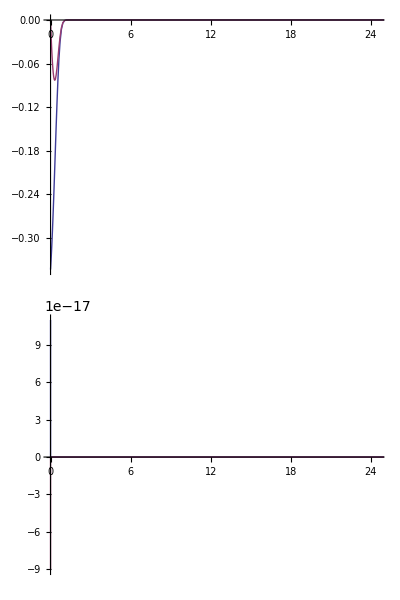
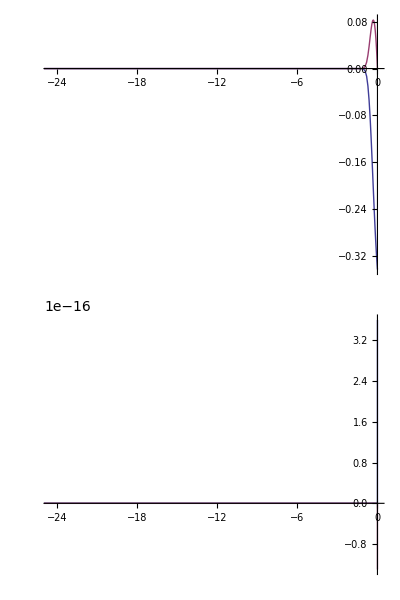
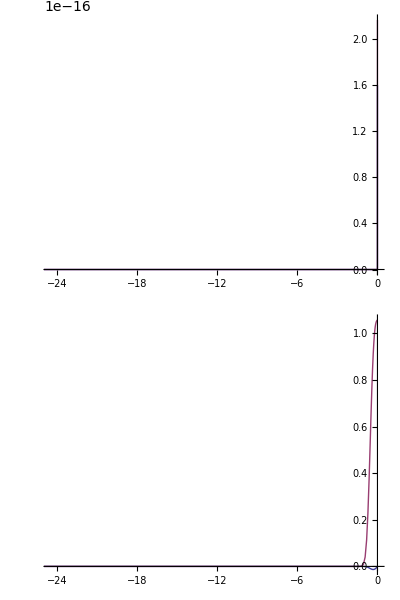
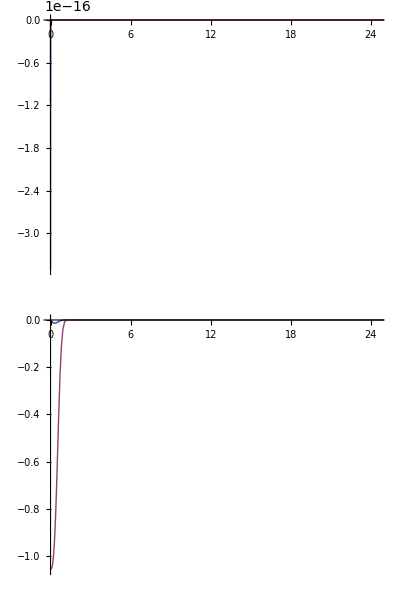
{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
RHSolveTop[GGR[50,0.]]
```

```mathematica
%980//DomainPlot
```

-Graphics-

```mathematica
Last/@DCT/@%980
```

{{4.30033×10^-9-1.06747×10^-9 ⅈ,-1.12035×10^-18+9.19342×10^-19 ⅈ},{-4.30033×10^-9-1.06747×10^-9 ⅈ,3.6749×10^-18-1.32679×10^-18 ⅈ},{1.62967×10^-18+2.20629×10^-18 ⅈ,3.39281×10^-10-1.00982×10^-7 ⅈ},{-1.17918×10^-18-3.57918×10^-18 ⅈ,3.39281×10^-10+1.00982×10^-7 ⅈ}}

```mathematica
-2 (Plus@@(Last/@Integrate/@(#⟦2⟧&/@%980)))/(2 π I)
```

0.367062-3.53466×10^-17 ⅈ

```mathematica
RHSR//Clear;
RHSR[n_]:=RHSR[n]=RHSolverTop[GG[n,0.]];
```

```mathematica
RHS//Clear;
RHS[n_]:=RHS[n]=RHSolverTop[GG[n,0.]];
```

U returns the top row of a jump curve, so that the top row of the solution to the RH problem is {1,0} + Cauchy[U[n,x], z]

```mathematica
U//Clear;
U[n_,x_]:=U[n,x]=RHS[n][GG[n,x]];
```

p is the value of the Hastings–McLeod solution

```mathematica
p//Clear;
p[n_,x_]:=p[n,x]=-2 (Plus@@(Last/@Integrate/@(#⟦2⟧&/@U[n,x])))/(2 π I)
```

Here is a plot of the solution

```mathematica
Last/@DCT/@U[50,0.]//Chop
```

{{-0.000857825+0.0010467 ⅈ,0},{0.000944075+0.000954425 ⅈ,0},{0,-0.00829142+0.000436641 ⅈ},{0,0.00854423-0.000444274 ⅈ}}

```mathematica
p[50,0.]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

0.353986-0.0216042 ⅈ

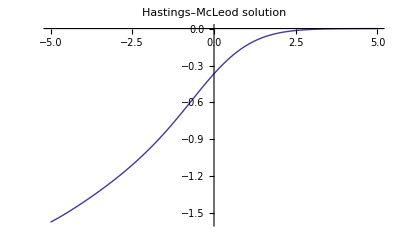

```mathematica
TablePlot[p[50,x],{x,-5.,5.,.1},PlotLabel->"Hastings–McLeod solution"]
```

We can compare with the Prähofer and Spohn computed values

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];data2=Select[data,-3.<=First[#]≤3.&];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

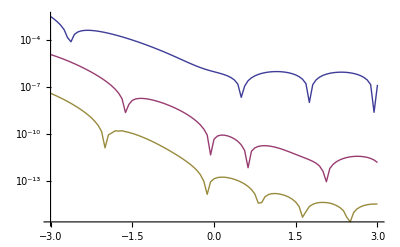

```mathematica
Monitor[{
(x=#⟦1⟧;{#⟦1⟧,p[25,#⟦1⟧]-#⟦3⟧//Abs})&/@data2,
{#⟦1⟧,p[50,#⟦1⟧]-#⟦3⟧//Abs}&/@data2,
(x=#⟦1⟧;{#⟦1⟧,p[75,#⟦1⟧]-#⟦3⟧//Abs})&/@data2
},x]//ListLineLogPlot
```

## Hastings–McLeod Reverse Orientation Interval

```mathematica
{s[1],s[2],s[3]}={I,0,-I};
{s[4],s[5],s[6]}=-Array[s,3];
θ[x_,z_]:=(8 I)/3 z^3+ 2 I x z;
G//Clear;
G[_][_,_?InfinityQ]:=({{1, 0}, {0, 1}});
G[1][x_,z_]:=({{1, 0}, {s[1]Exp[θ[x,z]], 1}})/.Underflow[]->0//Inverse;
G[3][x_,z_]:=({{1, 0}, {s[3]Exp[θ[x,z]], 1}})/.Underflow[]->0//Inverse;
G[4][x_,z_]:=({{1, s[4]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0//Inverse;
G[6][x_,z_]:=({{1, s[6]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0//Inverse;
```

GG returns the jump curve sampled at n points along each ray

```mathematica
GG//Clear
```

```mathematica
GGR[n_,x_]:={IFun[Inverse[G[1][x,#]]&,Line[{0,1.+1. I}],n],IFun[Inverse[G[1][x,#]]&,Line[{1.+1. I,∞ Exp[I π/6]}],n],IFun[G[3][x,#]&,Line[{∞ Exp[I (π/6+2 π/3)],0}],n],
IFun[G[4][x,#]&,Line[{∞ Exp[I (-π/6-2 π/3)],0}],n],
IFun[G[6][x,#]&,Line[{∞ Exp[I (-π/6)],0}],n]
};
```

```mathematica
GG[n_,x_]:={IFun[G[1][x,#]&,Line[{∞ Exp[I π/6],0}],n],IFun[G[3][x,#]&,Line[{∞ Exp[I (π/6+2 π/3)],0}],n],
IFun[G[4][x,#]&,Line[{∞ Exp[I (-π/6-2 π/3)],0}],n],
IFun[G[6][x,#]&,Line[{∞ Exp[I (-π/6)],0}],n]
};
```

We can plot the domain of our jump curve

```mathematica
FromValueList[GI,matp.ToValueList[GI]]⟦1⟧//First
```

{{0.+0. ⅈ,0.+0.333333 ⅈ},{0.165313-0.333333 ⅈ,0.+0. ⅈ}}

```mathematica
LeftSingularityData[+1,GI⟦1⟧]+RightSingularityData[GI⟦2⟧,π/6]+RightSingularityData[GI⟦3⟧,π/6]+RightSingularityData[GI⟦4⟧,π/6]//Chop
```

{{-0.333333 ⅈ,0},{0.31831,0}}

```mathematica
%//First
```

{{0.+0. ⅈ,0.+0.333333 ⅈ},{0.165313-0.333333 ⅈ,0.+0. ⅈ}}

```mathematica
LeftContourArg/@GG[30,0.]
```

{π/6,-π/6,π/6,(5 π)/6}

```mathematica
U//Clear
```

```mathematica
U=RHSolveTop[GGR[50,0.]];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

```mathematica
Last/@DCT/@U//Chop
```

{{0,0},{0,0},{-4.30015×10^-9-1.0676×10^-9 ⅈ,0},{0,3.38709×10^-10-1.00983×10^-7 ⅈ},{0,3.41498×10^-10+1.00983×10^-7 ⅈ}}

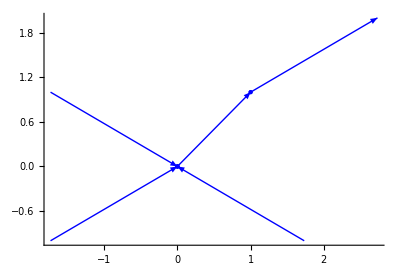

```mathematica
U//DomainPlot
```

```mathematica
Last/@DCT/@%980
```

{{4.30033×10^-9-1.06747×10^-9 ⅈ,-1.12035×10^-18+9.19342×10^-19 ⅈ},{-4.30033×10^-9-1.06747×10^-9 ⅈ,3.6749×10^-18-1.32679×10^-18 ⅈ},{1.62967×10^-18+2.20629×10^-18 ⅈ,3.39281×10^-10-1.00982×10^-7 ⅈ},{-1.17918×10^-18-3.57918×10^-18 ⅈ,3.39281×10^-10+1.00982×10^-7 ⅈ}}

```mathematica
-2 (Plus@@(Last/@Integrate/@(#⟦2⟧&/@U)))/(2 π I)
```

0.367062+6.56991×10^-12 ⅈ

```mathematica
RHSR//Clear;
RHSR[n_]:=RHSR[n]=RHSolverTop[GG[n,0.]];
```

```mathematica
RHS//Clear;
RHS[n_]:=RHS[n]=RHSolverTop[GG[n,0.]];
```

U returns the top row of a jump curve, so that the top row of the solution to the RH problem is {1,0} + Cauchy[U[n,x], z]

```mathematica
U//Clear;
U[n_,x_]:=U[n,x]=RHS[n][GG[n,x]];
```

p is the value of the Hastings–McLeod solution

```mathematica
p//Clear;
p[n_,x_]:=p[n,x]=-2 (Plus@@(Last/@Integrate/@(#⟦2⟧&/@U[n,x])))/(2 π I)
```

Here is a plot of the solution

```mathematica
Last/@DCT/@U[50,0.]//Chop
```

{{-0.000857825+0.0010467 ⅈ,0},{0.000944075+0.000954425 ⅈ,0},{0,-0.00829142+0.000436641 ⅈ},{0,0.00854423-0.000444274 ⅈ}}

```mathematica
p[50,0.]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

0.353986-0.0216042 ⅈ

```mathematica
TablePlot[p[50,x],{x,-5.,5.,.1},PlotLabel->"Hastings–McLeod solution"]
```

-Graphics-

We can compare with the Prähofer and Spohn computed values

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];data2=Select[data,-3.<=First[#]≤3.&];
```

```mathematica
Monitor[{
(x=#⟦1⟧;{#⟦1⟧,p[25,#⟦1⟧]-#⟦3⟧//Abs})&/@data2,
{#⟦1⟧,p[50,#⟦1⟧]-#⟦3⟧//Abs}&/@data2,
(x=#⟦1⟧;{#⟦1⟧,p[75,#⟦1⟧]-#⟦3⟧//Abs})&/@data2
},x]//ListLineLogPlot
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

-Graphics-

## Cauchy eval at sing

```mathematica
hf1=IFun[Sech,Line[{-∞,0}]];
hf2=IFun[Sech,Line[{0,∞}]];
```

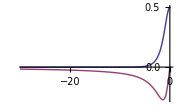
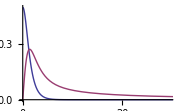

```mathematica
Cauchy[+1,{hf1,hf2},{hf1,hf2}]
```

```mathematica
Hilbert[{hf1,hf2},0.1]-Hilbert[LFun[Sech,Line[{-∞,∞}],200],0.1]
```

-5.95882×10^-12+6.75447×10^-11 ⅈ

```mathematica
Hilbert[{hf1,hf2},0.]
```

ⅈ ∞

```mathematica
x=0.
```

0.

```mathematica
Cauchy[+1,{hf1,hf2},{hf1,hf2}]
```

{-Graphics-,-Graphics-}

```mathematica
?Which
```

Which[test_1,value_1,test_2,value_2,…] evaluates each of the test_i in turn, returning the value of the value_i corresponding to the first one that yields True.

```mathematica
Cauchy[s_,f_List,x_]/;(Or@@(x~NEqual~#&/@Join[LeftEndpoint/@f,
RightEndpoint/@f]))&&
NZeroQ[Plus@@(Which[
x~NEqual~LeftEndpoint[#],
First[#],
x~NEqual~RightEndpoint[#],
Last[#],
True,
0. First[#]]&/@f)
]:=Plus@@(Which[
x~NEqual~LeftEndpoint[#],
LeftSingularityData[s,#],
x~NEqual~RightEndpoint[#],
Last[#],
True,
0. First[f⟦1⟧]]&/@f);
```

```mathematica
0.
```

0.